```mathematica
Solve[{2x-y==0,-x+2y==3},{x,y}]
```

{{x→1,y→2}}

```mathematica
Solve[{2x-y==0,-x+2y-z==-1,-3y+4z==4},{x,y,z}]
```

{{x→0,y→0,z→1}}

```mathematica
{2x-y==0,-x+2y-z==-1,-3y+4z==4}
```

{2 x-y==0,-x+2 y-z==-1,-3 y+4 z==4}

```mathematica
Eigenvectors[{2 x-y==0,-x+2 y-z==-1,-3 y+4 z==4}]
```

Eigenvectors::matsq: Argument {2 x-y==0,-x+2 y-z==-1,-3 y+4 z==4} at position 1 is not a non-empty square matrix.

Eigenvectors[{2 x-y==0,-x+2 y-z==-1,-3 y+4 z==4}]

```mathematica
CoefficientList@{2 x-y==0,-x+2 y-z==-1,-3 y+4 z==4}
```

CoefficientList::argtu: CoefficientList called with 1 argument; 2 or 3 arguments are expected.

CoefficientList[{2 x-y==0,-x+2 y-z==-1,-3 y+4 z==4}]

```mathematica
{{2,-1,0},{-1,2,-1},{0,-3,4}}
```

{{2,-1,0},{-1,2,-1},{0,-3,4}}

```mathematica
Eigenvalues[{{2,-1,0},{-1,2,-1},{0,-3,4}}]
```

{Root5.09Root[-6+16 #1-8 #1^2+#1^3&,3]5.086130197651494,Root2.43Root[-6+16 #1-8 #1^2+#1^3&,2]2.428006731683797,Root0.486Root[-6+16 #1-8 #1^2+#1^3&,1]0.4858630706647089}

```mathematica
Inverse[{{2,-1,0},{-1,2,-1},{0,-3,4}}]
```

{{5/6,2/3,1/6},{2/3,4/3,1/3},{1/2,1,1/2}}

```mathematica
Det[{{2,-1,0},{-1,2,-1},{0,-3,4}}]
```

6

```mathematica
Map[Point,{{2,-1,0},{-1,2,-1},{0,-3,4}}]
```

{Point[{2,-1,0}],Point[{-1,2,-1}],Point[{0,-3,4}]}

```mathematica
Graphics@{Point[{2,-1,0}],Point[{-1,2,-1}],Point[{0,-3,4}]}
```

-Graphics-

```mathematica
Map[Normalize,{{2,-1,0},{-1,2,-1},{0,-3,4}}]
```

{{2/(√5),-1/(√5),0},{-1/(√6),√(2/3),-1/(√6)},{0,-3/5,4/5}}

```mathematica
A x ==b
```

A x==b

```mathematica
{{a,b},{c,d}}{x,y}=={e,f}
```

{{a x,b x},{c y,d y}}=={e,f}

```mathematica
Solve[{{a x,b x},{c y,d y}}=={e,f},x]
```

{}

```mathematica
Inverse[A]A x ==Inverse[A]b
```

A x Inverse[A]==b Inverse[A]

```mathematica
IdentityMatrix[2]
```

{{1,0},{0,1}}

```mathematica
Det[{{1,0},{0,1}}]
```

1

```mathematica
Det@{{1,2},{3,4}}
```

-2

```mathematica
Eigenvalues@{{1,2},{3,4}}
```

{1/2 (5+√33),1/2 (5-√33)}

```mathematica
Eigenvectors@{{1,2},{3,4}}
```

{{1/6 (-3+√33),1},{1/6 (-3-√33),1}}

```mathematica
{{1,2},{3,4}}{1/6 (-3+√33),1}
```

{{1/6 (-3+√33),1/3 (-3+√33)},{3,4}}

```mathematica
MatrixForm[{{1/6 (-3+√33),1/3 (-3+√33)},{3,4}}]
```

(1/6 (-3+√33) | 1/3 (-3+√33)
3 | 4)

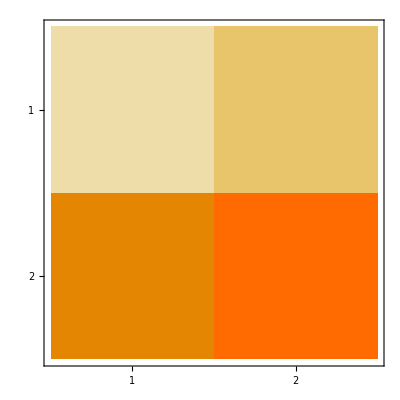

```mathematica
MatrixPlot[{{1/6 (-3+√33),1/3 (-3+√33)},{3,4}}]
```

```mathematica
{{1,2},{3,4}}.{1/6 (-3+√33),1}
```

{2+1/6 (-3+√33),4+1/2 (-3+√33)}

```mathematica
{{1,2},{3,4}}*{1/6 (-3+√33),1}
```

{{1/6 (-3+√33),1/3 (-3+√33)},{3,4}}

```mathematica
{{a,b},{c,d}} . {{r,s},{t,u}}
```

{{a r+b t,a s+b u},{c r+d t,c s+d u}}

```mathematica
MatrixForm[{{a r+b t,a s+b u},{c r+d t,c s+d u}}]
```

(a r+b t | a s+b u
c r+d t | c s+d u)

```mathematica
{{1,2},{3,4}}.{1/6 (-3+√33),1}
```

{2+1/6 (-3+√33),4+1/2 (-3+√33)}

```mathematica
Inverse@{{1,2},{3,4}}
```

{{-2,1},{3/2,-1/2}}

```mathematica
MatrixForm[{{-2,1},{3/2,-1/2}}]
```

(-2 | 1
3/2 | -1/2)

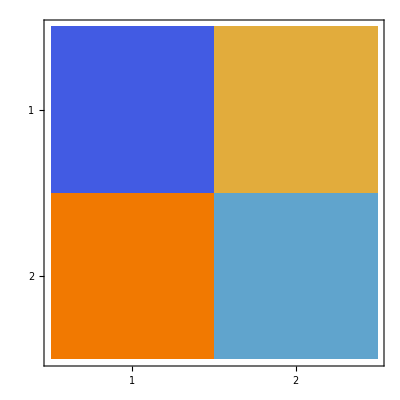

```mathematica
MatrixPlot[{{-2,1},{3/2,-1/2}}]
```

```mathematica
Integrate[x,{x,0,2}]
```

2

```mathematica
Inverse@IdentityMatrix[1]
```

{{1}}

```mathematica
Inverse@IdentityMatrix[2]
```

{{1,0},{0,1}}

```mathematica
Inverse[IdentityMatrix[2]].IdentityMatrix[2]
```

{{1,0},{0,1}}

```mathematica
{{1,2},{3,4}}.Inverse[{{1,2},{3,4}}]
```

{{1,0},{0,1}}

```mathematica
LogLikelihood[NormalDistribution[],{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}]
```

-3/2 (Log[2]+Log[π])+1/2 (-x_1^2-x_2^2-x_3^2)

```mathematica
-3/2 (Log[2]+Log[π])+1/2∑_(i=1)^n -Subscript[x, i]^2
```

-3/2 (Log[2]+Log[π])+1/2 ∑_(i=1)^n -x_i^2

```mathematica
{4.75,2.19,1.27,3.15,-5.16,5.65,0.98,-0.96,1.23,1.36,2.89,2.56}/100
```

{0.0475,0.0219,0.0127,0.0315,-0.0516,0.0565,0.0098,-0.0096,0.0123,0.0136,0.0289,0.0256}

```mathematica
GeometricMean[Out[41]]
```

0.0221736

```mathematica
100 Out[42]
```

2.21736

```mathematica
1500 6.81
```

10215.

```mathematica
60.37/(.0399)
```

1513.03

```mathematica
6.81/(.0399)
```

170.677

```mathematica
170.6766917293233 100
```

17067.7

```mathematica
2/(.002)
```

1000.

```mathematica
1000.`100
```

1000.

```mathematica
100 1000
```

100000

```mathematica
100(1+r)^12
```

100 (1+r)^12

```mathematica
100(1+.05)^12
```

179.586

```mathematica
FinancialData["NYSE:CHK","Close"]
```

QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[0.9,USDollars]]

```mathematica
FinanClosecialData["NYSE:CHK","Price"]
```

QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[0.9,USDollars]]

```mathematica
FinancialData["NYSE:CHK","Price","Units"]
```

Units

```mathematica
With[{stocks={"NASDAQ:GOOGL","NYSE:CHK","NYSE:IBM"}},
Table[
With[{stock=FinancialData[s,"Close",All]},
Transpose[{
stock["Dates"][[;;-2]],
Ratios@stock["Values"]
}]
],{s,stocks}]
]
```

TimeSeries::invstrct: The data TemporalData[TimeSeries,{«1»},True,11.1] is not a structurally valid TemporalData object.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

Transpose::nmtx: The first two levels of {TimeSeries[TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{3873},StructuredArray`StructuredData[QuantityArray,{«3873»},«1»,{«1»}]]},«6»},True,11.1],{«1»}][],Ratios[«1»[Values]]} cannot be transposed.

TimeSeries::invstrct: The data TemporalData[TimeSeries,{«1»},True,11.1] is not a structurally valid TemporalData object.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

Transpose::nmtx: The first two levels of {TimeSeries[TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{6779},StructuredArray`StructuredData[QuantityArray,{«6779»},«1»,{«1»}]]},«6»},True,11.1],{«1»}][],Ratios[«1»[Values]]} cannot be transposed.

TimeSeries::invstrct: The data TemporalData[TimeSeries,{«1»},True,11.1] is not a structurally valid TemporalData object.

General::stop: Further output of TimeSeries::invstrct will be suppressed during this calculation.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {«1»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

{Transpose[{TimeSeries[TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{3873},StructuredArray`StructuredData[QuantityArray,{50.2161,54.2075,54.753,52.4858,53.0514,54.0073,53.1264,51.0544,51.2346,50.1736,50.8042,50.0535,50.7992,51.1996,51.2046,52.716,53.8021,55.799,56.0543,57.0402,58.8019,59.7378,58.9771,59.2474,60.4685,59.9731,59.1873,63.4915,65.6035,64.8628,66.3542,67.5954,69.252,68.6064,69.4923,68.9317,67.6955,68.7666,70.5183,71.0688,72.1248,74.6523,74.0417,70.3131,74.7624,86.2985,93.7908,90.9881,93.0751,96.7436,95.4124,98.11,97.5294,95.9279,92.4395,84.757,86.3586,84.4317,84.0113,91.5987,91.0882,92.5246,86.3561,86.3336,83.8512,84.7821,82.63,83.8412,87.4647,89.7819,90.6127,91.0782,90.0672,89.7869,90.2874,88.2304,85.798,85.0723,86.799,85.9082,85.3076,89.4316,89.9771,88.3205,90.1272,92.5996,91.964,93.2403,94.041,96.048,96.4734,96.5435,98.8957,96.4884,101.453,97.3442,96.8487,94.3663,97.0189,97.6245,96.8638,97.7847,97.7596,100.082,102.049,98.7456,97.0539,94.2312,90.4476,88.6458,94.7117,94.1311,95.2622,97.9048,96.043,103.08,105.532,102.279,98.11,99.4162,95.8828,94.0811,93.7908,96.5885,97.7096,99.3011,99.0459,99.0709,95.7777,97.069,94.5365,93.025,94.0861,93.1201,92.6797,93.5931,93.0401,94.4965,92.6897,90.7629,90.0772,88.9861,87.5798,89.3915,87.8851,89.7319,90.1072,90.5276,89.3865,89.5767,89.7118,90.7979,89.872,90.3124,90.3425,90.1072,92.7348,94.3764,94.7017,96.9739,96.118,96.7086,97.0715,96.5585,95.8177,92.5896,93.5756,95.7927,99.146,102.209,108.01,111.873,109.481,109.996,109.831,110.107,111.253,113.205,114.361,113.6,114.12,113.119,114.01,115.757,114.471,114.731,115.637,116.678,119.696,119.706,120.922,127.849,128.124,130.531,129.726,133.129,138.769,144.995,144.089,140.266,145.611,146.702,141.137,143.294,141.387,141.512,139.31,137.533,139.285,140.286,143.489,144.059,144.79,144.995,148.769,152.197,151.146,146.502,147.217,145.766,147.998,145.904,147.913,148.259,146.817,146.033,149.575,150.591,150.741,149.915,155.1,156.151,157.122,151.346,148.068,148.188,148.609,146.892,144.019,145.946,149.74,150.005,149.009,146.317,145.766,145.926,142.978,142.163,145.001,142.138,144.034,143.424,140.131,140.136,137.138,139.925,141.422,141.432,141.927,144.365,143.774,143.139,143.264,144.365,143.694,147.578,147.838,149.695,155.02,155.991,151.647,151.457,150.245,152.042,154.104,156.101,155.836,157.833,157.292,157.122,153.148,154.96,158.383,159.494,155.651,155.506,156.527,156.647,155.475,153.198,150.631,148.864,148.213,152.648,151.787,154.5,151.747,170.115,174.819,173.623,177.892,176.701,179.259,186.25,189.874,190.024,193.162,195.404,197.842,195.139,189.759,195.739,195.389,198.672,196.59,199.268,201.92,200.299,204.878,208.437,211.635,214.543,211.945,201.965,202.653,207.246,209.052,203.122,202.466,202.201,205.524,204.798,206.506,208.947,209.683,211.47,215.283,212.506,215.078,213.372,216.229,215.674,212.526,213.552,210.279,207.631,217.826,224.698,225.839,233.056,233.676,235.108,236.043,232.04,233.351,233.781,222.671,218.434,199.924,213.957,221.73,216.57,217.343,216.955,213.617,216.54,202.696,198.212,190.962,192.737,184.138,184.719,179.559,181.481,173.017,171.826,171.356,183.408,184.554,183.473,182.922,189.218,188.883,195.377,181.486,182.577,188.407,189.273,184.228,182.402,177.111,171.666,168.914,168.693,175.75,172.417,169.549,170.06,174.264,170.125,170.275,171.111,183.077,185.024,188.783,197.681,194.408,195.189,195.039,202.366,204.193,205.789,203.277,208.392,205.028,205.864,201.275,203.607,202.316,205.449,208.202,218.762,220.463,213.787,213.191,210.218,209.172,199.643,197.591,197.276,197.566,197.341,197.581,204.598,201.685,193.687,187.246,188.282,185.83,187.431,185.675,185.189,185.655,187.972,190.81,191.555,190.86,186.15,186.09,191.495,189.904,187.401,195.184,193.442,196.841,193.472,190.955,193.45,192.381,195.689,195.539,194.258,193.773,201.26,200.169,202.626,202.306,201.355,203.252,209.107,209.868,211.805,210.934,211.8,210.429,209.303,212.486,208.827,204.613,201.945,204.143,201.72,199.693,193.748,195.243,195.639,194.869,192.937,191.34,194.248,193.487,187.937,183.793,187.877,187.106,190.049,190.685,188.568,187.281,184.429,184.894,190.67,194.048,193.072,191.866,188.833,189.328,186.896,188.382,186.811,190.66,191.345,190.559,189.448,189.428,192.366,190.254,191.06,189.108,192.231,196.14,203.577,202.186,205.139,207.466,202.161,198.692,203.622,203.922,202.186,203.632,201.655,201.986,201.145,200.914,202.216,208.051,206.105,210.454,214.708,213.532,215.163,213.927,213.857,211.079,212.08,209.858,213.236,230.058,242.555,236.884,243.536,242.785,237.83,238.516,238.426,233.976,237.095,236.128,238.706,236.514,237.73,236.544,237.004,240.748,245.212,246.203,248.19,249.637,247.765,255.072,254.251,252.745,242.61,244.987,242.56,242.64,240.633,242.66,243.736,244.592,241.554,242.29,242.199,241.123,239.727,241.294,240.383,231.624,234.542,231.674,228.321,228.011,228.987,234.242,231.504,232.46,234.022,241.864,243.831,242.024,242.985,244.967,250.102,252.745,252.384,248.881,244.151,245.112,240.653,239.757,249.777,244.281,248.16,246.474,247.399,250.993,241.108,240.983,233.806,235.968,235.233,235.743,231.169,229.367,231.614,233.191,230.959,235.198,236.279,238.161,238.156,235.538,232.69,224.602,224.943,224.332,219.553,220.686,228.997,228.041,227.58,226.699,227.595,221.73,224.217,223.311,220.639,223.832,222.856,228.506,231.244,231.139,232.725,232.035,231.159,230.683,229.302,229.487,236.529,235.738,235.983,234.332,233.476,232.49,233.921,233.371,237.365,236.629,238.236,236.053,241.474,239.772,238.996,239.227,240.823,239.737,235.918,234.727,233.116,236.844,235.788,233.861,233.631,234.852,230.959,233.596,231.114,229.222,236.534,235.708,235.388,235.528,238.161,237.215,237.395,241.994,243.791,249.542,249.196,250.441,253.781,259.671,259.376,257.765,257.995,255.918,252.63,252.756,251.664,253.19,257.85,257.404,255.232,257.304,262.744,263.966,265.387,263.4,262.759,261.944,265.447,267.429,271.077,269.961,271.543,271.933,272.499,272.929,276.348,276.763,277.769,275.016,274.561,260.312,256.503,257.249,255.127,254.246,256.193,258.305,255.247,256.719,255.753,251.744,255.247,258.26,263.145,257.805,258.26,258.,254.546,249.016,245.998,250.262,249.201,253.55,256.623,256.343,257.75,256.879,253.445,256.688,255.948,257.875,262.829,264.156,262.014,259.927,257.489,260.918,261.578,262.644,264.631,262.904,267.894,273.69,276.683,280.321,284.285,284.776,284.355,284.025,283.91,291.557,292.478,292.293,289.796,297.313,305.105,307.891,312.998,311.301,319.004,310.355,308.298,317.047,320.12,322.667,325.69,338.212,338.237,334.579,337.627,339.944,347.722,353.843,351.946,355.97,363.177,371.254,366.825,347.256,332.307,316.341,330.595,321.151,315.13,317.122,313.228,324.584,330.58,338.678,333.323,337.111,346.465,348.838,346.836,341.095,342.411,349.593,357.977,357.781,359.558,349.941,350.014,347.361,345.314,334.939,337.001,339.013,345.179,348.683,350.704,355.764,350.709,351.605,346.075,342.927,342.997,328.818,324.94,316.146,326.916,323.678,319.434,327.227,319.134,308.273,300.686,300.416,292.458,274.576,287.523,283.474,278.259,275.527,274.401,282.423,258.2,247.955,253.646,251.098,252.72,258.595,260.832,259.296,267.569,266.383,265.077,254.722,254.747,251.674,254.146,243.456,232.32,236.659,237.925,235.818,228.731,222.515,224.067,216.56,216.885,207.01,220.133,220.303,221.72,219.172,210.138,219.793,216.209,216.985,230.503,225.608,229.317,222.255,219.252,220.448,233.081,233.076,227.78,235.773,238.641,234.132,232.32,234.767,228.947,226.049,223.636,227.735,224.988,269.966,269.156,277.769,273.51,271.783,272.294,276.327,279.506,287.423,296.827,290.927,297.738,293.464,289.781,291.787,286.878,292.753,291.782,288.429,290.781,290.316,289.04,289.58,275.261,274.996,272.574,280.722,284.395,291.782,293.184,287.779,283.925,286.387,293.434,283.775,279.205,277.353,272.864,276.743,286.032,286.682,285.006,281.462,280.371,273.48,272.869,271.413,275.767,264.666,264.291,263.465,267.624,263.775,268.76,272.219,277.534,271.037,270.547,267.159,261.063,258.295,268.059,266.978,240.893,234.627,238.786,244.847,238.04,246.228,238.791,241.789,241.584,237.105,234.157,231.724,240.157,243.406,239.792,247.745,250.663,251.548,250.257,252.99,255.322,249.391,245.488,242.735,243.501,245.533,241.739,237.31,234.517,237.12,231.869,232.85,232.43,225.348,222.34,210.178,209.533,207.281,217.085,219.042,217.14,221.68,207.446,219.753,224.793,215.278,214.843,217.766,220.013,215.729,190.685,200.454,206.059,195.434,193.642,185.785,173.173,169.219,164.649,166.161,190.695,181.531,169.749,176.681,186.45,189.844,181.551,178.007,176.331,169.809,164.905,184.554,179.173,180.019,179.854,173.413,183.648,171.286,165.77,165.73,159.544,155.881,145.641,156.191,155.16,150.205,148.854,140.226,129.906,131.342,128.845,141.162,146.187,146.622,133.124,137.688,139.85,137.303,142.133,151.201,153.133,154.56,150.255,158.033,155.486,162.798,157.773,155.29,155.235,148.699,149.154,151.622,150.326,148.854,151.702,153.974,160.816,164.184,167.192,161.161,162.753,157.688,156.496,157.312,150.631,149.64,149.98,141.512,151.687,153.398,162.507,162.092,165.901,174.504,171.826,169.429,170.45,170.39,171.666,177.031,185.82,189.568,179.429,179.193,181.701,179.013,171.496,176.726,171.486,173.393,165.19,172.892,170.986,168.753,169.159,163.738,162.898,159.615,152.968,154.434,145.586,154.234,159.109,161.922,162.367,160.,167.832,166.711,165.13,165.24,174.469,173.751,172.202,176.816,174.018,171.511,174.199,177.217,181.426,185.069,184.298,179.499,181.175,186.43,189.238,184.634,189.934,194.558,196.31,189.834,190.92,192.116,192.531,194.934,193.162,192.041,195.925,198.177,197.036,201.184,201.69,201.93,198.497,203.862,204.188,199.698,194.959,193.938,195.189,198.612,199.633,198.782,198.442,196.941,202.376,202.976,205.399,208.817,213.487,214.408,216.034,220.353,222.375,219.598,218.021,216.51,214.708,212.626,208.587,208.202,207.781,207.231,210.249,203.872,203.037,204.843,208.086,212.866,212.275,210.999,209.698,204.443,205.003,198.507,201.44,205.394,207.401,212.356,212.551,219.297,221.514,215.333,215.293,214.157,214.052,218.883,223.576,222.615,220.138,218.331,223.036,221.74,226.324,227.087,225.789,225.398,228.771,228.526,227.188,229.512,231.364,230.223,222.661,222.856,222.2,230.428,232.845,234.592,235.913,234.227,233.256,232.6,231.059,228.101,226.724,228.982,230.873,229.532,232.21,235.698,236.299,237.79,239.001,244.382,246.098,245.968,248.741,249.772,249.471,248.626,246.479,249.507,249.507,248.165,243.836,242.525,244.497,249.612,259.021,257.339,258.375,262.274,263.31,267.919,265.212,275.191,276.312,276.127,275.817,277.313,277.113,277.374,274.411,270.412,275.792,268.32,267.254,268.905,270.427,274.591,275.817,281.528,283.655,285.556,284.2,286.302,288.419,289.025,288.604,286.773,285.258,291.457,291.827,293.154,290.161,291.782,295.221,294.04,293.154,292.788,293.409,293.809,294.795,296.037,295.541,298.154,296.857,299.17,297.258,298.499,299.63,300.851,306.136,309.54,311.737,310.,311.667,310.29,313.679,312.297,304.425,297.338,301.302,300.846,295.526,293.829,295.211,290.281,294.095,290.486,291.772,275.271,270.262,271.473,271.313,267.404,265.229,266.768,265.817,270.672,263.644,265.902,266.993,268.48,267.481,268.46,266.818,270.912,269.364,271.873,270.643,271.663,267.794,265.992,263.47,263.655,266.603,270.792,272.924,277.564,282.378,281.513,280.366,288.504,290.852,290.051,281.863,282.874,283.054,283.474,280.271,279.02,274.766,278.935,281.713,281.618,281.497,283.63,283.835,284.676,285.782,284.385,282.043,284.02,283.384,286.642,293.669,294.785,297.938,275.339,275.316,277.789,277.419,273.795,272.759,266.078,264.786,264.851,266.258,263.102,265.557,253.43,255.127,249.577,246.809,261.078,254.772,252.94,255.688,254.011,254.231,249.426,247.455,237.735,236.254,238.811,238.766,237.965,245.468,243.05,241.419,246.924,253.045,249.602,242.995,242.625,237.24,243.741,244.487,241.829,249.236,250.878,250.282,250.257,244.517,243.361,241.259,237.78,236.569,236.269,227.35,222.691,219.958,218.486,218.246,225.318,228.501,233.971,238.146,244.837,245.906,247.249,230.025,233.316,241.028,238.981,242.64,245.267,244.722,246.554,242.41,242.73,242.66,245.443,245.152,253.405,254.296,250.352,252.92,252.099,246.108,246.243,243.411,243.03,245.498,241.309,234.212,231.234,232.26,225.914,227.53,225.708,229.637,226.564,225.228,230.391,231.814,235.378,232.425,235.518,238.321,238.301,241.369,240.448,240.553,240.763,245.312,254.386,256.979,258.25,256.989,263.9,265.462,263.84,264.101,263.15,263.065,261.428,269.376,267.434,265.262,268.435,269.681,270.957,271.913,270.727,301.016,309.154,304.209,304.285,306.292,306.562,308.549,309.6,308.534,309.59,307.147,307.798,308.098,310.39,312.437,312.843,313.689,312.713,311.742,308.894,301.937,298.023,292.143,292.058,298.569,295.701,295.896,291.787,297.773,295.286,291.337,278.124,282.448,286.187,286.778,289.46,293.854,295.556,296.037,296.392,297.598,297.743,295.436,296.142,295.686,297.818,301.827,303.038,302.408,301.482,299.75,300.791,299.72,297.273,302.468,301.352,304.83,307.047,308.519,307.403,308.303,308.734,308.644,312.392,320.125,316.181,313.689,306.211,305.836,310.255,308.549,308.694,300.786,300.471,305.816,306.297,305.371,305.786,307.445,309.49,308.549,308.519,312.553,314.379,312.377,312.412,312.933,315.345,305.401,305.956,304.705,305.316,306.997,300.671,300.686,305.075,300.601,296.117,296.442,296.172,290.431,288.634,285.271,285.056,278.82,280.952,280.802,288.529,288.94,291.362,293.729,290.151,287.959,291.147,291.202,293.664,296.187,294.125,284.821,287.368,290.281,289.36,288.965,285.581,288.419,289.535,265.607,263.675,261.018,263.12,262.804,262.779,266.668,269.141,269.246,272.314,269.541,267.204,268.155,267.394,267.909,269.1,271.593,267.984,267.784,265.032,259.461,265.487,265.162,265.882,262.269,259.446,259.381,260.087,259.316,260.702,264.766,263.055,264.286,261.793,260.782,259.766,259.837,258.615,254.999,252.61,254.431,251.719,250.427,242.745,242.525,246.739,243.738,240.343,237.67,241.634,247.064,249.026,253.435,260.766,266.478,267.939,273.565,266.253,263.895,267.264,269.391,264.726,299.1,297.758,301.567,297.963,303.789,309.415,309.79,311.562,303.904,305.766,302.137,303.679,296.487,300.876,289.04,289.801,273.275,286.983,274.771,281.337,282.158,278.885,269.761,266.833,252.685,245.698,249.326,259.661,261.899,260.272,263.685,269.801,270.612,270.742,266.508,262.674,261.343,267.274,267.739,262.679,265.317,265.017,266.293,271.543,273.605,273.6,273.577,269.861,260.582,263.01,266.203,269.931,264.676,264.006,257.77,248.,251.193,252.595,257.604,257.81,268.845,271.853,274.516,279.766,296.127,291.487,295.541,290.631,292.118,295.531,298.499,291.863,293.439,299.625,300.361,296.607,289.605,292.693,299.039,298.359,304.46,306.467,300.766,297.828,304.47,306.797,308.579,306.031,300.726,297.728,290.751,290.281,285.331,281.773,294.38,291.747,299.985,307.182,310.481,313.128,312.187,311.997,308.323,314.014,312.998,313.118,309.334,310.07,313.283,311.216,315.49,313.213,315.155,316.877,320.435,320.16,321.511,323.263,333.027,334.464,329.824,325.325,311.532,311.872,313.283,315.125,312.798,314.595,316.762,320.095,293.279,293.044,290.746,285.021,284.325,290.271,289.125,290.336,290.696,292.838,298.454,304.84,303.679,305.22,306.026,303.249,306.397,305.175,303.073,303.554,302.613,307.297,304.265,303.349,305.245,304.95,309.495,309.425,311.502,310.926,307.423,302.773,303.694,303.864,300.416,302.868,309.189,308.293,310.866,312.823,317.297,317.052,320.3,323.338,321.606,324.98,323.823,328.198,324.519,320.931,323.773,321.621,317.883,316.466,315.726,313.734,318.288,325.82,312.603,303.329,305.08,304.019,299.94,298.319,299.09,300.926,305.155,308.033,307.788,302.718,302.508,303.924,305.806,298.774,304.069,306.692,304.87,307.127,302.908,302.293,305.851,314.77,311.827,300.491,307.353,300.691,305.025,302.122,296.052,297.458,294.4,290.711,285.777,289.58,285.476,290.581,289.38,290.481,284.525,282.824,280.822,279.821,282.523,285.677,291.032,289.03,282.874,286.027,280.622,282.624,284.926,282.423,290.331,290.531,294.185,298.239,293.284,293.284,291.132,285.877,285.526,288.529,287.729,288.629,290.681,296.837,305.696,308.048,304.094,304.295,306.997,317.808,316.456,316.807,316.657,314.705,320.961,321.711,320.56,321.411,321.461,321.311,330.32,334.674,334.073,336.776,338.878,338.077,335.074,338.928,338.728,339.629,334.924,338.928,344.333,341.18,342.882,340.83,340.68,350.039,353.442,350.74,346.435,345.785,353.342,355.194,355.344,359.498,364.102,364.403,367.356,375.063,374.963,377.115,378.616,377.616,381.269,378.867,381.619,384.422,384.172,379.267,372.41,372.661,376.114,372.761,370.859,372.711,378.116,347.837,341.23,339.679,340.53,338.978,339.228,337.877,337.877,337.877,340.48,344.133,344.283,341.831,341.18,333.873,326.466,331.821,333.273,329.869,326.566,323.964,323.914,334.424,335.325,333.273,334.324,330.92,335.675,342.181,346.285,349.538,347.937,345.835,344.233,345.885,342.431,343.032,348.788,349.088,351.69,351.34,360.749,360.899,360.399,361.55,358.147,355.094,354.793,353.492,350.339,354.043,362.,362.201,369.358,367.756,367.005,369.408,371.109,370.359,362.,362.801,357.947,355.995,352.591,351.791,371.109,377.265,377.215,375.714,377.215,377.265,378.216,388.176,379.868,383.221,385.473,387.375,393.081,391.579,390.728,391.829,394.282,396.834,403.841,396.634,398.135,400.237,395.783,395.433,400.287,400.988,403.491,411.148,419.706,416.103,416.703,416.153,417.804,414.201,413.05,411.148,407.544,404.291,406.043,407.745,406.043,405.543,405.192,406.594,401.739,397.485,400.988,406.894,403.491,397.935,391.879,387.825,389.227,395.483,395.583,395.383,391.329,397.084,391.679,383.321,400.338,400.438,404.341,407.144,404.942,401.088,409.947,412.699,410.597,415.202,423.26,431.167,429.015,437.223,436.172,440.526,439.175,443.98,458.394,452.388,455.04,454.69,453.939,445.131,441.828,437.073,441.077,434.571,435.822,436.022,434.22,429.966,430.267,432.719,440.276,445.531,440.326,436.422,438.925,437.924,443.529,450.736,450.786,442.779,440.877,435.321,433.52,437.223,438.975,440.627,444.38,441.577,443.629,447.183,452.988,453.039,453.439,460.546,461.947,462.798,460.246,459.745,455.791,448.734,455.791,452.338,451.887,444.28,443.129,441.577,445.882,444.28,452.538,453.739,452.938,448.734,445.782,446.782,445.631,443.179,441.077,435.321,430.267,428.865,433.269,433.119,435.071,437.273,435.522,433.62,425.512,424.661,428.114,423.86,430.617,436.222,440.226,440.226,444.48,444.781,448.534,446.983,444.981,444.33,443.479,452.088,449.635,451.988,443.679,443.83,439.025,439.525,438.625,438.374,443.93,444.43,438.474,436.573,433.269,427.264,428.365,434.521,436.422,438.474,441.427,449.435,444.831,506.19,502.136,503.988,516.2,513.247,508.092,507.992,518.602,515.699,515.799,513.998,513.547,511.245,511.845,504.488,508.492,505.79,506.39,516.75,518.102,517.301,516.3,513.097,511.645,517.551,516.45,523.457,529.713,532.065,530.313,527.761,527.16,529.613,529.162,535.468,539.572,542.875,539.172,535.518,530.914,537.02,535.468,542.875,543.626,550.833,558.09,556.439,559.291,559.742,555.288,560.893,557.089,553.035,559.191,570.002,571.153,565.648,565.648,562.044,575.257,574.856,578.66,575.807,582.414,583.064,580.612,562.444,551.133,562.044,553.986,568.25,591.072,567.249,569.651,572.154,580.562,589.27,587.018,595.677,593.925,600.531,601.983,606.037,601.732,602.633,602.483,606.837,610.591,610.691,610.191,608.439,601.933,608.039,609.74,610.391,607.989,606.387,600.581,604.235,595.126,586.968,596.628,606.237,600.181,599.18,592.073,579.511,579.911,566.548,557.69,560.593,557.79,568.,568.1,571.5,545.3,540.6,557.5,567.,546.7,537.8,545.2,548.7,563.9,543.3,539.4,545.5,537.5,534.4,523.1,523.,536.3,534.9,538.5,533.9,535.3,522.6,518.,520.2,526.6,538.4,541.5,534.4,529.1,528.3,538.8,540.4,549.7,555.5,563.8,574.9,570.5,570.6,571.7,564.3,554.5,553.8,564.9,566.,570.7,568.3,567.5,559.5,560.4,552.3,550.6,560.7,565.,566.5,574.3,572.5,585.9,584.8,585.7,584.7,591.5,590.8,593.1,590.8,578.4,583.4,580.,586.7,594.3,593.1,590.6,580.8,605.1,598.4,603.6,605.2,603.,598.1,599.,594.,595.4,579.6,573.6,582.3,573.1,574.5,571.8,577.9,577.3,572.1,584.6,584.7,583.7,592.7,597.1,595.4,592.4,592.5,590.6,588.1,583.,580.3,582.4,588.6,589.5,593.1,597.8,601.6,592.,593.4,591.1,584.9,581.6,588.8,593.3,597.3,605.4,597.3,591.2,598.4,585.3,587.9,587.8,588.4,579.6,580.9,586.3,587.8,574.1,583.7,570.8,555.2,544.8,548.7,540.7,536.9,523.,532.4,538.,542.7,553.7,548.9,549.9,558.9,558.5,560.3,567.9,563.8,564.2,556.,551.7,551.8,558.2,561.3,558.3,556.4,555.2,546.6,544.5,547.2,543.8,545.9,547.5,549.2,547.7,549.1,539.7,538.6,537.,542.6,528.1,530.7,536.1,528.,532.1,521.5,515.8,498.2,506.5,514.6,520.,532.3,538.8,536.9,541.5,537.3,535.3,530.7,529.6,519.5,506.6,505.2,506.9,500.7,497.1,501.8,505.9,504.,510.5,509.9,520.4,537.3,542.,536.7,521.2,512.4,513.2,537.6,532.2,533.3,526.1,529.8,533.9,529.3,540.2,538.,546.,551.2,545.,542.7,546.5,541.8,535.,538.7,547.3,559.3,562.6,575.,578.8,578.3,581.4,572.9,574.1,559.9,555.7,561.2,553.,561.6,557.6,566.2,563.7,565.,565.4,577.5,567.,563.6,557.6,561.1,554.7,549.5,541.3,544.,544.9,548.8,548.,548.5,548.6,539.8,541.,543.5,532.7,544.5,542.9,549.2,557.5,573.7,566.1,564.4,561.4,548.8,551.2,552.8,543.,535.1,542.,549.,545.8,538.7,539.5,549.2,546.5,546.7,549.3,552.5,556.8,554.5,547.2,554.3,554.2,545.3,549.2,554.,555.3,551.7,549.5,543.5,542.2,552.6,550.,547.5,543.,544.9,546.6,556.2,557.5,559.7,563.4,558.6,558.,553.1,541.3,540.,543.3,547.3,545.6,550.,541.7,544.7,556.1,571.7,584.2,584.,601.8,699.6,692.8,695.4,695.1,674.7,654.8,658.3,659.7,661.4,664.6,657.5,664.7,661.3,673.3,670.2,664.4,663.1,690.3,691.5,686.5,689.4,694.1,688.7,694.,679.5,644.03,618.11,612.47,659.74,667.96,659.69,647.82,629.56,644.91,637.05,628.96,643.88,643.41,651.08,655.3,652.47,665.07,665.52,671.67,660.92,666.98,653.2,653.29,654.91,640.15,624.25,622.61,638.37,642.,656.99,671.68,671.64,670.,667.,671.24,676.43,683.17,680.41,693.02,695.32,699.95,680.,671.8,681.14,719.33,731.12,732.82,736.92,744.85,737.39,747.74,748.82,755.31,760.67,761.6,754.77,758.26,765.25,756.53,740.07,750.42,745.98,760.01,759.94,777.,776.7,769.63,769.26,771.97,762.85,783.79,777.85,768.2,779.21,772.99,775.14,762.55,760.04,750.42,762.54,760.09,776.59,769.83,756.85,760.8,767.13,768.51,765.84,782.24,793.96,790.3,778.01,759.44,761.53,759.33,741.,730.91,733.07,745.34,719.57,731.39,710.49,719.08,718.56,726.67,745.46,733.62,733.79,717.58,748.3,761.35,770.77,780.91,749.38,730.03,703.76,704.16,701.02,706.85,706.36,706.89,717.64,731.97,717.51,722.11,729.05,717.29,720.9,729.12,724.86,717.22,742.17,739.48,731.59,730.22,712.8,713.53,725.41,732.17,744.87,750.24,750.57,757.36,758.48,755.41,762.16,760.05,757.56,754.84,753.28,765.89,768.34,762.9,769.67,765.12,758.57,768.07,760.12,759.47,757.54,764.32,771.91,775.39,780.,787.68,776.25,774.92,780.,737.77,742.21,725.37,721.46,705.06,707.88,714.41,708.44,711.37,714.71,725.18,729.13,739.38,730.55,728.07,724.83,730.3,720.19,721.78,715.31,721.71,717.25,733.03,738.1,736.93,747.6,748.85,748.46,744.27,735.86,730.06,731.09,742.93,742.52,733.19,731.88,733.25,732.19,724.25,704.25,706.13,708.88,710.47,714.87,685.2,681.14,691.26,695.19,703.53,710.25,704.89,708.97,707.26,717.78,727.2,732.51,729.48,735.8,735.63,753.2,753.41,757.08,754.41,759.28,757.52,757.65,761.97,765.84,791.34,800.94,800.12,798.92,797.25,806.93,805.23,807.48,808.49,808.2,807.05,805.96,801.19,805.42,802.75,799.65,796.95,796.59,793.6,791.3,793.22,795.82,791.92,789.85,791.4,796.87,808.02,807.99,802.84,788.48,798.82,788.72,790.46,801.23,797.97,795.39,799.78,805.03,815.95,814.96,802.65,810.73,810.06,802.64,804.06,800.38,802.79,801.23,803.08,800.71,814.17,809.57,811.77,804.08,804.6,821.49,827.09,821.63,824.06,835.74,828.55,822.1,817.35,819.56,809.9,805.48,788.42,782.19,781.1,802.03,811.98,805.59,780.29,771.75,753.22,775.16,779.98,786.16,775.97,784.8,785.,779.,780.23,785.79,789.44,775.88,764.33,764.46,778.22,776.18,791.47,795.17,809.45,807.9,815.34,817.89,815.65,809.84,812.5,815.2,812.2,809.68,807.8,809.93,804.57,802.88,792.45,808.01,807.77,813.02,825.21,827.18,826.01,829.86,829.53,830.94,827.46,829.02,824.37,828.17,844.43,849.53,858.45,856.98,845.03,823.83,820.19,815.24,818.26,820.13,821.62,829.23,829.88,830.06,834.85,838.96,840.03,837.32,842.17,846.55,849.27,851.36,851.,847.81,849.67,844.93,856.75,849.85,849.08,847.27,851.15,853.64,857.84,861.405,864.58,865.91,868.39,870.,872.37,867.91,850.14,849.8,839.65,835.14,838.51,840.63,849.87,849.48,847.8,856.75,852.57,848.91,845.095,842.1,841.7,839.88,841.46,840.18,855.13,853.99,856.51,860.08,858.95,878.93,888.84,889.14,891.44,924.52,932.82,937.09,948.45,954.72,950.28,958.69,956.71,954.84,955.89,955.14,959.22,964.61,942.17,950.5,954.65,964.07,970.55,977.61,991.86,993.27,996.17,987.09,988.29,996.12,1003.88,996.68,1001.59,1004.28,970.12,961.81,970.5,967.93,960.18,958.62,975.22,968.99,978.59,976.62,986.09,972.09,948.09,961.01,937.82,929.68,919.46,932.26,927.69,940.81,951.,953.53,967.66,968.85,976.91,975.96,986.95,992.77,992.19,993.84,998.31,969.03,965.31,952.51,958.33,945.5,946.56,947.64,940.3,945.79,945.75,944.19,940.08,923.59,930.09,938.93,938.08,944.27,927.66,926.18,920.87,940.4,942.58,936.89,930.5,928.13,935.75,943.63,955.24,951.99,941.48,942.02,949.89,941.41,943.29,946.65,950.44,940.13,935.29,929.75,936.86,947.54,947.55,943.26,934.28,937.43,959.9,964.81,973.72,967.47,972.08,966.78,985.19,993.64,992.31,987.8,1005.65,1005.65,1007.87,1009.35,1011.,1012.74,1001.84,1005.07,985.54,988.49,991.46,991.42,1033.67,1033.13,1033.04,1042.6,1042.97,1049.99,1042.68,1052.39,1058.29,1047.72,1044.15,1041.2,1041.64,1036.41,1048.47,1035.89,1034.66,1050.3,1051.92,1056.52,1072.01,1063.29,1037.38,1036.17,1025.07,1011.87,1019.6,1032.72,1044.57,1049.38,1051.97,1048.77,1051.39,1057.47,1072.,1085.09,1079.78,1073.56,1070.85,1068.86,1065.85,1060.2,1055.95,1053.4,1073.21,1091.52,1095.76,1110.29,1114.21,1112.79,1110.14,1112.05,1130.65,1130.7,1139.1,1135.97,1143.5,1164.16,1176.17,1171.29,1182.14,1187.56,1186.48,1177.37,1182.22,1181.59,1119.2,1062.39,1084.43,1055.41,1007.71,1046.27,1054.56,1054.14,1072.7,1091.36,1095.5,1103.59,1113.75,1109.9,1128.09,1143.7,1117.51,1103.92,1071.41,1084.14,1094.76,1100.9,1115.04,1129.38,1160.84,1165.93,1139.91,1148.89,1150.61,1134.42,1100.07,1095.8,1094.,1053.15,1026.55,1054.09,1006.94,1005.18,1037.14,1012.63,1018.68,1029.71,1032.64,1009.95,1020.09,1036.5,1025.06,1037.29,1036.04,1046.1,1079.36,1075.39,1089.45,1077.32,1073.81,1022.64,1022.99,1043.31,1031.45,1018.58,1040.75,1026.05,1026.3,1051.,1059.46,1058.59,1088.95,1105.47,1103.38,1106.6,1084.87,1084.09,1081.26,1069.64,1084.01,1075.31,1085.96,1085.45,1084.08,1068.07,1077.47,1100.,1135.,1153.04,1151.02,1146.95,1134.42,1132.71,1140.9,1148.19,1144.23,1160.11,1159.27,1183.58,1178.69,1184.07,1169.44,1169.29,1139.28,1132.62,1116.94,1126.78,1129.19,1142.11,1116.28,1141.29,1155.08,1167.28,1167.14,1171.46,1201.26,1204.42,1196.51,1213.08,1212.91,1199.1,1197.88,1211.,1258.15,1275.94,1285.5,1252.89,1230.04,1227.22,1232.99,1241.13,1238.16,1237.67,1255.84,1261.33,1264.46,1252.51,1248.64,1258.14,1232.22,1224.06,1215.85,1221.95,1217.41,1221.75,1221.16,1236.75,1256.27,1245.86,1264.65,1254.44,1231.8,1211.31,1199.1,1183.99,1177.59,1175.06,1189.99,1171.6,1182.14,1177.98,1159.83,1167.11,1174.27,1191.57,1172.12,1179.56,1193.89,1194.06,1207.36,1207.08,1208.53,1207.64,1211.53,1177.07,1167.83,1155.92,1145.17,1092.16,1090.74,1120.54,1102.44,1133.08,1127.59,1097.91,1105.18,1111.37,1114.91,1057.12,1103.59,1083.75,1034.73,1049.51,1090.58,1085.98,1071.49,1055.73,1069.57,1108.24,1094.63,1077.02,1049.36,1047.97,1054.58,1071.05,1068.27,1027.42,1030.45,1043.43,1030.1,1055.94,1052.28,1091.79,1094.58,1109.65,1116.36,1062.47,1078.08,1046.58,1053.18,1061.65,1073.73,1073.54,1051.71,1025.65,1043.41,1035.46,1023.58,991.25,984.67,1047.85,1052.9,1046.68,1044.96,1054.68,1025.47,1078.07,1075.92,1085.37,1081.65,1078.83,1064.47,1051.51,1086.51,1089.51,1099.12,1107.3,1078.63,1084.41,1084.,1101.51,1079.86,1070.06,1097.99,1125.89,1118.62,1141.42,1151.87,1122.89,1105.91,1102.38,1102.12,1127.58,1128.63,1129.2,1119.63,1126.51,1120.59,1104.21,1116.56,1117.33,1122.01,1122.89,1126.55,1148.52,1153.42,1169.19,1164.94,1149.97,1179.26,1197.25,1199.06,1192.53,1190.3,1188.55,1202.46,1226.43,1236.13,1207.65,1197.38,1189.84,1178.01,1172.27,1176.89,1198.98,1205.54,1210.81,1219.45,1211.45,1208.28,1202.69,1206.45,1209.59,1222.73,1226.53,1231.91,1240.14,1241.47,1253.76,1270.59,1260.05,1267.34,1277.42,1296.2,1198.96,1173.32,1166.51,1189.55,1193.46,1178.86,1170.78,1167.97,1167.64,1136.59,1124.86,1170.8,1184.5,1168.78,1144.66,1154.44,1155.85,1145.34,1138.61,1139.56,1119.94,1121.41,1106.5,1038.74,1054.49,1044.64,1047.76,1068.37,1082.76,1081.04,1079.1,1091.01,1086.3,1093.89,1105.24,1104.51,1113.2,1125.37,1116.7,1087.58,1080.32,1076.63,1082.8,1100.,1112.6,1122.99,1132.67,1116.79,1124.29,1140.91,1144.08,1145.34,1150.51,1153.46,1146.74,1147.24,1131.55,1139.21,1148.05,1139.73,1135.94,1245.22,1241.84,1228.,1218.2,1211.78,1196.32,1154.75,1171.08,1175.91,1206.19,1188.9,1174.5,1196.73,1164.25,1169.32,1179.21,1200.44,1183.53,1191.58,1191.52,1153.58,1171.18,1170.82,1173.75,1194.24,1190.53,1169.55,1182.27,1212.19,1206.32,1205.27,1205.7,1220.,1234.97,1240.03,1231.63,1229.88,1232.65,1238.75,1229.84,1234.69,1218.33,1245.94,1242.29,1225.95,1221.14,1206.,1177.92,1189.43,1210.96,1208.25,1190.13,1202.4,1209.47,1215.71,1217.77,1242.24,1243.,1252.8,1244.41,1244.28,1241.2,1257.63,1259.11,1264.3,1288.98,1260.66,1260.7,1258.8,1272.25,1289.61,1291.44,1291.01,1306.94,1309.,1298.28,1297.21,1296.18,1309.15,1333.54,1319.84,1312.59,1301.86,1300.14,1293.67,1305.64,1313.,1312.13,1304.09,1288.86,1294.74,1318.94,1326.96,1339.39,1342.99,1342.89,1344.25,1348.49,1346.87,1360.7,1354.89,1351.91,1356.44,1351.22,1350.63,1344.43,1362.47,1354.64,1339.71,1339.39,1368.68,1361.52,1397.81,1395.11},USDollars,{{1}}]]},{TemporalData`UniformTimeSpecification[{3301862400,3301948800,3302208000,3302294400,3302380800,3302467200,3302553600,3302812800,3302899200,3302985600,3303072000,3303158400,3303504000,3303590400,3303676800,3303763200,3304022400,3304108800,3304195200,3304281600,3304368000,3304627200,3304713600,3304800000,3304886400,3304972800,3305232000,3305318400,3305404800,3305491200,3305577600,3305836800,3305923200,3306009600,3306096000,3306182400,3306441600,3306528000,3306614400,3306700800,3306787200,3307046400,3307132800,3307219200,3307305600,3307392000,3307651200,3307737600,3307824000,3307910400,3307996800,3308256000,3308342400,3308428800,3308515200,3308601600,3308860800,3308947200,3309033600,3309120000,3309206400,3309465600,3309552000,3309638400,3309724800,3309811200,3310070400,3310156800,3310243200,3310416000,3310675200,3310761600,3310848000,3310934400,3311020800,3311280000,3311366400,3311452800,3311539200,3311625600,3311884800,3311971200,3312057600,3312144000,3312230400,3312489600,3312576000,3312662400,3312748800,3313094400,3313180800,3313267200,3313353600,3313440000,3313699200,3313785600,3313872000,3313958400,3314044800,3314304000,3314390400,3314476800,3314563200,3314649600,3314995200,3315081600,3315168000,3315254400,3315513600,3315600000,3315686400,3315772800,3315859200,3316118400,3316204800,3316291200,3316377600,3316464000,3316723200,3316809600,3316896000,3316982400,3317068800,3317328000,3317414400,3317500800,3317587200,3317673600,3318019200,3318105600,3318192000,3318278400,3318537600,3318624000,3318710400,3318796800,3318883200,3319142400,3319228800,3319315200,3319401600,3319488000,3319747200,3319833600,3319920000,3320006400,3320092800,3320352000,3320438400,3320524800,3320611200,3320956800,3321043200,3321129600,3321216000,3321302400,3321561600,3321648000,3321734400,3321820800,3321907200,3322166400,3322252800,3322339200,3322425600,3322512000,3322771200,3322857600,3322944000,3323030400,3323116800,3323376000,3323462400,3323548800,3323635200,3323721600,3323980800,3324067200,3324153600,3324240000,3324326400,3324585600,3324672000,3324758400,3324844800,3324931200,3325190400,3325276800,3325363200,3325449600,3325536000,3325795200,3325881600,3325968000,3326054400,3326140800,3326486400,3326572800,3326659200,3326745600,3327004800,3327091200,3327177600,3327264000,3327350400,3327609600,3327696000,3327782400,3327868800,3327955200,3328214400,3328300800,3328387200,3328473600,3328560000,3328819200,3328905600,3328992000,3329078400,3329164800,3329510400,3329596800,3329683200,3329769600,3330028800,3330115200,3330201600,3330288000,3330374400,3330633600,3330720000,3330806400,3330892800,3330979200,3331238400,3331324800,3331411200,3331497600,3331584000,3331843200,3331929600,3332016000,3332102400,3332188800,3332448000,3332534400,3332620800,3332707200,3332793600,3333052800,3333139200,3333225600,3333312000,3333398400,3333657600,3333744000,3333830400,3333916800,3334003200,3334262400,3334348800,3334435200,3334521600,3334608000,3334953600,3335040000,3335126400,3335212800,3335472000,3335558400,3335644800,3335731200,3335817600,3336076800,3336163200,3336249600,3336336000,3336422400,3336681600,3336768000,3336854400,3336940800,3337027200,3337286400,3337372800,3337459200,3337545600,3337632000,3337891200,3337977600,3338064000,3338150400,3338236800,3338496000,3338582400,3338668800,3338755200,3338841600,3339100800,3339187200,3339273600,3339360000,3339446400,3339705600,3339792000,3339878400,3339964800,3340051200,3340310400,3340396800,3340483200,3340569600,3340656000,3340915200,3341001600,3341088000,3341174400,3341260800,3341520000,3341606400,3341692800,3341865600,3342124800,3342211200,3342297600,3342384000,3342470400,3342729600,3342816000,3342902400,3342988800,3343075200,3343334400,3343420800,3343507200,3343593600,3343680000,3343939200,3344025600,3344112000,3344198400,3344284800,3344630400,3344716800,3344803200,3344889600,3345235200,3345321600,3345408000,3345494400,3345753600,3345840000,3345926400,3346012800,3346099200,3346444800,3346531200,3346617600,3346704000,3346963200,3347049600,3347136000,3347222400,3347308800,3347568000,3347654400,3347740800,3347827200,3347913600,3348172800,3348259200,3348345600,3348432000,3348518400,3348777600,3348864000,3348950400,3349036800,3349123200,3349468800,3349555200,3349641600,3349728000,3349987200,3350073600,3350160000,3350246400,3350332800,3350592000,3350678400,3350764800,3350851200,3350937600,3351196800,3351283200,3351369600,3351456000,3351542400,3351801600,3351888000,3351974400,3352060800,3352147200,3352406400,3352492800,3352579200,3352665600,3352752000,3353011200,3353097600,3353184000,3353270400,3353356800,3353616000,3353702400,3353788800,3353875200,3354220800,3354307200,3354393600,3354480000,3354566400,3354825600,3354912000,3354998400,3355084800,3355171200,3355430400,3355516800,3355603200,3355689600,3355776000,3356035200,3356121600,3356208000,3356294400,3356380800,3356640000,3356726400,3356812800,3356899200,3356985600,3357244800,3357331200,3357417600,3357504000,3357590400,3357936000,3358022400,3358108800,3358195200,3358454400,3358540800,3358627200,3358713600,3358800000,3359059200,3359145600,3359232000,3359318400,3359404800,3359664000,3359750400,3359836800,3359923200,3360009600,3360268800,3360355200,3360441600,3360528000,3360614400,3360873600,3361046400,3361132800,3361219200,3361478400,3361564800,3361651200,3361737600,3361824000,3362083200,3362169600,3362256000,3362342400,3362428800,3362688000,3362774400,3362860800,3362947200,3363033600,3363292800,3363379200,3363465600,3363552000,3363638400,3363897600,3363984000,3364070400,3364156800,3364243200,3364502400,3364588800,3364675200,3364761600,3364848000,3365107200,3365193600,3365280000,3365366400,3365452800,3365712000,3365798400,3365884800,3365971200,3366057600,3366403200,3366489600,3366576000,3366662400,3366921600,3367008000,3367094400,3367180800,3367267200,3367526400,3367612800,3367699200,3367785600,3367872000,3368131200,3368217600,3368304000,3368390400,3368476800,3368736000,3368822400,3368908800,3368995200,3369081600,3369340800,3369427200,3369513600,3369600000,3369686400,3369945600,3370032000,3370118400,3370204800,3370291200,3370550400,3370636800,3370723200,3370809600,3370896000,3371155200,3371241600,3371328000,3371414400,3371500800,3371760000,3371846400,3371932800,3372019200,3372105600,3372364800,3372451200,3372537600,3372624000,3372710400,3372969600,3373056000,3373142400,3373315200,3373574400,3373660800,3373747200,3373833600,3373920000,3374179200,3374265600,3374352000,3374438400,3374524800,3374784000,3374870400,3374956800,3375043200,3375129600,3375388800,3375475200,3375561600,3375648000,3375734400,3376080000,3376166400,3376252800,3376339200,3376771200,3376857600,3376944000,3377203200,3377289600,3377376000,3377462400,3377548800,3377894400,3377980800,3378067200,3378153600,3378412800,3378499200,3378585600,3378672000,3378758400,3379017600,3379104000,3379190400,3379276800,3379363200,3379622400,3379708800,3379795200,3379881600,3379968000,3380227200,3380313600,3380400000,3380486400,3380572800,3380918400,3381004800,3381091200,3381177600,3381436800,3381523200,3381609600,3381696000,3381782400,3382041600,3382128000,3382214400,3382300800,3382387200,3382646400,3382732800,3382819200,3382905600,3382992000,3383251200,3383337600,3383424000,3383510400,3383596800,3383856000,3383942400,3384028800,3384115200,3384201600,3384460800,3384547200,3384633600,3384720000,3385065600,3385152000,3385238400,3385324800,3385411200,3385670400,3385756800,3385843200,3385929600,3386016000,3386275200,3386361600,3386448000,3386534400,3386620800,3386880000,3386966400,3387052800,3387139200,3387225600,3387484800,3387571200,3387657600,3387744000,3387830400,3388089600,3388176000,3388262400,3388348800,3388435200,3388694400,3388780800,3388867200,3388953600,3389040000,3389385600,3389472000,3389558400,3389644800,3389904000,3389990400,3390076800,3390163200,3390249600,3390508800,3390595200,3390681600,3390768000,3390854400,3391113600,3391200000,3391286400,3391372800,3391459200,3391718400,3391804800,3391891200,3391977600,3392064000,3392323200,3392409600,3392582400,3392668800,3392928000,3393014400,3393100800,3393187200,3393273600,3393532800,3393619200,3393705600,3393792000,3393878400,3394137600,3394224000,3394310400,3394396800,3394483200,3394742400,3394828800,3394915200,3395001600,3395088000,3395347200,3395433600,3395520000,3395606400,3395692800,3395952000,3396038400,3396124800,3396211200,3396297600,3396556800,3396643200,3396729600,3396816000,3396902400,3397161600,3397248000,3397334400,3397420800,3397507200,3397852800,3397939200,3398025600,3398112000,3398371200,3398457600,3398544000,3398630400,3398716800,3398976000,3399062400,3399148800,3399235200,3399321600,3399580800,3399667200,3399753600,3399840000,3399926400,3400185600,3400272000,3400358400,3400444800,3400531200,3400790400,3400876800,3400963200,3401049600,3401136000,3401395200,3401481600,3401568000,3401654400,3401740800,3402000000,3402086400,3402172800,3402259200,3402345600,3402604800,3402691200,3402777600,3402864000,3402950400,3403209600,3403296000,3403382400,3403468800,3403555200,3403814400,3403900800,3403987200,3404073600,3404160000,3404419200,3404505600,3404592000,3404764800,3405024000,3405110400,3405196800,3405283200,3405369600,3405628800,3405715200,3405801600,3405888000,3405974400,3406233600,3406320000,3406406400,3406492800,3406579200,3406838400,3406924800,3407011200,3407097600,3407184000,3407443200,3407616000,3407702400,3407788800,3408048000,3408220800,3408307200,3408393600,3408652800,3408739200,3408825600,3408912000,3408998400,3409257600,3409344000,3409430400,3409516800,3409603200,3409948800,3410035200,3410121600,3410208000,3410467200,3410553600,3410640000,3410726400,3410812800,3411072000,3411158400,3411244800,3411331200,3411417600,3411676800,3411763200,3411849600,3411936000,3412022400,3412368000,3412454400,3412540800,3412627200,3412886400,3412972800,3413059200,3413145600,3413232000,3413491200,3413577600,3413664000,3413750400,3413836800,3414096000,3414182400,3414268800,3414355200,3414441600,3414700800,3414787200,3414873600,3414960000,3415305600,3415392000,3415478400,3415564800,3415651200,3415910400,3415996800,3416083200,3416169600,3416256000,3416515200,3416601600,3416688000,3416774400,3416860800,3417120000,3417206400,3417292800,3417379200,3417465600,3417724800,3417811200,3417897600,3417984000,3418070400,3418329600,3418416000,3418502400,3418588800,3418675200,3418934400,3419020800,3419107200,3419193600,3419280000,3419539200,3419625600,3419712000,3419798400,3419884800,3420144000,3420230400,3420316800,3420403200,3420489600,3420835200,3420921600,3421008000,3421094400,3421353600,3421440000,3421526400,3421612800,3421699200,3421958400,3422044800,3422131200,3422217600,3422304000,3422563200,3422649600,3422736000,3422822400,3422908800,3423168000,3423254400,3423340800,3423427200,3423513600,3423772800,3423859200,3423945600,3424032000,3424377600,3424464000,3424550400,3424636800,3424723200,3424982400,3425068800,3425155200,3425241600,3425328000,3425587200,3425673600,3425760000,3425846400,3425932800,3426192000,3426278400,3426364800,3426451200,3426537600,3426796800,3426883200,3426969600,3427056000,3427142400,3427401600,3427488000,3427574400,3427660800,3427747200,3428006400,3428092800,3428179200,3428265600,3428352000,3428611200,3428697600,3428784000,3428870400,3428956800,3429302400,3429388800,3429475200,3429561600,3429820800,3429907200,3429993600,3430080000,3430166400,3430425600,3430512000,3430598400,3430684800,3430771200,3431030400,3431116800,3431203200,3431289600,3431376000,3431635200,3431721600,3431808000,3431894400,3431980800,3432240000,3432326400,3432412800,3432499200,3432585600,3432844800,3432931200,3433017600,3433104000,3433190400,3433449600,3433536000,3433622400,3433708800,3433795200,3434054400,3434140800,3434227200,3434313600,3434400000,3434659200,3434745600,3434832000,3434918400,3435004800,3435264000,3435350400,3435436800,3435523200,3435609600,3435868800,3435955200,3436041600,3436128000,3436214400,3436473600,3436560000,3436646400,3436819200,3437078400,3437164800,3437251200,3437337600,3437424000,3437683200,3437769600,3437856000,3437942400,3438028800,3438288000,3438374400,3438460800,3438547200,3438633600,3438892800,3438979200,3439065600,3439238400,3439497600,3439584000,3439670400,3439843200,3440102400,3440188800,3440275200,3440361600,3440448000,3440707200,3440793600,3440880000,3440966400,3441052800,3441398400,3441484800,3441571200,3441657600,3441916800,3442003200,3442089600,3442176000,3442262400,3442521600,3442608000,3442694400,3442780800,3442867200,3443126400,3443212800,3443299200,3443385600,3443472000,3443817600,3443904000,3443990400,3444076800,3444336000,3444422400,3444508800,3444595200,3444681600,3444940800,3445027200,3445113600,3445200000,3445286400,3445545600,3445632000,3445718400,3445804800,3445891200,3446150400,3446236800,3446323200,3446409600,3446496000,3446755200,3446841600,3446928000,3447014400,3447100800,3447360000,3447446400,3447532800,3447619200,3447705600,3447964800,3448051200,3448137600,3448224000,3448569600,3448656000,3448742400,3448828800,3448915200,3449174400,3449260800,3449347200,3449433600,3449520000,3449779200,3449865600,3449952000,3450038400,3450124800,3450384000,3450470400,3450556800,3450643200,3450729600,3450988800,3451075200,3451161600,3451248000,3451334400,3451593600,3451680000,3451766400,3451852800,3451939200,3452284800,3452371200,3452457600,3452544000,3452803200,3452889600,3452976000,3453062400,3453148800,3453408000,3453494400,3453580800,3453667200,3453753600,3454012800,3454099200,3454185600,3454272000,3454358400,3454617600,3454704000,3454790400,3454876800,3454963200,3455222400,3455308800,3455395200,3455481600,3455827200,3455913600,3456000000,3456086400,3456172800,3456432000,3456518400,3456604800,3456691200,3456777600,3457036800,3457123200,3457209600,3457296000,3457382400,3457641600,3457728000,3457814400,3457900800,3457987200,3458246400,3458332800,3458419200,3458505600,3458592000,3458851200,3458937600,3459024000,3459110400,3459196800,3459456000,3459542400,3459628800,3459715200,3459801600,3460060800,3460147200,3460233600,3460320000,3460406400,3460665600,3460752000,3460838400,3460924800,3461011200,3461356800,3461443200,3461529600,3461616000,3461875200,3461961600,3462048000,3462134400,3462220800,3462480000,3462566400,3462652800,3462739200,3462825600,3463084800,3463171200,3463257600,3463344000,3463430400,3463689600,3463776000,3463862400,3463948800,3464035200,3464294400,3464380800,3464467200,3464553600,3464640000,3464899200,3464985600,3465072000,3465158400,3465244800,3465504000,3465590400,3465676800,3465763200,3465849600,3466108800,3466195200,3466281600,3466368000,3466454400,3466713600,3466800000,3466886400,3466972800,3467059200,3467318400,3467404800,3467491200,3467577600,3467664000,3467923200,3468009600,3468096000,3468268800,3468528000,3468614400,3468700800,3468787200,3468873600,3469132800,3469219200,3469305600,3469392000,3469478400,3469737600,3469824000,3469910400,3469996800,3470083200,3470342400,3470428800,3470515200,3470601600,3470947200,3471033600,3471120000,3471206400,3471552000,3471638400,3471724800,3471811200,3471897600,3472156800,3472243200,3472329600,3472416000,3472502400,3472848000,3472934400,3473020800,3473107200,3473366400,3473452800,3473539200,3473625600,3473712000,3473971200,3474057600,3474144000,3474230400,3474316800,3474576000,3474662400,3474748800,3474835200,3474921600,3475267200,3475353600,3475440000,3475526400,3475785600,3475872000,3475958400,3476044800,3476131200,3476390400,3476476800,3476563200,3476649600,3476736000,3476995200,3477081600,3477168000,3477254400,3477340800,3477600000,3477686400,3477772800,3477859200,3477945600,3478204800,3478291200,3478377600,3478464000,3478550400,3478809600,3478896000,3478982400,3479068800,3479414400,3479500800,3479587200,3479673600,3479760000,3480019200,3480105600,3480192000,3480278400,3480364800,3480624000,3480710400,3480796800,3480883200,3480969600,3481228800,3481315200,3481401600,3481488000,3481574400,3481833600,3481920000,3482006400,3482092800,3482179200,3482438400,3482524800,3482611200,3482697600,3482784000,3483043200,3483129600,3483216000,3483302400,3483388800,3483648000,3483734400,3483820800,3483907200,3483993600,3484339200,3484425600,3484512000,3484598400,3484857600,3484944000,3485030400,3485116800,3485203200,3485462400,3485548800,3485635200,3485721600,3485808000,3486067200,3486153600,3486240000,3486326400,3486412800,3486672000,3486758400,3486844800,3486931200,3487017600,3487363200,3487449600,3487536000,3487622400,3487881600,3487968000,3488054400,3488140800,3488227200,3488486400,3488572800,3488659200,3488745600,3488832000,3489091200,3489177600,3489264000,3489350400,3489436800,3489696000,3489782400,3489868800,3489955200,3490041600,3490300800,3490387200,3490473600,3490560000,3490646400,3490905600,3490992000,3491078400,3491164800,3491251200,3491510400,3491596800,3491683200,3491769600,3491856000,3492115200,3492201600,3492288000,3492374400,3492460800,3492806400,3492892800,3492979200,3493065600,3493324800,3493411200,3493497600,3493584000,3493670400,3493929600,3494016000,3494102400,3494188800,3494275200,3494534400,3494620800,3494707200,3494793600,3494880000,3495139200,3495225600,3495312000,3495398400,3495484800,3495744000,3495830400,3495916800,3496003200,3496089600,3496348800,3496435200,3496521600,3496608000,3496694400,3496953600,3497040000,3497126400,3497212800,3497299200,3497558400,3497644800,3497731200,3497817600,3497904000,3498163200,3498249600,3498336000,3498422400,3498508800,3498768000,3498854400,3498940800,3499027200,3499113600,3499372800,3499459200,3499545600,3499718400,3499977600,3500064000,3500150400,3500236800,3500323200,3500582400,3500668800,3500755200,3500841600,3500928000,3501187200,3501273600,3501360000,3501446400,3501532800,3501792000,3501878400,3501964800,3502051200,3502396800,3502483200,3502569600,3502656000,3502742400,3503001600,3503088000,3503174400,3503260800,3503347200,3503606400,3503692800,3503779200,3503865600,3503952000,3504297600,3504384000,3504470400,3504556800,3504816000,3504902400,3504988800,3505075200,3505161600,3505420800,3505507200,3505593600,3505680000,3505766400,3506025600,3506112000,3506198400,3506284800,3506371200,3506630400,3506716800,3506803200,3506889600,3506976000,3507321600,3507408000,3507494400,3507580800,3507840000,3507926400,3508012800,3508099200,3508185600,3508444800,3508531200,3508617600,3508704000,3508790400,3509049600,3509136000,3509222400,3509308800,3509395200,3509654400,3509740800,3509827200,3509913600,3510000000,3510259200,3510345600,3510432000,3510518400,3510604800,3510864000,3510950400,3511036800,3511123200,3511209600,3511468800,3511555200,3511641600,3511728000,3511814400,3512073600,3512160000,3512246400,3512332800,3512678400,3512764800,3512851200,3512937600,3513024000,3513283200,3513369600,3513456000,3513542400,3513628800,3513888000,3513974400,3514060800,3514147200,3514233600,3514492800,3514579200,3514665600,3514752000,3514838400,3515097600,3515184000,3515270400,3515356800,3515443200,3515788800,3515875200,3515961600,3516048000,3516307200,3516393600,3516480000,3516566400,3516652800,3516912000,3516998400,3517084800,3517171200,3517257600,3517516800,3517603200,3517689600,3517776000,3517862400,3518121600,3518208000,3518294400,3518380800,3518467200,3518812800,3518899200,3518985600,3519072000,3519331200,3519417600,3519504000,3519590400,3519676800,3519936000,3520022400,3520108800,3520195200,3520281600,3520540800,3520627200,3520713600,3520800000,3520886400,3521145600,3521232000,3521318400,3521404800,3521491200,3521750400,3521836800,3521923200,3522009600,3522096000,3522355200,3522441600,3522528000,3522614400,3522700800,3522960000,3523046400,3523132800,3523219200,3523305600,3523564800,3523651200,3523737600,3523824000,3523910400,3524256000,3524342400,3524428800,3524515200,3524774400,3524860800,3524947200,3525033600,3525120000,3525379200,3525465600,3525552000,3525638400,3525724800,3525984000,3526070400,3526156800,3526243200,3526329600,3526588800,3526675200,3526761600,3526848000,3526934400,3527193600,3527280000,3527366400,3527452800,3527539200,3527798400,3527884800,3527971200,3528057600,3528144000,3528403200,3528489600,3528576000,3528662400,3528748800,3529008000,3529094400,3529180800,3529267200,3529353600,3529612800,3529699200,3529785600,3529872000,3529958400,3530217600,3530304000,3530390400,3530476800,3530563200,3530822400,3530908800,3530995200,3531168000,3531427200,3531513600,3531600000,3531686400,3531772800,3532032000,3532118400,3532204800,3532291200,3532377600,3532636800,3532723200,3532809600,3532896000,3532982400,3533241600,3533328000,3533414400,3533500800,3533587200,3533932800,3534019200,3534105600,3534192000,3534537600,3534624000,3534710400,3534796800,3535056000,3535142400,3535228800,3535315200,3535401600,3535747200,3535833600,3535920000,3536006400,3536265600,3536352000,3536438400,3536524800,3536611200,3536870400,3536956800,3537043200,3537129600,3537216000,3537475200,3537561600,3537648000,3537734400,3537820800,3538080000,3538166400,3538252800,3538339200,3538425600,3538771200,3538857600,3538944000,3539030400,3539289600,3539376000,3539462400,3539548800,3539635200,3539894400,3539980800,3540067200,3540153600,3540240000,3540499200,3540585600,3540672000,3540758400,3540844800,3541104000,3541190400,3541276800,3541363200,3541449600,3541708800,3541795200,3541881600,3541968000,3542054400,3542313600,3542400000,3542486400,3542572800,3542918400,3543004800,3543091200,3543177600,3543264000,3543523200,3543609600,3543696000,3543782400,3543868800,3544128000,3544214400,3544300800,3544387200,3544473600,3544732800,3544819200,3544905600,3544992000,3545078400,3545337600,3545424000,3545510400,3545596800,3545683200,3545942400,3546028800,3546115200,3546201600,3546288000,3546547200,3546633600,3546720000,3546806400,3546892800,3547238400,3547324800,3547411200,3547497600,3547756800,3547843200,3547929600,3548016000,3548102400,3548361600,3548448000,3548534400,3548620800,3548707200,3548966400,3549052800,3549139200,3549225600,3549312000,3549571200,3549657600,3549744000,3549830400,3549916800,3550176000,3550262400,3550435200,3550521600,3550780800,3550867200,3550953600,3551040000,3551126400,3551385600,3551472000,3551558400,3551644800,3551731200,3551990400,3552076800,3552163200,3552249600,3552336000,3552595200,3552681600,3552768000,3552854400,3552940800,3553200000,3553286400,3553372800,3553459200,3553545600,3553804800,3553891200,3553977600,3554064000,3554150400,3554409600,3554496000,3554582400,3554668800,3554755200,3555014400,3555100800,3555187200,3555273600,3555360000,3555705600,3555792000,3555878400,3555964800,3556224000,3556310400,3556396800,3556483200,3556569600,3556828800,3556915200,3557001600,3557088000,3557174400,3557433600,3557520000,3557606400,3557692800,3557779200,3558038400,3558124800,3558211200,3558297600,3558384000,3558643200,3558729600,3558816000,3558902400,3558988800,3559248000,3559334400,3559420800,3559507200,3559593600,3559852800,3559939200,3560025600,3560112000,3560198400,3560457600,3560544000,3560630400,3560716800,3560803200,3561062400,3561148800,3561235200,3561321600,3561408000,3561667200,3561753600,3561840000,3561926400,3562012800,3562272000,3562358400,3562444800,3562617600,3562876800,3562963200,3563049600,3563136000,3563222400,3563481600,3563568000,3563654400,3563740800,3563827200,3564086400,3564172800,3564259200,3564345600,3564432000,3564691200,3564777600,3564864000,3564950400,3565036800,3565296000,3565468800,3565555200,3565641600,3565900800,3566073600,3566160000,3566246400,3566505600,3566592000,3566678400,3566764800,3566851200,3567110400,3567196800,3567283200,3567369600,3567456000,3567801600,3567888000,3567974400,3568060800,3568320000,3568406400,3568492800,3568579200,3568665600,3568924800,3569011200,3569097600,3569184000,3569270400,3569529600,3569616000,3569702400,3569788800,3569875200,3570220800,3570307200,3570393600,3570480000,3570739200,3570825600,3570912000,3570998400,3571084800,3571344000,3571430400,3571516800,3571603200,3571689600,3571948800,3572035200,3572121600,3572208000,3572294400,3572553600,3572640000,3572726400,3572812800,3572899200,3573158400,3573244800,3573331200,3573417600,3573763200,3573849600,3573936000,3574022400,3574108800,3574368000,3574454400,3574540800,3574627200,3574713600,3574972800,3575059200,3575145600,3575232000,3575318400,3575577600,3575664000,3575750400,3575836800,3575923200,3576182400,3576268800,3576355200,3576441600,3576528000,3576787200,3576873600,3576960000,3577046400,3577132800,3577392000,3577478400,3577564800,3577651200,3577737600,3577996800,3578083200,3578169600,3578256000,3578342400,3578688000,3578774400,3578860800,3578947200,3579206400,3579292800,3579379200,3579465600,3579552000,3579811200,3579897600,3579984000,3580070400,3580156800,3580416000,3580502400,3580588800,3580675200,3580761600,3581020800,3581107200,3581193600,3581280000,3581366400,3581625600,3581712000,3581798400,3581971200,3582230400,3582316800,3582403200,3582489600,3582576000,3582835200,3582921600,3583008000,3583094400,3583180800,3583440000,3583526400,3583612800,3583699200,3583785600,3584044800,3584131200,3584217600,3584304000,3584390400,3584649600,3584736000,3584822400,3584908800,3584995200,3585254400,3585340800,3585427200,3585513600,3585600000,3585859200,3585945600,3586032000,3586118400,3586204800,3586464000,3586550400,3586636800,3586723200,3586809600,3587155200,3587241600,3587328000,3587414400,3587673600,3587760000,3587846400,3587932800,3588019200,3588278400,3588364800,3588451200,3588537600,3588624000,3588883200,3588969600,3589056000,3589142400,3589228800,3589488000,3589574400,3589660800,3589747200,3589833600,3590092800,3590179200,3590265600,3590352000,3590438400,3590697600,3590784000,3590870400,3590956800,3591043200,3591302400,3591388800,3591475200,3591561600,3591648000,3591907200,3591993600,3592080000,3592166400,3592252800,3592512000,3592598400,3592684800,3592771200,3592857600,3593116800,3593203200,3593289600,3593376000,3593462400,3593721600,3593808000,3593894400,3593980800,3594067200,3594326400,3594412800,3594499200,3594672000,3594931200,3595017600,3595104000,3595190400,3595276800,3595536000,3595622400,3595708800,3595795200,3595881600,3596140800,3596227200,3596313600,3596400000,3596486400,3596745600,3596832000,3597004800,3597091200,3597350400,3597436800,3597609600,3597696000,3597955200,3598041600,3598128000,3598214400,3598300800,3598560000,3598646400,3598732800,3598819200,3598905600,3599251200,3599337600,3599424000,3599510400,3599769600,3599856000,3599942400,3600028800,3600115200,3600374400,3600460800,3600547200,3600633600,3600720000,3600979200,3601065600,3601152000,3601238400,3601324800,3601670400,3601756800,3601843200,3601929600,3602188800,3602275200,3602361600,3602448000,3602534400,3602793600,3602880000,3602966400,3603052800,3603139200,3603398400,3603484800,3603571200,3603657600,3603744000,3604003200,3604089600,3604176000,3604262400,3604348800,3604608000,3604694400,3604780800,3604867200,3604953600,3605212800,3605299200,3605385600,3605472000,3605558400,3605817600,3605904000,3605990400,3606076800,3606163200,3606422400,3606508800,3606595200,3606681600,3607027200,3607113600,3607200000,3607286400,3607372800,3607632000,3607718400,3607804800,3607891200,3607977600,3608236800,3608323200,3608409600,3608496000,3608582400,3608841600,3608928000,3609014400,3609100800,3609187200,3609446400,3609532800,3609619200,3609705600,3609792000,3610137600,3610224000,3610310400,3610396800,3610656000,3610742400,3610828800,3610915200,3611001600,3611260800,3611347200,3611433600,3611520000,3611606400,3611865600,3611952000,3612038400,3612124800,3612211200,3612470400,3612556800,3612643200,3612729600,3612816000,3613075200,3613161600,3613248000,3613334400,3613680000,3613766400,3613852800,3613939200,3614025600,3614284800,3614371200,3614457600,3614544000,3614630400,3614889600,3614976000,3615062400,3615148800,3615235200,3615494400,3615580800,3615667200,3615753600,3615840000,3616099200,3616185600,3616272000,3616358400,3616444800,3616704000,3616790400,3616876800,3616963200,3617049600,3617308800,3617395200,3617481600,3617568000,3617654400,3617913600,3618000000,3618086400,3618172800,3618259200,3618604800,3618691200,3618777600,3618864000,3619123200,3619209600,3619296000,3619382400,3619468800,3619728000,3619814400,3619900800,3619987200,3620073600,3620332800,3620419200,3620505600,3620592000,3620678400,3620937600,3621024000,3621110400,3621196800,3621283200,3621542400,3621628800,3621715200,3621801600,3621888000,3622147200,3622233600,3622320000,3622406400,3622492800,3622752000,3622838400,3622924800,3623011200,3623097600,3623356800,3623443200,3623529600,3623616000,3623702400,3623961600,3624048000,3624134400,3624220800,3624307200,3624566400,3624652800,3624739200,3624825600,3624912000,3625171200,3625257600,3625344000,3625430400,3625516800,3625776000,3625862400,3625948800,3626121600,3626380800,3626467200,3626553600,3626640000,3626726400,3626985600,3627072000,3627158400,3627244800,3627331200,3627590400,3627676800,3627763200,3627849600,3627936000,3628195200,3628281600,3628368000,3628540800,3628800000,3628886400,3628972800,3629145600,3629404800,3629491200,3629577600,3629664000,3629750400,3630009600,3630096000,3630182400,3630268800,3630355200,3630700800,3630787200,3630873600,3630960000,3631219200,3631305600,3631392000,3631478400,3631564800,3631824000,3631910400,3631996800,3632083200,3632169600,3632428800,3632515200,3632601600,3632688000,3632774400,3633120000,3633206400,3633292800,3633379200,3633638400,3633724800,3633811200,3633897600,3633984000,3634243200,3634329600,3634416000,3634502400,3634588800,3634848000,3634934400,3635020800,3635107200,3635193600,3635452800,3635539200,3635625600,3635712000,3635798400,3636057600,3636144000,3636230400,3636316800,3636403200,3636662400,3636748800,3636835200,3636921600,3637267200,3637353600,3637440000,3637526400,3637612800,3637872000,3637958400,3638044800,3638131200,3638217600,3638476800,3638563200,3638649600,3638736000,3638822400,3639081600,3639168000,3639254400,3639340800,3639427200,3639686400,3639772800,3639859200,3639945600,3640032000,3640291200,3640377600,3640464000,3640550400,3640636800,3640896000,3640982400,3641068800,3641155200,3641241600,3641587200,3641673600,3641760000,3641846400,3642105600,3642192000,3642278400,3642364800,3642451200,3642710400,3642796800,3642883200,3642969600,3643056000,3643315200,3643401600,3643488000,3643574400,3643660800,3643920000,3644006400,3644092800,3644179200,3644265600,3644524800,3644611200,3644697600,3644784000,3645129600,3645216000,3645302400,3645388800,3645475200,3645734400,3645820800,3645907200,3645993600,3646080000,3646339200,3646425600,3646512000,3646598400,3646684800,3646944000,3647030400,3647116800,3647203200,3647289600,3647548800,3647635200,3647721600,3647808000,3647894400,3648153600,3648240000,3648326400,3648412800,3648499200,3648758400,3648844800,3648931200,3649017600,3649104000,3649363200,3649449600,3649536000,3649622400,3649708800,3649968000,3650054400,3650140800,3650227200,3650313600,3650659200,3650745600,3650832000,3650918400,3651177600,3651264000,3651350400,3651436800,3651523200,3651782400,3651868800,3651955200,3652041600,3652128000,3652387200,3652473600,3652560000,3652646400,3652732800,3652992000,3653078400,3653164800,3653251200,3653337600,3653596800,3653683200,3653769600,3653856000,3653942400,3654201600,3654288000,3654374400,3654460800,3654547200,3654806400,3654892800,3654979200,3655065600,3655152000,3655411200,3655497600,3655584000,3655670400,3655756800,3656016000,3656102400,3656188800,3656275200,3656361600,3656620800,3656707200,3656793600,3656880000,3656966400,3657225600,3657312000,3657398400,3657571200,3657830400,3657916800,3658003200,3658089600,3658176000,3658435200,3658521600,3658608000,3658694400,3658780800,3659040000,3659126400,3659212800,3659299200,3659385600,3659644800,3659731200,3659817600,3659904000,3660249600,3660336000,3660422400,3660508800,3660854400,3660940800,3661027200,3661113600,3661200000,3661459200,3661545600,3661632000,3661718400,3661804800,3662150400,3662236800,3662323200,3662409600,3662668800,3662755200,3662841600,3662928000,3663014400,3663273600,3663360000,3663446400,3663532800,3663619200,3663878400,3663964800,3664051200,3664137600,3664224000,3664569600,3664656000,3664742400,3664828800,3665088000,3665174400,3665260800,3665347200,3665433600,3665692800,3665779200,3665865600,3665952000,3666038400,3666297600,3666384000,3666470400,3666556800,3666643200,3666902400,3666988800,3667075200,3667161600,3667248000,3667507200,3667593600,3667680000,3667766400,3668112000,3668198400,3668284800,3668371200,3668457600,3668716800,3668803200,3668889600,3668976000,3669062400,3669321600,3669408000,3669494400,3669580800,3669667200,3669926400,3670012800,3670099200,3670185600,3670272000,3670531200,3670617600,3670704000,3670790400,3670876800,3671136000,3671222400,3671308800,3671395200,3671481600,3671740800,3671827200,3671913600,3672000000,3672086400,3672345600,3672432000,3672518400,3672604800,3672691200,3672950400,3673036800,3673123200,3673209600,3673296000,3673641600,3673728000,3673814400,3673900800,3674160000,3674246400,3674332800,3674419200,3674505600,3674764800,3674851200,3674937600,3675024000,3675110400,3675369600,3675456000,3675542400,3675628800,3675715200,3675974400,3676060800,3676147200,3676233600,3676320000,3676665600,3676752000,3676838400,3676924800,3677184000,3677270400,3677356800,3677443200,3677529600,3677788800,3677875200,3677961600,3678048000,3678134400,3678393600,3678480000,3678566400,3678652800,3678739200,3678998400,3679084800,3679171200,3679257600,3679344000,3679603200,3679689600,3679776000,3679862400,3679948800,3680208000,3680294400,3680380800,3680467200,3680553600,3680812800,3680899200,3680985600,3681072000,3681158400,3681417600,3681504000,3681590400,3681676800,3681763200,3682108800,3682195200,3682281600,3682368000,3682627200,3682713600,3682800000,3682886400,3682972800,3683232000,3683318400,3683404800,3683491200,3683577600,3683836800,3683923200,3684009600,3684096000,3684182400,3684441600,3684528000,3684614400,3684700800,3684787200,3685046400,3685132800,3685219200,3685305600,3685392000,3685737600,3685824000,3685910400,3685996800,3686256000,3686342400,3686428800,3686515200,3686601600,3686860800,3686947200,3687033600,3687120000,3687206400,3687465600,3687552000,3687638400,3687724800,3687811200,3688070400,3688156800,3688243200,3688329600,3688416000,3688675200,3688761600,3688848000,3689020800,3689280000,3689366400,3689452800,3689539200,3689625600,3689884800,3689971200,3690057600,3690144000,3690230400,3690489600,3690576000,3690662400,3690748800,3690835200,3691094400,3691180800,3691267200,3691353600,3691440000,3691785600,3691872000,3691958400,3692044800,3692390400,3692476800,3692563200,3692649600,3692908800,3692995200,3693081600,3693168000,3693254400,3693600000,3693686400,3693772800,3693859200,3694118400,3694204800,3694291200,3694377600,3694464000,3694723200,3694809600,3694896000,3694982400,3695068800,3695328000,3695414400,3695500800,3695587200,3695673600,3695932800,3696019200,3696105600,3696192000,3696278400,3696624000,3696710400,3696796800,3696883200,3697142400,3697228800,3697315200,3697401600,3697488000,3697747200,3697833600,3697920000,3698006400,3698092800,3698352000,3698438400,3698524800,3698611200,3698697600,3698956800,3699043200,3699129600,3699216000,3699302400,3699561600,3699648000,3699734400,3699820800,3699907200,3700166400,3700252800,3700339200,3700425600,3700512000,3700771200,3700857600,3700944000,3701030400,3701376000,3701462400,3701548800,3701635200,3701721600,3701980800,3702067200,3702153600,3702240000,3702326400,3702585600,3702672000,3702758400,3702844800,3702931200,3703190400,3703276800,3703363200,3703449600,3703536000,3703795200,3703881600,3703968000,3704054400,3704140800,3704400000,3704486400,3704572800,3704659200,3704745600,3705091200,3705177600,3705264000,3705350400,3705609600,3705696000,3705782400,3705868800,3705955200,3706214400,3706300800,3706387200,3706473600,3706560000,3706819200,3706905600,3706992000,3707078400,3707164800,3707424000,3707510400,3707596800,3707683200,3707769600,3708028800,3708201600,3708288000,3708374400,3708633600,3708720000,3708806400,3708892800,3708979200,3709238400,3709324800,3709411200,3709497600,3709584000,3709843200,3709929600,3710016000,3710102400,3710188800,3710448000,3710534400,3710620800,3710707200,3710793600,3711052800,3711139200,3711225600,3711312000,3711398400,3711657600,3711744000,3711830400,3711916800,3712003200,3712262400,3712348800,3712435200,3712521600,3712608000,3712867200,3712953600,3713040000,3713126400,3713212800,3713558400,3713644800,3713731200,3713817600,3714076800,3714163200,3714249600,3714336000,3714422400,3714681600,3714768000,3714854400,3714940800,3715027200,3715286400,3715372800,3715459200,3715545600,3715632000,3715891200,3715977600,3716064000,3716150400,3716236800,3716496000,3716582400,3716668800,3716755200,3716841600,3717100800,3717187200,3717273600,3717360000,3717446400,3717705600,3717792000,3717878400,3717964800,3718051200,3718310400,3718396800,3718483200,3718569600,3718656000,3718915200,3719001600,3719088000,3719174400,3719260800,3719520000,3719606400,3719692800,3719779200,3719865600,3720124800,3720211200,3720297600,3720470400,3720729600,3720816000,3720902400,3720988800,3721075200,3721334400,3721420800,3721507200,3721593600,3721680000,3721939200,3722025600,3722112000,3722198400,3722284800,3722544000,3722630400,3722716800,3722803200,3722889600,3723235200,3723321600,3723408000,3723494400,3723840000,3723926400,3724012800,3724099200,3724358400,3724444800,3724531200,3724617600,3724704000,3725049600,3725136000,3725222400,3725308800,3725568000,3725654400,3725740800,3725827200,3725913600,3726172800,3726259200,3726345600,3726432000,3726518400,3726777600,3726864000,3726950400,3727036800,3727123200,3727382400,3727468800,3727555200,3727641600,3727728000,3728073600,3728160000,3728246400,3728332800,3728592000,3728678400,3728764800,3728851200,3728937600,3729196800,3729283200,3729369600,3729456000,3729542400,3729801600,3729888000,3729974400,3730060800,3730147200,3730406400,3730492800,3730579200,3730665600,3730752000,3731011200,3731097600,3731184000,3731270400,3731616000,3731702400,3731788800,3731875200,3731961600,3732220800,3732307200,3732393600,3732480000,3732566400,3732825600,3732912000,3732998400,3733084800,3733171200,3733430400,3733516800,3733603200,3733689600,3733776000,3734035200,3734121600,3734208000,3734294400,3734380800,3734640000,3734726400,3734812800,3734899200,3734985600,3735244800,3735331200,3735417600,3735504000,3735590400,3735849600,3735936000,3736022400,3736108800,3736195200,3736540800,3736627200,3736713600,3736800000,3737059200,3737145600,3737232000,3737318400,3737404800,3737664000,3737750400,3737836800,3737923200,3738009600,3738268800,3738355200,3738441600,3738528000,3738614400,3738873600,3738960000,3739046400,3739132800,3739219200,3739478400,3739564800,3739737600,3739824000,3740083200,3740169600,3740256000,3740342400,3740428800,3740688000,3740774400,3740860800,3740947200,3741033600,3741292800,3741379200,3741465600,3741552000,3741638400,3741897600,3741984000,3742070400,3742156800,3742243200,3742502400,3742588800,3742675200,3742761600,3742848000,3743107200,3743193600,3743280000,3743366400,3743452800,3743712000,3743798400,3743884800,3743971200,3744057600,3744316800,3744403200,3744489600,3744576000,3744662400,3745008000,3745094400,3745180800,3745267200,3745526400,3745612800,3745699200,3745785600,3745872000,3746131200,3746217600,3746304000,3746390400,3746476800,3746736000,3746822400,3746908800,3746995200,3747081600,3747340800,3747427200,3747513600,3747600000,3747686400,3747945600,3748032000,3748118400,3748204800,3748291200,3748550400,3748636800,3748723200,3748809600,3748896000,3749155200,3749241600,3749328000,3749414400,3749500800,3749760000,3749846400,3749932800,3750019200,3750105600,3750364800,3750451200,3750537600,3750624000,3750710400,3750969600,3751056000,3751142400,3751228800,3751315200,3751574400,3751660800,3751747200,3751920000,3752179200,3752265600,3752352000,3752438400,3752524800,3752784000,3752870400,3753043200,3753129600,3753388800,3753475200,3753561600,3753648000,3753734400,3753993600,3754080000,3754166400,3754252800,3754339200,3754598400,3754771200,3754857600,3754944000,3755203200,3755376000,3755462400,3755548800,3755808000,3755894400,3755980800,3756067200,3756153600,3756412800,3756499200,3756585600,3756672000,3756758400,3757104000,3757190400,3757276800,3757363200,3757622400,3757708800,3757795200,3757881600,3757968000,3758227200,3758313600,3758400000,3758486400,3758572800,3758832000,3758918400,3759004800,3759091200,3759177600,3759523200,3759609600,3759696000,3759782400,3760041600,3760128000,3760214400,3760300800,3760387200,3760646400,3760732800,3760819200,3760905600,3761251200,3761337600,3761424000,3761510400,3761596800,3761856000,3761942400,3762028800,3762115200,3762201600,3762460800,3762547200,3762633600,3762720000,3762806400,3763065600,3763152000,3763238400,3763324800,3763411200,3763670400,3763756800,3763843200,3763929600,3764016000,3764275200,3764361600,3764448000,3764534400,3764880000,3764966400,3765052800,3765139200,3765225600,3765484800,3765571200,3765657600,3765744000,3765830400,3766089600,3766176000,3766262400,3766348800,3766435200,3766694400,3766780800,3766867200,3766953600,3767040000,3767299200,3767385600,3767472000,3767558400,3767644800,3767990400,3768076800,3768163200,3768249600,3768508800,3768595200,3768681600,3768768000,3768854400,3769113600,3769200000,3769286400,3769372800,3769459200,3769718400,3769804800,3769891200,3769977600,3770064000,3770323200,3770409600,3770496000,3770582400,3770668800,3770928000,3771014400,3771100800,3771273600,3771532800,3771619200,3771705600,3771792000,3771878400,3772137600,3772224000,3772310400,3772396800,3772483200,3772742400,3772828800,3772915200,3773001600,3773088000,3773347200,3773433600,3773520000,3773606400,3773692800,3773952000,3774038400,3774124800,3774211200,3774297600,3774556800,3774643200,3774729600,3774816000,3774902400,3775161600,3775248000,3775334400,3775420800,3775507200,3775766400,3775852800,3775939200,3776025600,3776112000,3776457600,3776544000,3776630400,3776716800,3776976000,3777062400,3777148800,3777235200,3777321600,3777580800,3777667200,3777753600,3777840000,3777926400,3778185600,3778272000,3778358400,3778444800,3778531200,3778790400,3778876800,3778963200,3779049600,3779136000,3779395200,3779481600,3779568000,3779654400,3779740800,3780000000,3780086400,3780172800,3780259200,3780345600,3780604800,3780691200,3780777600,3780864000,3780950400,3781209600,3781296000,3781382400,3781468800,3781555200,3781814400,3781900800,3781987200,3782073600,3782160000,3782419200,3782505600,3782592000,3782678400,3782764800,3783024000,3783110400,3783196800,3783283200,3783369600,3783628800,3783715200,3783801600,3783974400,3784233600,3784320000,3784406400,3784492800,3784579200,3784838400,3784924800,3785011200,3785097600,3785184000,3785443200,3785529600,3785616000,3785702400,3785788800,3786048000,3786134400,3786307200,3786393600,3786652800,3786739200,3786912000,3786998400,3787257600,3787344000}]},1,{Continuous,1},{Discrete,1},1,{ValueDimensions→1,DateFunction→Automatic,ResamplingMethod→{Interpolation,InterpolationOrder→1},TemporalRegularity→True}},True,11.1],{MetaInformation→{FinancialProperty→Close},ResamplingMethod→{Interpolation,InterpolationOrder→0},TemporalRegularity→Automatic}][],Ratios[TimeSeries[TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{3873},StructuredArray`StructuredData[QuantityArray,{50.2161,54.2075,54.753,52.4858,53.0514,54.0073,53.1264,51.0544,51.2346,50.1736,50.8042,50.0535,50.7992,51.1996,51.2046,52.716,53.8021,55.799,56.0543,57.0402,58.8019,59.7378,58.9771,59.2474,60.4685,59.9731,59.1873,63.4915,65.6035,64.8628,66.3542,67.5954,69.252,68.6064,69.4923,68.9317,67.6955,68.7666,70.5183,71.0688,72.1248,74.6523,74.0417,70.3131,74.7624,86.2985,93.7908,90.9881,93.0751,96.7436,95.4124,98.11,97.5294,95.9279,92.4395,84.757,86.3586,84.4317,84.0113,91.5987,91.0882,92.5246,86.3561,86.3336,83.8512,84.7821,82.63,83.8412,87.4647,89.7819,90.6127,91.0782,90.0672,89.7869,90.2874,88.2304,85.798,85.0723,86.799,85.9082,85.3076,89.4316,89.9771,88.3205,90.1272,92.5996,91.964,93.2403,94.041,96.048,96.4734,96.5435,98.8957,96.4884,101.453,97.3442,96.8487,94.3663,97.0189,97.6245,96.8638,97.7847,97.7596,100.082,102.049,98.7456,97.0539,94.2312,90.4476,88.6458,94.7117,94.1311,95.2622,97.9048,96.043,103.08,105.532,102.279,98.11,99.4162,95.8828,94.0811,93.7908,96.5885,97.7096,99.3011,99.0459,99.0709,95.7777,97.069,94.5365,93.025,94.0861,93.1201,92.6797,93.5931,93.0401,94.4965,92.6897,90.7629,90.0772,88.9861,87.5798,89.3915,87.8851,89.7319,90.1072,90.5276,89.3865,89.5767,89.7118,90.7979,89.872,90.3124,90.3425,90.1072,92.7348,94.3764,94.7017,96.9739,96.118,96.7086,97.0715,96.5585,95.8177,92.5896,93.5756,95.7927,99.146,102.209,108.01,111.873,109.481,109.996,109.831,110.107,111.253,113.205,114.361,113.6,114.12,113.119,114.01,115.757,114.471,114.731,115.637,116.678,119.696,119.706,120.922,127.849,128.124,130.531,129.726,133.129,138.769,144.995,144.089,140.266,145.611,146.702,141.137,143.294,141.387,141.512,139.31,137.533,139.285,140.286,143.489,144.059,144.79,144.995,148.769,152.197,151.146,146.502,147.217,145.766,147.998,145.904,147.913,148.259,146.817,146.033,149.575,150.591,150.741,149.915,155.1,156.151,157.122,151.346,148.068,148.188,148.609,146.892,144.019,145.946,149.74,150.005,149.009,146.317,145.766,145.926,142.978,142.163,145.001,142.138,144.034,143.424,140.131,140.136,137.138,139.925,141.422,141.432,141.927,144.365,143.774,143.139,143.264,144.365,143.694,147.578,147.838,149.695,155.02,155.991,151.647,151.457,150.245,152.042,154.104,156.101,155.836,157.833,157.292,157.122,153.148,154.96,158.383,159.494,155.651,155.506,156.527,156.647,155.475,153.198,150.631,148.864,148.213,152.648,151.787,154.5,151.747,170.115,174.819,173.623,177.892,176.701,179.259,186.25,189.874,190.024,193.162,195.404,197.842,195.139,189.759,195.739,195.389,198.672,196.59,199.268,201.92,200.299,204.878,208.437,211.635,214.543,211.945,201.965,202.653,207.246,209.052,203.122,202.466,202.201,205.524,204.798,206.506,208.947,209.683,211.47,215.283,212.506,215.078,213.372,216.229,215.674,212.526,213.552,210.279,207.631,217.826,224.698,225.839,233.056,233.676,235.108,236.043,232.04,233.351,233.781,222.671,218.434,199.924,213.957,221.73,216.57,217.343,216.955,213.617,216.54,202.696,198.212,190.962,192.737,184.138,184.719,179.559,181.481,173.017,171.826,171.356,183.408,184.554,183.473,182.922,189.218,188.883,195.377,181.486,182.577,188.407,189.273,184.228,182.402,177.111,171.666,168.914,168.693,175.75,172.417,169.549,170.06,174.264,170.125,170.275,171.111,183.077,185.024,188.783,197.681,194.408,195.189,195.039,202.366,204.193,205.789,203.277,208.392,205.028,205.864,201.275,203.607,202.316,205.449,208.202,218.762,220.463,213.787,213.191,210.218,209.172,199.643,197.591,197.276,197.566,197.341,197.581,204.598,201.685,193.687,187.246,188.282,185.83,187.431,185.675,185.189,185.655,187.972,190.81,191.555,190.86,186.15,186.09,191.495,189.904,187.401,195.184,193.442,196.841,193.472,190.955,193.45,192.381,195.689,195.539,194.258,193.773,201.26,200.169,202.626,202.306,201.355,203.252,209.107,209.868,211.805,210.934,211.8,210.429,209.303,212.486,208.827,204.613,201.945,204.143,201.72,199.693,193.748,195.243,195.639,194.869,192.937,191.34,194.248,193.487,187.937,183.793,187.877,187.106,190.049,190.685,188.568,187.281,184.429,184.894,190.67,194.048,193.072,191.866,188.833,189.328,186.896,188.382,186.811,190.66,191.345,190.559,189.448,189.428,192.366,190.254,191.06,189.108,192.231,196.14,203.577,202.186,205.139,207.466,202.161,198.692,203.622,203.922,202.186,203.632,201.655,201.986,201.145,200.914,202.216,208.051,206.105,210.454,214.708,213.532,215.163,213.927,213.857,211.079,212.08,209.858,213.236,230.058,242.555,236.884,243.536,242.785,237.83,238.516,238.426,233.976,237.095,236.128,238.706,236.514,237.73,236.544,237.004,240.748,245.212,246.203,248.19,249.637,247.765,255.072,254.251,252.745,242.61,244.987,242.56,242.64,240.633,242.66,243.736,244.592,241.554,242.29,242.199,241.123,239.727,241.294,240.383,231.624,234.542,231.674,228.321,228.011,228.987,234.242,231.504,232.46,234.022,241.864,243.831,242.024,242.985,244.967,250.102,252.745,252.384,248.881,244.151,245.112,240.653,239.757,249.777,244.281,248.16,246.474,247.399,250.993,241.108,240.983,233.806,235.968,235.233,235.743,231.169,229.367,231.614,233.191,230.959,235.198,236.279,238.161,238.156,235.538,232.69,224.602,224.943,224.332,219.553,220.686,228.997,228.041,227.58,226.699,227.595,221.73,224.217,223.311,220.639,223.832,222.856,228.506,231.244,231.139,232.725,232.035,231.159,230.683,229.302,229.487,236.529,235.738,235.983,234.332,233.476,232.49,233.921,233.371,237.365,236.629,238.236,236.053,241.474,239.772,238.996,239.227,240.823,239.737,235.918,234.727,233.116,236.844,235.788,233.861,233.631,234.852,230.959,233.596,231.114,229.222,236.534,235.708,235.388,235.528,238.161,237.215,237.395,241.994,243.791,249.542,249.196,250.441,253.781,259.671,259.376,257.765,257.995,255.918,252.63,252.756,251.664,253.19,257.85,257.404,255.232,257.304,262.744,263.966,265.387,263.4,262.759,261.944,265.447,267.429,271.077,269.961,271.543,271.933,272.499,272.929,276.348,276.763,277.769,275.016,274.561,260.312,256.503,257.249,255.127,254.246,256.193,258.305,255.247,256.719,255.753,251.744,255.247,258.26,263.145,257.805,258.26,258.,254.546,249.016,245.998,250.262,249.201,253.55,256.623,256.343,257.75,256.879,253.445,256.688,255.948,257.875,262.829,264.156,262.014,259.927,257.489,260.918,261.578,262.644,264.631,262.904,267.894,273.69,276.683,280.321,284.285,284.776,284.355,284.025,283.91,291.557,292.478,292.293,289.796,297.313,305.105,307.891,312.998,311.301,319.004,310.355,308.298,317.047,320.12,322.667,325.69,338.212,338.237,334.579,337.627,339.944,347.722,353.843,351.946,355.97,363.177,371.254,366.825,347.256,332.307,316.341,330.595,321.151,315.13,317.122,313.228,324.584,330.58,338.678,333.323,337.111,346.465,348.838,346.836,341.095,342.411,349.593,357.977,357.781,359.558,349.941,350.014,347.361,345.314,334.939,337.001,339.013,345.179,348.683,350.704,355.764,350.709,351.605,346.075,342.927,342.997,328.818,324.94,316.146,326.916,323.678,319.434,327.227,319.134,308.273,300.686,300.416,292.458,274.576,287.523,283.474,278.259,275.527,274.401,282.423,258.2,247.955,253.646,251.098,252.72,258.595,260.832,259.296,267.569,266.383,265.077,254.722,254.747,251.674,254.146,243.456,232.32,236.659,237.925,235.818,228.731,222.515,224.067,216.56,216.885,207.01,220.133,220.303,221.72,219.172,210.138,219.793,216.209,216.985,230.503,225.608,229.317,222.255,219.252,220.448,233.081,233.076,227.78,235.773,238.641,234.132,232.32,234.767,228.947,226.049,223.636,227.735,224.988,269.966,269.156,277.769,273.51,271.783,272.294,276.327,279.506,287.423,296.827,290.927,297.738,293.464,289.781,291.787,286.878,292.753,291.782,288.429,290.781,290.316,289.04,289.58,275.261,274.996,272.574,280.722,284.395,291.782,293.184,287.779,283.925,286.387,293.434,283.775,279.205,277.353,272.864,276.743,286.032,286.682,285.006,281.462,280.371,273.48,272.869,271.413,275.767,264.666,264.291,263.465,267.624,263.775,268.76,272.219,277.534,271.037,270.547,267.159,261.063,258.295,268.059,266.978,240.893,234.627,238.786,244.847,238.04,246.228,238.791,241.789,241.584,237.105,234.157,231.724,240.157,243.406,239.792,247.745,250.663,251.548,250.257,252.99,255.322,249.391,245.488,242.735,243.501,245.533,241.739,237.31,234.517,237.12,231.869,232.85,232.43,225.348,222.34,210.178,209.533,207.281,217.085,219.042,217.14,221.68,207.446,219.753,224.793,215.278,214.843,217.766,220.013,215.729,190.685,200.454,206.059,195.434,193.642,185.785,173.173,169.219,164.649,166.161,190.695,181.531,169.749,176.681,186.45,189.844,181.551,178.007,176.331,169.809,164.905,184.554,179.173,180.019,179.854,173.413,183.648,171.286,165.77,165.73,159.544,155.881,145.641,156.191,155.16,150.205,148.854,140.226,129.906,131.342,128.845,141.162,146.187,146.622,133.124,137.688,139.85,137.303,142.133,151.201,153.133,154.56,150.255,158.033,155.486,162.798,157.773,155.29,155.235,148.699,149.154,151.622,150.326,148.854,151.702,153.974,160.816,164.184,167.192,161.161,162.753,157.688,156.496,157.312,150.631,149.64,149.98,141.512,151.687,153.398,162.507,162.092,165.901,174.504,171.826,169.429,170.45,170.39,171.666,177.031,185.82,189.568,179.429,179.193,181.701,179.013,171.496,176.726,171.486,173.393,165.19,172.892,170.986,168.753,169.159,163.738,162.898,159.615,152.968,154.434,145.586,154.234,159.109,161.922,162.367,160.,167.832,166.711,165.13,165.24,174.469,173.751,172.202,176.816,174.018,171.511,174.199,177.217,181.426,185.069,184.298,179.499,181.175,186.43,189.238,184.634,189.934,194.558,196.31,189.834,190.92,192.116,192.531,194.934,193.162,192.041,195.925,198.177,197.036,201.184,201.69,201.93,198.497,203.862,204.188,199.698,194.959,193.938,195.189,198.612,199.633,198.782,198.442,196.941,202.376,202.976,205.399,208.817,213.487,214.408,216.034,220.353,222.375,219.598,218.021,216.51,214.708,212.626,208.587,208.202,207.781,207.231,210.249,203.872,203.037,204.843,208.086,212.866,212.275,210.999,209.698,204.443,205.003,198.507,201.44,205.394,207.401,212.356,212.551,219.297,221.514,215.333,215.293,214.157,214.052,218.883,223.576,222.615,220.138,218.331,223.036,221.74,226.324,227.087,225.789,225.398,228.771,228.526,227.188,229.512,231.364,230.223,222.661,222.856,222.2,230.428,232.845,234.592,235.913,234.227,233.256,232.6,231.059,228.101,226.724,228.982,230.873,229.532,232.21,235.698,236.299,237.79,239.001,244.382,246.098,245.968,248.741,249.772,249.471,248.626,246.479,249.507,249.507,248.165,243.836,242.525,244.497,249.612,259.021,257.339,258.375,262.274,263.31,267.919,265.212,275.191,276.312,276.127,275.817,277.313,277.113,277.374,274.411,270.412,275.792,268.32,267.254,268.905,270.427,274.591,275.817,281.528,283.655,285.556,284.2,286.302,288.419,289.025,288.604,286.773,285.258,291.457,291.827,293.154,290.161,291.782,295.221,294.04,293.154,292.788,293.409,293.809,294.795,296.037,295.541,298.154,296.857,299.17,297.258,298.499,299.63,300.851,306.136,309.54,311.737,310.,311.667,310.29,313.679,312.297,304.425,297.338,301.302,300.846,295.526,293.829,295.211,290.281,294.095,290.486,291.772,275.271,270.262,271.473,271.313,267.404,265.229,266.768,265.817,270.672,263.644,265.902,266.993,268.48,267.481,268.46,266.818,270.912,269.364,271.873,270.643,271.663,267.794,265.992,263.47,263.655,266.603,270.792,272.924,277.564,282.378,281.513,280.366,288.504,290.852,290.051,281.863,282.874,283.054,283.474,280.271,279.02,274.766,278.935,281.713,281.618,281.497,283.63,283.835,284.676,285.782,284.385,282.043,284.02,283.384,286.642,293.669,294.785,297.938,275.339,275.316,277.789,277.419,273.795,272.759,266.078,264.786,264.851,266.258,263.102,265.557,253.43,255.127,249.577,246.809,261.078,254.772,252.94,255.688,254.011,254.231,249.426,247.455,237.735,236.254,238.811,238.766,237.965,245.468,243.05,241.419,246.924,253.045,249.602,242.995,242.625,237.24,243.741,244.487,241.829,249.236,250.878,250.282,250.257,244.517,243.361,241.259,237.78,236.569,236.269,227.35,222.691,219.958,218.486,218.246,225.318,228.501,233.971,238.146,244.837,245.906,247.249,230.025,233.316,241.028,238.981,242.64,245.267,244.722,246.554,242.41,242.73,242.66,245.443,245.152,253.405,254.296,250.352,252.92,252.099,246.108,246.243,243.411,243.03,245.498,241.309,234.212,231.234,232.26,225.914,227.53,225.708,229.637,226.564,225.228,230.391,231.814,235.378,232.425,235.518,238.321,238.301,241.369,240.448,240.553,240.763,245.312,254.386,256.979,258.25,256.989,263.9,265.462,263.84,264.101,263.15,263.065,261.428,269.376,267.434,265.262,268.435,269.681,270.957,271.913,270.727,301.016,309.154,304.209,304.285,306.292,306.562,308.549,309.6,308.534,309.59,307.147,307.798,308.098,310.39,312.437,312.843,313.689,312.713,311.742,308.894,301.937,298.023,292.143,292.058,298.569,295.701,295.896,291.787,297.773,295.286,291.337,278.124,282.448,286.187,286.778,289.46,293.854,295.556,296.037,296.392,297.598,297.743,295.436,296.142,295.686,297.818,301.827,303.038,302.408,301.482,299.75,300.791,299.72,297.273,302.468,301.352,304.83,307.047,308.519,307.403,308.303,308.734,308.644,312.392,320.125,316.181,313.689,306.211,305.836,310.255,308.549,308.694,300.786,300.471,305.816,306.297,305.371,305.786,307.445,309.49,308.549,308.519,312.553,314.379,312.377,312.412,312.933,315.345,305.401,305.956,304.705,305.316,306.997,300.671,300.686,305.075,300.601,296.117,296.442,296.172,290.431,288.634,285.271,285.056,278.82,280.952,280.802,288.529,288.94,291.362,293.729,290.151,287.959,291.147,291.202,293.664,296.187,294.125,284.821,287.368,290.281,289.36,288.965,285.581,288.419,289.535,265.607,263.675,261.018,263.12,262.804,262.779,266.668,269.141,269.246,272.314,269.541,267.204,268.155,267.394,267.909,269.1,271.593,267.984,267.784,265.032,259.461,265.487,265.162,265.882,262.269,259.446,259.381,260.087,259.316,260.702,264.766,263.055,264.286,261.793,260.782,259.766,259.837,258.615,254.999,252.61,254.431,251.719,250.427,242.745,242.525,246.739,243.738,240.343,237.67,241.634,247.064,249.026,253.435,260.766,266.478,267.939,273.565,266.253,263.895,267.264,269.391,264.726,299.1,297.758,301.567,297.963,303.789,309.415,309.79,311.562,303.904,305.766,302.137,303.679,296.487,300.876,289.04,289.801,273.275,286.983,274.771,281.337,282.158,278.885,269.761,266.833,252.685,245.698,249.326,259.661,261.899,260.272,263.685,269.801,270.612,270.742,266.508,262.674,261.343,267.274,267.739,262.679,265.317,265.017,266.293,271.543,273.605,273.6,273.577,269.861,260.582,263.01,266.203,269.931,264.676,264.006,257.77,248.,251.193,252.595,257.604,257.81,268.845,271.853,274.516,279.766,296.127,291.487,295.541,290.631,292.118,295.531,298.499,291.863,293.439,299.625,300.361,296.607,289.605,292.693,299.039,298.359,304.46,306.467,300.766,297.828,304.47,306.797,308.579,306.031,300.726,297.728,290.751,290.281,285.331,281.773,294.38,291.747,299.985,307.182,310.481,313.128,312.187,311.997,308.323,314.014,312.998,313.118,309.334,310.07,313.283,311.216,315.49,313.213,315.155,316.877,320.435,320.16,321.511,323.263,333.027,334.464,329.824,325.325,311.532,311.872,313.283,315.125,312.798,314.595,316.762,320.095,293.279,293.044,290.746,285.021,284.325,290.271,289.125,290.336,290.696,292.838,298.454,304.84,303.679,305.22,306.026,303.249,306.397,305.175,303.073,303.554,302.613,307.297,304.265,303.349,305.245,304.95,309.495,309.425,311.502,310.926,307.423,302.773,303.694,303.864,300.416,302.868,309.189,308.293,310.866,312.823,317.297,317.052,320.3,323.338,321.606,324.98,323.823,328.198,324.519,320.931,323.773,321.621,317.883,316.466,315.726,313.734,318.288,325.82,312.603,303.329,305.08,304.019,299.94,298.319,299.09,300.926,305.155,308.033,307.788,302.718,302.508,303.924,305.806,298.774,304.069,306.692,304.87,307.127,302.908,302.293,305.851,314.77,311.827,300.491,307.353,300.691,305.025,302.122,296.052,297.458,294.4,290.711,285.777,289.58,285.476,290.581,289.38,290.481,284.525,282.824,280.822,279.821,282.523,285.677,291.032,289.03,282.874,286.027,280.622,282.624,284.926,282.423,290.331,290.531,294.185,298.239,293.284,293.284,291.132,285.877,285.526,288.529,287.729,288.629,290.681,296.837,305.696,308.048,304.094,304.295,306.997,317.808,316.456,316.807,316.657,314.705,320.961,321.711,320.56,321.411,321.461,321.311,330.32,334.674,334.073,336.776,338.878,338.077,335.074,338.928,338.728,339.629,334.924,338.928,344.333,341.18,342.882,340.83,340.68,350.039,353.442,350.74,346.435,345.785,353.342,355.194,355.344,359.498,364.102,364.403,367.356,375.063,374.963,377.115,378.616,377.616,381.269,378.867,381.619,384.422,384.172,379.267,372.41,372.661,376.114,372.761,370.859,372.711,378.116,347.837,341.23,339.679,340.53,338.978,339.228,337.877,337.877,337.877,340.48,344.133,344.283,341.831,341.18,333.873,326.466,331.821,333.273,329.869,326.566,323.964,323.914,334.424,335.325,333.273,334.324,330.92,335.675,342.181,346.285,349.538,347.937,345.835,344.233,345.885,342.431,343.032,348.788,349.088,351.69,351.34,360.749,360.899,360.399,361.55,358.147,355.094,354.793,353.492,350.339,354.043,362.,362.201,369.358,367.756,367.005,369.408,371.109,370.359,362.,362.801,357.947,355.995,352.591,351.791,371.109,377.265,377.215,375.714,377.215,377.265,378.216,388.176,379.868,383.221,385.473,387.375,393.081,391.579,390.728,391.829,394.282,396.834,403.841,396.634,398.135,400.237,395.783,395.433,400.287,400.988,403.491,411.148,419.706,416.103,416.703,416.153,417.804,414.201,413.05,411.148,407.544,404.291,406.043,407.745,406.043,405.543,405.192,406.594,401.739,397.485,400.988,406.894,403.491,397.935,391.879,387.825,389.227,395.483,395.583,395.383,391.329,397.084,391.679,383.321,400.338,400.438,404.341,407.144,404.942,401.088,409.947,412.699,410.597,415.202,423.26,431.167,429.015,437.223,436.172,440.526,439.175,443.98,458.394,452.388,455.04,454.69,453.939,445.131,441.828,437.073,441.077,434.571,435.822,436.022,434.22,429.966,430.267,432.719,440.276,445.531,440.326,436.422,438.925,437.924,443.529,450.736,450.786,442.779,440.877,435.321,433.52,437.223,438.975,440.627,444.38,441.577,443.629,447.183,452.988,453.039,453.439,460.546,461.947,462.798,460.246,459.745,455.791,448.734,455.791,452.338,451.887,444.28,443.129,441.577,445.882,444.28,452.538,453.739,452.938,448.734,445.782,446.782,445.631,443.179,441.077,435.321,430.267,428.865,433.269,433.119,435.071,437.273,435.522,433.62,425.512,424.661,428.114,423.86,430.617,436.222,440.226,440.226,444.48,444.781,448.534,446.983,444.981,444.33,443.479,452.088,449.635,451.988,443.679,443.83,439.025,439.525,438.625,438.374,443.93,444.43,438.474,436.573,433.269,427.264,428.365,434.521,436.422,438.474,441.427,449.435,444.831,506.19,502.136,503.988,516.2,513.247,508.092,507.992,518.602,515.699,515.799,513.998,513.547,511.245,511.845,504.488,508.492,505.79,506.39,516.75,518.102,517.301,516.3,513.097,511.645,517.551,516.45,523.457,529.713,532.065,530.313,527.761,527.16,529.613,529.162,535.468,539.572,542.875,539.172,535.518,530.914,537.02,535.468,542.875,543.626,550.833,558.09,556.439,559.291,559.742,555.288,560.893,557.089,553.035,559.191,570.002,571.153,565.648,565.648,562.044,575.257,574.856,578.66,575.807,582.414,583.064,580.612,562.444,551.133,562.044,553.986,568.25,591.072,567.249,569.651,572.154,580.562,589.27,587.018,595.677,593.925,600.531,601.983,606.037,601.732,602.633,602.483,606.837,610.591,610.691,610.191,608.439,601.933,608.039,609.74,610.391,607.989,606.387,600.581,604.235,595.126,586.968,596.628,606.237,600.181,599.18,592.073,579.511,579.911,566.548,557.69,560.593,557.79,568.,568.1,571.5,545.3,540.6,557.5,567.,546.7,537.8,545.2,548.7,563.9,543.3,539.4,545.5,537.5,534.4,523.1,523.,536.3,534.9,538.5,533.9,535.3,522.6,518.,520.2,526.6,538.4,541.5,534.4,529.1,528.3,538.8,540.4,549.7,555.5,563.8,574.9,570.5,570.6,571.7,564.3,554.5,553.8,564.9,566.,570.7,568.3,567.5,559.5,560.4,552.3,550.6,560.7,565.,566.5,574.3,572.5,585.9,584.8,585.7,584.7,591.5,590.8,593.1,590.8,578.4,583.4,580.,586.7,594.3,593.1,590.6,580.8,605.1,598.4,603.6,605.2,603.,598.1,599.,594.,595.4,579.6,573.6,582.3,573.1,574.5,571.8,577.9,577.3,572.1,584.6,584.7,583.7,592.7,597.1,595.4,592.4,592.5,590.6,588.1,583.,580.3,582.4,588.6,589.5,593.1,597.8,601.6,592.,593.4,591.1,584.9,581.6,588.8,593.3,597.3,605.4,597.3,591.2,598.4,585.3,587.9,587.8,588.4,579.6,580.9,586.3,587.8,574.1,583.7,570.8,555.2,544.8,548.7,540.7,536.9,523.,532.4,538.,542.7,553.7,548.9,549.9,558.9,558.5,560.3,567.9,563.8,564.2,556.,551.7,551.8,558.2,561.3,558.3,556.4,555.2,546.6,544.5,547.2,543.8,545.9,547.5,549.2,547.7,549.1,539.7,538.6,537.,542.6,528.1,530.7,536.1,528.,532.1,521.5,515.8,498.2,506.5,514.6,520.,532.3,538.8,536.9,541.5,537.3,535.3,530.7,529.6,519.5,506.6,505.2,506.9,500.7,497.1,501.8,505.9,504.,510.5,509.9,520.4,537.3,542.,536.7,521.2,512.4,513.2,537.6,532.2,533.3,526.1,529.8,533.9,529.3,540.2,538.,546.,551.2,545.,542.7,546.5,541.8,535.,538.7,547.3,559.3,562.6,575.,578.8,578.3,581.4,572.9,574.1,559.9,555.7,561.2,553.,561.6,557.6,566.2,563.7,565.,565.4,577.5,567.,563.6,557.6,561.1,554.7,549.5,541.3,544.,544.9,548.8,548.,548.5,548.6,539.8,541.,543.5,532.7,544.5,542.9,549.2,557.5,573.7,566.1,564.4,561.4,548.8,551.2,552.8,543.,535.1,542.,549.,545.8,538.7,539.5,549.2,546.5,546.7,549.3,552.5,556.8,554.5,547.2,554.3,554.2,545.3,549.2,554.,555.3,551.7,549.5,543.5,542.2,552.6,550.,547.5,543.,544.9,546.6,556.2,557.5,559.7,563.4,558.6,558.,553.1,541.3,540.,543.3,547.3,545.6,550.,541.7,544.7,556.1,571.7,584.2,584.,601.8,699.6,692.8,695.4,695.1,674.7,654.8,658.3,659.7,661.4,664.6,657.5,664.7,661.3,673.3,670.2,664.4,663.1,690.3,691.5,686.5,689.4,694.1,688.7,694.,679.5,644.03,618.11,612.47,659.74,667.96,659.69,647.82,629.56,644.91,637.05,628.96,643.88,643.41,651.08,655.3,652.47,665.07,665.52,671.67,660.92,666.98,653.2,653.29,654.91,640.15,624.25,622.61,638.37,642.,656.99,671.68,671.64,670.,667.,671.24,676.43,683.17,680.41,693.02,695.32,699.95,680.,671.8,681.14,719.33,731.12,732.82,736.92,744.85,737.39,747.74,748.82,755.31,760.67,761.6,754.77,758.26,765.25,756.53,740.07,750.42,745.98,760.01,759.94,777.,776.7,769.63,769.26,771.97,762.85,783.79,777.85,768.2,779.21,772.99,775.14,762.55,760.04,750.42,762.54,760.09,776.59,769.83,756.85,760.8,767.13,768.51,765.84,782.24,793.96,790.3,778.01,759.44,761.53,759.33,741.,730.91,733.07,745.34,719.57,731.39,710.49,719.08,718.56,726.67,745.46,733.62,733.79,717.58,748.3,761.35,770.77,780.91,749.38,730.03,703.76,704.16,701.02,706.85,706.36,706.89,717.64,731.97,717.51,722.11,729.05,717.29,720.9,729.12,724.86,717.22,742.17,739.48,731.59,730.22,712.8,713.53,725.41,732.17,744.87,750.24,750.57,757.36,758.48,755.41,762.16,760.05,757.56,754.84,753.28,765.89,768.34,762.9,769.67,765.12,758.57,768.07,760.12,759.47,757.54,764.32,771.91,775.39,780.,787.68,776.25,774.92,780.,737.77,742.21,725.37,721.46,705.06,707.88,714.41,708.44,711.37,714.71,725.18,729.13,739.38,730.55,728.07,724.83,730.3,720.19,721.78,715.31,721.71,717.25,733.03,738.1,736.93,747.6,748.85,748.46,744.27,735.86,730.06,731.09,742.93,742.52,733.19,731.88,733.25,732.19,724.25,704.25,706.13,708.88,710.47,714.87,685.2,681.14,691.26,695.19,703.53,710.25,704.89,708.97,707.26,717.78,727.2,732.51,729.48,735.8,735.63,753.2,753.41,757.08,754.41,759.28,757.52,757.65,761.97,765.84,791.34,800.94,800.12,798.92,797.25,806.93,805.23,807.48,808.49,808.2,807.05,805.96,801.19,805.42,802.75,799.65,796.95,796.59,793.6,791.3,793.22,795.82,791.92,789.85,791.4,796.87,808.02,807.99,802.84,788.48,798.82,788.72,790.46,801.23,797.97,795.39,799.78,805.03,815.95,814.96,802.65,810.73,810.06,802.64,804.06,800.38,802.79,801.23,803.08,800.71,814.17,809.57,811.77,804.08,804.6,821.49,827.09,821.63,824.06,835.74,828.55,822.1,817.35,819.56,809.9,805.48,788.42,782.19,781.1,802.03,811.98,805.59,780.29,771.75,753.22,775.16,779.98,786.16,775.97,784.8,785.,779.,780.23,785.79,789.44,775.88,764.33,764.46,778.22,776.18,791.47,795.17,809.45,807.9,815.34,817.89,815.65,809.84,812.5,815.2,812.2,809.68,807.8,809.93,804.57,802.88,792.45,808.01,807.77,813.02,825.21,827.18,826.01,829.86,829.53,830.94,827.46,829.02,824.37,828.17,844.43,849.53,858.45,856.98,845.03,823.83,820.19,815.24,818.26,820.13,821.62,829.23,829.88,830.06,834.85,838.96,840.03,837.32,842.17,846.55,849.27,851.36,851.,847.81,849.67,844.93,856.75,849.85,849.08,847.27,851.15,853.64,857.84,861.405,864.58,865.91,868.39,870.,872.37,867.91,850.14,849.8,839.65,835.14,838.51,840.63,849.87,849.48,847.8,856.75,852.57,848.91,845.095,842.1,841.7,839.88,841.46,840.18,855.13,853.99,856.51,860.08,858.95,878.93,888.84,889.14,891.44,924.52,932.82,937.09,948.45,954.72,950.28,958.69,956.71,954.84,955.89,955.14,959.22,964.61,942.17,950.5,954.65,964.07,970.55,977.61,991.86,993.27,996.17,987.09,988.29,996.12,1003.88,996.68,1001.59,1004.28,970.12,961.81,970.5,967.93,960.18,958.62,975.22,968.99,978.59,976.62,986.09,972.09,948.09,961.01,937.82,929.68,919.46,932.26,927.69,940.81,951.,953.53,967.66,968.85,976.91,975.96,986.95,992.77,992.19,993.84,998.31,969.03,965.31,952.51,958.33,945.5,946.56,947.64,940.3,945.79,945.75,944.19,940.08,923.59,930.09,938.93,938.08,944.27,927.66,926.18,920.87,940.4,942.58,936.89,930.5,928.13,935.75,943.63,955.24,951.99,941.48,942.02,949.89,941.41,943.29,946.65,950.44,940.13,935.29,929.75,936.86,947.54,947.55,943.26,934.28,937.43,959.9,964.81,973.72,967.47,972.08,966.78,985.19,993.64,992.31,987.8,1005.65,1005.65,1007.87,1009.35,1011.,1012.74,1001.84,1005.07,985.54,988.49,991.46,991.42,1033.67,1033.13,1033.04,1042.6,1042.97,1049.99,1042.68,1052.39,1058.29,1047.72,1044.15,1041.2,1041.64,1036.41,1048.47,1035.89,1034.66,1050.3,1051.92,1056.52,1072.01,1063.29,1037.38,1036.17,1025.07,1011.87,1019.6,1032.72,1044.57,1049.38,1051.97,1048.77,1051.39,1057.47,1072.,1085.09,1079.78,1073.56,1070.85,1068.86,1065.85,1060.2,1055.95,1053.4,1073.21,1091.52,1095.76,1110.29,1114.21,1112.79,1110.14,1112.05,1130.65,1130.7,1139.1,1135.97,1143.5,1164.16,1176.17,1171.29,1182.14,1187.56,1186.48,1177.37,1182.22,1181.59,1119.2,1062.39,1084.43,1055.41,1007.71,1046.27,1054.56,1054.14,1072.7,1091.36,1095.5,1103.59,1113.75,1109.9,1128.09,1143.7,1117.51,1103.92,1071.41,1084.14,1094.76,1100.9,1115.04,1129.38,1160.84,1165.93,1139.91,1148.89,1150.61,1134.42,1100.07,1095.8,1094.,1053.15,1026.55,1054.09,1006.94,1005.18,1037.14,1012.63,1018.68,1029.71,1032.64,1009.95,1020.09,1036.5,1025.06,1037.29,1036.04,1046.1,1079.36,1075.39,1089.45,1077.32,1073.81,1022.64,1022.99,1043.31,1031.45,1018.58,1040.75,1026.05,1026.3,1051.,1059.46,1058.59,1088.95,1105.47,1103.38,1106.6,1084.87,1084.09,1081.26,1069.64,1084.01,1075.31,1085.96,1085.45,1084.08,1068.07,1077.47,1100.,1135.,1153.04,1151.02,1146.95,1134.42,1132.71,1140.9,1148.19,1144.23,1160.11,1159.27,1183.58,1178.69,1184.07,1169.44,1169.29,1139.28,1132.62,1116.94,1126.78,1129.19,1142.11,1116.28,1141.29,1155.08,1167.28,1167.14,1171.46,1201.26,1204.42,1196.51,1213.08,1212.91,1199.1,1197.88,1211.,1258.15,1275.94,1285.5,1252.89,1230.04,1227.22,1232.99,1241.13,1238.16,1237.67,1255.84,1261.33,1264.46,1252.51,1248.64,1258.14,1232.22,1224.06,1215.85,1221.95,1217.41,1221.75,1221.16,1236.75,1256.27,1245.86,1264.65,1254.44,1231.8,1211.31,1199.1,1183.99,1177.59,1175.06,1189.99,1171.6,1182.14,1177.98,1159.83,1167.11,1174.27,1191.57,1172.12,1179.56,1193.89,1194.06,1207.36,1207.08,1208.53,1207.64,1211.53,1177.07,1167.83,1155.92,1145.17,1092.16,1090.74,1120.54,1102.44,1133.08,1127.59,1097.91,1105.18,1111.37,1114.91,1057.12,1103.59,1083.75,1034.73,1049.51,1090.58,1085.98,1071.49,1055.73,1069.57,1108.24,1094.63,1077.02,1049.36,1047.97,1054.58,1071.05,1068.27,1027.42,1030.45,1043.43,1030.1,1055.94,1052.28,1091.79,1094.58,1109.65,1116.36,1062.47,1078.08,1046.58,1053.18,1061.65,1073.73,1073.54,1051.71,1025.65,1043.41,1035.46,1023.58,991.25,984.67,1047.85,1052.9,1046.68,1044.96,1054.68,1025.47,1078.07,1075.92,1085.37,1081.65,1078.83,1064.47,1051.51,1086.51,1089.51,1099.12,1107.3,1078.63,1084.41,1084.,1101.51,1079.86,1070.06,1097.99,1125.89,1118.62,1141.42,1151.87,1122.89,1105.91,1102.38,1102.12,1127.58,1128.63,1129.2,1119.63,1126.51,1120.59,1104.21,1116.56,1117.33,1122.01,1122.89,1126.55,1148.52,1153.42,1169.19,1164.94,1149.97,1179.26,1197.25,1199.06,1192.53,1190.3,1188.55,1202.46,1226.43,1236.13,1207.65,1197.38,1189.84,1178.01,1172.27,1176.89,1198.98,1205.54,1210.81,1219.45,1211.45,1208.28,1202.69,1206.45,1209.59,1222.73,1226.53,1231.91,1240.14,1241.47,1253.76,1270.59,1260.05,1267.34,1277.42,1296.2,1198.96,1173.32,1166.51,1189.55,1193.46,1178.86,1170.78,1167.97,1167.64,1136.59,1124.86,1170.8,1184.5,1168.78,1144.66,1154.44,1155.85,1145.34,1138.61,1139.56,1119.94,1121.41,1106.5,1038.74,1054.49,1044.64,1047.76,1068.37,1082.76,1081.04,1079.1,1091.01,1086.3,1093.89,1105.24,1104.51,1113.2,1125.37,1116.7,1087.58,1080.32,1076.63,1082.8,1100.,1112.6,1122.99,1132.67,1116.79,1124.29,1140.91,1144.08,1145.34,1150.51,1153.46,1146.74,1147.24,1131.55,1139.21,1148.05,1139.73,1135.94,1245.22,1241.84,1228.,1218.2,1211.78,1196.32,1154.75,1171.08,1175.91,1206.19,1188.9,1174.5,1196.73,1164.25,1169.32,1179.21,1200.44,1183.53,1191.58,1191.52,1153.58,1171.18,1170.82,1173.75,1194.24,1190.53,1169.55,1182.27,1212.19,1206.32,1205.27,1205.7,1220.,1234.97,1240.03,1231.63,1229.88,1232.65,1238.75,1229.84,1234.69,1218.33,1245.94,1242.29,1225.95,1221.14,1206.,1177.92,1189.43,1210.96,1208.25,1190.13,1202.4,1209.47,1215.71,1217.77,1242.24,1243.,1252.8,1244.41,1244.28,1241.2,1257.63,1259.11,1264.3,1288.98,1260.66,1260.7,1258.8,1272.25,1289.61,1291.44,1291.01,1306.94,1309.,1298.28,1297.21,1296.18,1309.15,1333.54,1319.84,1312.59,1301.86,1300.14,1293.67,1305.64,1313.,1312.13,1304.09,1288.86,1294.74,1318.94,1326.96,1339.39,1342.99,1342.89,1344.25,1348.49,1346.87,1360.7,1354.89,1351.91,1356.44,1351.22,1350.63,1344.43,1362.47,1354.64,1339.71,1339.39,1368.68,1361.52,1397.81,1395.11},USDollars,{{1}}]]},{TemporalData`UniformTimeSpecification[{3301862400,3301948800,3302208000,3302294400,3302380800,3302467200,3302553600,3302812800,3302899200,3302985600,3303072000,3303158400,3303504000,3303590400,3303676800,3303763200,3304022400,3304108800,3304195200,3304281600,3304368000,3304627200,3304713600,3304800000,3304886400,3304972800,3305232000,3305318400,3305404800,3305491200,3305577600,3305836800,3305923200,3306009600,3306096000,3306182400,3306441600,3306528000,3306614400,3306700800,3306787200,3307046400,3307132800,3307219200,3307305600,3307392000,3307651200,3307737600,3307824000,3307910400,3307996800,3308256000,3308342400,3308428800,3308515200,3308601600,3308860800,3308947200,3309033600,3309120000,3309206400,3309465600,3309552000,3309638400,3309724800,3309811200,3310070400,3310156800,3310243200,3310416000,3310675200,3310761600,3310848000,3310934400,3311020800,3311280000,3311366400,3311452800,3311539200,3311625600,3311884800,3311971200,3312057600,3312144000,3312230400,3312489600,3312576000,3312662400,3312748800,3313094400,3313180800,3313267200,3313353600,3313440000,3313699200,3313785600,3313872000,3313958400,3314044800,3314304000,3314390400,3314476800,3314563200,3314649600,3314995200,3315081600,3315168000,3315254400,3315513600,3315600000,3315686400,3315772800,3315859200,3316118400,3316204800,3316291200,3316377600,3316464000,3316723200,3316809600,3316896000,3316982400,3317068800,3317328000,3317414400,3317500800,3317587200,3317673600,3318019200,3318105600,3318192000,3318278400,3318537600,3318624000,3318710400,3318796800,3318883200,3319142400,3319228800,3319315200,3319401600,3319488000,3319747200,3319833600,3319920000,3320006400,3320092800,3320352000,3320438400,3320524800,3320611200,3320956800,3321043200,3321129600,3321216000,3321302400,3321561600,3321648000,3321734400,3321820800,3321907200,3322166400,3322252800,3322339200,3322425600,3322512000,3322771200,3322857600,3322944000,3323030400,3323116800,3323376000,3323462400,3323548800,3323635200,3323721600,3323980800,3324067200,3324153600,3324240000,3324326400,3324585600,3324672000,3324758400,3324844800,3324931200,3325190400,3325276800,3325363200,3325449600,3325536000,3325795200,3325881600,3325968000,3326054400,3326140800,3326486400,3326572800,3326659200,3326745600,3327004800,3327091200,3327177600,3327264000,3327350400,3327609600,3327696000,3327782400,3327868800,3327955200,3328214400,3328300800,3328387200,3328473600,3328560000,3328819200,3328905600,3328992000,3329078400,3329164800,3329510400,3329596800,3329683200,3329769600,3330028800,3330115200,3330201600,3330288000,3330374400,3330633600,3330720000,3330806400,3330892800,3330979200,3331238400,3331324800,3331411200,3331497600,3331584000,3331843200,3331929600,3332016000,3332102400,3332188800,3332448000,3332534400,3332620800,3332707200,3332793600,3333052800,3333139200,3333225600,3333312000,3333398400,3333657600,3333744000,3333830400,3333916800,3334003200,3334262400,3334348800,3334435200,3334521600,3334608000,3334953600,3335040000,3335126400,3335212800,3335472000,3335558400,3335644800,3335731200,3335817600,3336076800,3336163200,3336249600,3336336000,3336422400,3336681600,3336768000,3336854400,3336940800,3337027200,3337286400,3337372800,3337459200,3337545600,3337632000,3337891200,3337977600,3338064000,3338150400,3338236800,3338496000,3338582400,3338668800,3338755200,3338841600,3339100800,3339187200,3339273600,3339360000,3339446400,3339705600,3339792000,3339878400,3339964800,3340051200,3340310400,3340396800,3340483200,3340569600,3340656000,3340915200,3341001600,3341088000,3341174400,3341260800,3341520000,3341606400,3341692800,3341865600,3342124800,3342211200,3342297600,3342384000,3342470400,3342729600,3342816000,3342902400,3342988800,3343075200,3343334400,3343420800,3343507200,3343593600,3343680000,3343939200,3344025600,3344112000,3344198400,3344284800,3344630400,3344716800,3344803200,3344889600,3345235200,3345321600,3345408000,3345494400,3345753600,3345840000,3345926400,3346012800,3346099200,3346444800,3346531200,3346617600,3346704000,3346963200,3347049600,3347136000,3347222400,3347308800,3347568000,3347654400,3347740800,3347827200,3347913600,3348172800,3348259200,3348345600,3348432000,3348518400,3348777600,3348864000,3348950400,3349036800,3349123200,3349468800,3349555200,3349641600,3349728000,3349987200,3350073600,3350160000,3350246400,3350332800,3350592000,3350678400,3350764800,3350851200,3350937600,3351196800,3351283200,3351369600,3351456000,3351542400,3351801600,3351888000,3351974400,3352060800,3352147200,3352406400,3352492800,3352579200,3352665600,3352752000,3353011200,3353097600,3353184000,3353270400,3353356800,3353616000,3353702400,3353788800,3353875200,3354220800,3354307200,3354393600,3354480000,3354566400,3354825600,3354912000,3354998400,3355084800,3355171200,3355430400,3355516800,3355603200,3355689600,3355776000,3356035200,3356121600,3356208000,3356294400,3356380800,3356640000,3356726400,3356812800,3356899200,3356985600,3357244800,3357331200,3357417600,3357504000,3357590400,3357936000,3358022400,3358108800,3358195200,3358454400,3358540800,3358627200,3358713600,3358800000,3359059200,3359145600,3359232000,3359318400,3359404800,3359664000,3359750400,3359836800,3359923200,3360009600,3360268800,3360355200,3360441600,3360528000,3360614400,3360873600,3361046400,3361132800,3361219200,3361478400,3361564800,3361651200,3361737600,3361824000,3362083200,3362169600,3362256000,3362342400,3362428800,3362688000,3362774400,3362860800,3362947200,3363033600,3363292800,3363379200,3363465600,3363552000,3363638400,3363897600,3363984000,3364070400,3364156800,3364243200,3364502400,3364588800,3364675200,3364761600,3364848000,3365107200,3365193600,3365280000,3365366400,3365452800,3365712000,3365798400,3365884800,3365971200,3366057600,3366403200,3366489600,3366576000,3366662400,3366921600,3367008000,3367094400,3367180800,3367267200,3367526400,3367612800,3367699200,3367785600,3367872000,3368131200,3368217600,3368304000,3368390400,3368476800,3368736000,3368822400,3368908800,3368995200,3369081600,3369340800,3369427200,3369513600,3369600000,3369686400,3369945600,3370032000,3370118400,3370204800,3370291200,3370550400,3370636800,3370723200,3370809600,3370896000,3371155200,3371241600,3371328000,3371414400,3371500800,3371760000,3371846400,3371932800,3372019200,3372105600,3372364800,3372451200,3372537600,3372624000,3372710400,3372969600,3373056000,3373142400,3373315200,3373574400,3373660800,3373747200,3373833600,3373920000,3374179200,3374265600,3374352000,3374438400,3374524800,3374784000,3374870400,3374956800,3375043200,3375129600,3375388800,3375475200,3375561600,3375648000,3375734400,3376080000,3376166400,3376252800,3376339200,3376771200,3376857600,3376944000,3377203200,3377289600,3377376000,3377462400,3377548800,3377894400,3377980800,3378067200,3378153600,3378412800,3378499200,3378585600,3378672000,3378758400,3379017600,3379104000,3379190400,3379276800,3379363200,3379622400,3379708800,3379795200,3379881600,3379968000,3380227200,3380313600,3380400000,3380486400,3380572800,3380918400,3381004800,3381091200,3381177600,3381436800,3381523200,3381609600,3381696000,3381782400,3382041600,3382128000,3382214400,3382300800,3382387200,3382646400,3382732800,3382819200,3382905600,3382992000,3383251200,3383337600,3383424000,3383510400,3383596800,3383856000,3383942400,3384028800,3384115200,3384201600,3384460800,3384547200,3384633600,3384720000,3385065600,3385152000,3385238400,3385324800,3385411200,3385670400,3385756800,3385843200,3385929600,3386016000,3386275200,3386361600,3386448000,3386534400,3386620800,3386880000,3386966400,3387052800,3387139200,3387225600,3387484800,3387571200,3387657600,3387744000,3387830400,3388089600,3388176000,3388262400,3388348800,3388435200,3388694400,3388780800,3388867200,3388953600,3389040000,3389385600,3389472000,3389558400,3389644800,3389904000,3389990400,3390076800,3390163200,3390249600,3390508800,3390595200,3390681600,3390768000,3390854400,3391113600,3391200000,3391286400,3391372800,3391459200,3391718400,3391804800,3391891200,3391977600,3392064000,3392323200,3392409600,3392582400,3392668800,3392928000,3393014400,3393100800,3393187200,3393273600,3393532800,3393619200,3393705600,3393792000,3393878400,3394137600,3394224000,3394310400,3394396800,3394483200,3394742400,3394828800,3394915200,3395001600,3395088000,3395347200,3395433600,3395520000,3395606400,3395692800,3395952000,3396038400,3396124800,3396211200,3396297600,3396556800,3396643200,3396729600,3396816000,3396902400,3397161600,3397248000,3397334400,3397420800,3397507200,3397852800,3397939200,3398025600,3398112000,3398371200,3398457600,3398544000,3398630400,3398716800,3398976000,3399062400,3399148800,3399235200,3399321600,3399580800,3399667200,3399753600,3399840000,3399926400,3400185600,3400272000,3400358400,3400444800,3400531200,3400790400,3400876800,3400963200,3401049600,3401136000,3401395200,3401481600,3401568000,3401654400,3401740800,3402000000,3402086400,3402172800,3402259200,3402345600,3402604800,3402691200,3402777600,3402864000,3402950400,3403209600,3403296000,3403382400,3403468800,3403555200,3403814400,3403900800,3403987200,3404073600,3404160000,3404419200,3404505600,3404592000,3404764800,3405024000,3405110400,3405196800,3405283200,3405369600,3405628800,3405715200,3405801600,3405888000,3405974400,3406233600,3406320000,3406406400,3406492800,3406579200,3406838400,3406924800,3407011200,3407097600,3407184000,3407443200,3407616000,3407702400,3407788800,3408048000,3408220800,3408307200,3408393600,3408652800,3408739200,3408825600,3408912000,3408998400,3409257600,3409344000,3409430400,3409516800,3409603200,3409948800,3410035200,3410121600,3410208000,3410467200,3410553600,3410640000,3410726400,3410812800,3411072000,3411158400,3411244800,3411331200,3411417600,3411676800,3411763200,3411849600,3411936000,3412022400,3412368000,3412454400,3412540800,3412627200,3412886400,3412972800,3413059200,3413145600,3413232000,3413491200,3413577600,3413664000,3413750400,3413836800,3414096000,3414182400,3414268800,3414355200,3414441600,3414700800,3414787200,3414873600,3414960000,3415305600,3415392000,3415478400,3415564800,3415651200,3415910400,3415996800,3416083200,3416169600,3416256000,3416515200,3416601600,3416688000,3416774400,3416860800,3417120000,3417206400,3417292800,3417379200,3417465600,3417724800,3417811200,3417897600,3417984000,3418070400,3418329600,3418416000,3418502400,3418588800,3418675200,3418934400,3419020800,3419107200,3419193600,3419280000,3419539200,3419625600,3419712000,3419798400,3419884800,3420144000,3420230400,3420316800,3420403200,3420489600,3420835200,3420921600,3421008000,3421094400,3421353600,3421440000,3421526400,3421612800,3421699200,3421958400,3422044800,3422131200,3422217600,3422304000,3422563200,3422649600,3422736000,3422822400,3422908800,3423168000,3423254400,3423340800,3423427200,3423513600,3423772800,3423859200,3423945600,3424032000,3424377600,3424464000,3424550400,3424636800,3424723200,3424982400,3425068800,3425155200,3425241600,3425328000,3425587200,3425673600,3425760000,3425846400,3425932800,3426192000,3426278400,3426364800,3426451200,3426537600,3426796800,3426883200,3426969600,3427056000,3427142400,3427401600,3427488000,3427574400,3427660800,3427747200,3428006400,3428092800,3428179200,3428265600,3428352000,3428611200,3428697600,3428784000,3428870400,3428956800,3429302400,3429388800,3429475200,3429561600,3429820800,3429907200,3429993600,3430080000,3430166400,3430425600,3430512000,3430598400,3430684800,3430771200,3431030400,3431116800,3431203200,3431289600,3431376000,3431635200,3431721600,3431808000,3431894400,3431980800,3432240000,3432326400,3432412800,3432499200,3432585600,3432844800,3432931200,3433017600,3433104000,3433190400,3433449600,3433536000,3433622400,3433708800,3433795200,3434054400,3434140800,3434227200,3434313600,3434400000,3434659200,3434745600,3434832000,3434918400,3435004800,3435264000,3435350400,3435436800,3435523200,3435609600,3435868800,3435955200,3436041600,3436128000,3436214400,3436473600,3436560000,3436646400,3436819200,3437078400,3437164800,3437251200,3437337600,3437424000,3437683200,3437769600,3437856000,3437942400,3438028800,3438288000,3438374400,3438460800,3438547200,3438633600,3438892800,3438979200,3439065600,3439238400,3439497600,3439584000,3439670400,3439843200,3440102400,3440188800,3440275200,3440361600,3440448000,3440707200,3440793600,3440880000,3440966400,3441052800,3441398400,3441484800,3441571200,3441657600,3441916800,3442003200,3442089600,3442176000,3442262400,3442521600,3442608000,3442694400,3442780800,3442867200,3443126400,3443212800,3443299200,3443385600,3443472000,3443817600,3443904000,3443990400,3444076800,3444336000,3444422400,3444508800,3444595200,3444681600,3444940800,3445027200,3445113600,3445200000,3445286400,3445545600,3445632000,3445718400,3445804800,3445891200,3446150400,3446236800,3446323200,3446409600,3446496000,3446755200,3446841600,3446928000,3447014400,3447100800,3447360000,3447446400,3447532800,3447619200,3447705600,3447964800,3448051200,3448137600,3448224000,3448569600,3448656000,3448742400,3448828800,3448915200,3449174400,3449260800,3449347200,3449433600,3449520000,3449779200,3449865600,3449952000,3450038400,3450124800,3450384000,3450470400,3450556800,3450643200,3450729600,3450988800,3451075200,3451161600,3451248000,3451334400,3451593600,3451680000,3451766400,3451852800,3451939200,3452284800,3452371200,3452457600,3452544000,3452803200,3452889600,3452976000,3453062400,3453148800,3453408000,3453494400,3453580800,3453667200,3453753600,3454012800,3454099200,3454185600,3454272000,3454358400,3454617600,3454704000,3454790400,3454876800,3454963200,3455222400,3455308800,3455395200,3455481600,3455827200,3455913600,3456000000,3456086400,3456172800,3456432000,3456518400,3456604800,3456691200,3456777600,3457036800,3457123200,3457209600,3457296000,3457382400,3457641600,3457728000,3457814400,3457900800,3457987200,3458246400,3458332800,3458419200,3458505600,3458592000,3458851200,3458937600,3459024000,3459110400,3459196800,3459456000,3459542400,3459628800,3459715200,3459801600,3460060800,3460147200,3460233600,3460320000,3460406400,3460665600,3460752000,3460838400,3460924800,3461011200,3461356800,3461443200,3461529600,3461616000,3461875200,3461961600,3462048000,3462134400,3462220800,3462480000,3462566400,3462652800,3462739200,3462825600,3463084800,3463171200,3463257600,3463344000,3463430400,3463689600,3463776000,3463862400,3463948800,3464035200,3464294400,3464380800,3464467200,3464553600,3464640000,3464899200,3464985600,3465072000,3465158400,3465244800,3465504000,3465590400,3465676800,3465763200,3465849600,3466108800,3466195200,3466281600,3466368000,3466454400,3466713600,3466800000,3466886400,3466972800,3467059200,3467318400,3467404800,3467491200,3467577600,3467664000,3467923200,3468009600,3468096000,3468268800,3468528000,3468614400,3468700800,3468787200,3468873600,3469132800,3469219200,3469305600,3469392000,3469478400,3469737600,3469824000,3469910400,3469996800,3470083200,3470342400,3470428800,3470515200,3470601600,3470947200,3471033600,3471120000,3471206400,3471552000,3471638400,3471724800,3471811200,3471897600,3472156800,3472243200,3472329600,3472416000,3472502400,3472848000,3472934400,3473020800,3473107200,3473366400,3473452800,3473539200,3473625600,3473712000,3473971200,3474057600,3474144000,3474230400,3474316800,3474576000,3474662400,3474748800,3474835200,3474921600,3475267200,3475353600,3475440000,3475526400,3475785600,3475872000,3475958400,3476044800,3476131200,3476390400,3476476800,3476563200,3476649600,3476736000,3476995200,3477081600,3477168000,3477254400,3477340800,3477600000,3477686400,3477772800,3477859200,3477945600,3478204800,3478291200,3478377600,3478464000,3478550400,3478809600,3478896000,3478982400,3479068800,3479414400,3479500800,3479587200,3479673600,3479760000,3480019200,3480105600,3480192000,3480278400,3480364800,3480624000,3480710400,3480796800,3480883200,3480969600,3481228800,3481315200,3481401600,3481488000,3481574400,3481833600,3481920000,3482006400,3482092800,3482179200,3482438400,3482524800,3482611200,3482697600,3482784000,3483043200,3483129600,3483216000,3483302400,3483388800,3483648000,3483734400,3483820800,3483907200,3483993600,3484339200,3484425600,3484512000,3484598400,3484857600,3484944000,3485030400,3485116800,3485203200,3485462400,3485548800,3485635200,3485721600,3485808000,3486067200,3486153600,3486240000,3486326400,3486412800,3486672000,3486758400,3486844800,3486931200,3487017600,3487363200,3487449600,3487536000,3487622400,3487881600,3487968000,3488054400,3488140800,3488227200,3488486400,3488572800,3488659200,3488745600,3488832000,3489091200,3489177600,3489264000,3489350400,3489436800,3489696000,3489782400,3489868800,3489955200,3490041600,3490300800,3490387200,3490473600,3490560000,3490646400,3490905600,3490992000,3491078400,3491164800,3491251200,3491510400,3491596800,3491683200,3491769600,3491856000,3492115200,3492201600,3492288000,3492374400,3492460800,3492806400,3492892800,3492979200,3493065600,3493324800,3493411200,3493497600,3493584000,3493670400,3493929600,3494016000,3494102400,3494188800,3494275200,3494534400,3494620800,3494707200,3494793600,3494880000,3495139200,3495225600,3495312000,3495398400,3495484800,3495744000,3495830400,3495916800,3496003200,3496089600,3496348800,3496435200,3496521600,3496608000,3496694400,3496953600,3497040000,3497126400,3497212800,3497299200,3497558400,3497644800,3497731200,3497817600,3497904000,3498163200,3498249600,3498336000,3498422400,3498508800,3498768000,3498854400,3498940800,3499027200,3499113600,3499372800,3499459200,3499545600,3499718400,3499977600,3500064000,3500150400,3500236800,3500323200,3500582400,3500668800,3500755200,3500841600,3500928000,3501187200,3501273600,3501360000,3501446400,3501532800,3501792000,3501878400,3501964800,3502051200,3502396800,3502483200,3502569600,3502656000,3502742400,3503001600,3503088000,3503174400,3503260800,3503347200,3503606400,3503692800,3503779200,3503865600,3503952000,3504297600,3504384000,3504470400,3504556800,3504816000,3504902400,3504988800,3505075200,3505161600,3505420800,3505507200,3505593600,3505680000,3505766400,3506025600,3506112000,3506198400,3506284800,3506371200,3506630400,3506716800,3506803200,3506889600,3506976000,3507321600,3507408000,3507494400,3507580800,3507840000,3507926400,3508012800,3508099200,3508185600,3508444800,3508531200,3508617600,3508704000,3508790400,3509049600,3509136000,3509222400,3509308800,3509395200,3509654400,3509740800,3509827200,3509913600,3510000000,3510259200,3510345600,3510432000,3510518400,3510604800,3510864000,3510950400,3511036800,3511123200,3511209600,3511468800,3511555200,3511641600,3511728000,3511814400,3512073600,3512160000,3512246400,3512332800,3512678400,3512764800,3512851200,3512937600,3513024000,3513283200,3513369600,3513456000,3513542400,3513628800,3513888000,3513974400,3514060800,3514147200,3514233600,3514492800,3514579200,3514665600,3514752000,3514838400,3515097600,3515184000,3515270400,3515356800,3515443200,3515788800,3515875200,3515961600,3516048000,3516307200,3516393600,3516480000,3516566400,3516652800,3516912000,3516998400,3517084800,3517171200,3517257600,3517516800,3517603200,3517689600,3517776000,3517862400,3518121600,3518208000,3518294400,3518380800,3518467200,3518812800,3518899200,3518985600,3519072000,3519331200,3519417600,3519504000,3519590400,3519676800,3519936000,3520022400,3520108800,3520195200,3520281600,3520540800,3520627200,3520713600,3520800000,3520886400,3521145600,3521232000,3521318400,3521404800,3521491200,3521750400,3521836800,3521923200,3522009600,3522096000,3522355200,3522441600,3522528000,3522614400,3522700800,3522960000,3523046400,3523132800,3523219200,3523305600,3523564800,3523651200,3523737600,3523824000,3523910400,3524256000,3524342400,3524428800,3524515200,3524774400,3524860800,3524947200,3525033600,3525120000,3525379200,3525465600,3525552000,3525638400,3525724800,3525984000,3526070400,3526156800,3526243200,3526329600,3526588800,3526675200,3526761600,3526848000,3526934400,3527193600,3527280000,3527366400,3527452800,3527539200,3527798400,3527884800,3527971200,3528057600,3528144000,3528403200,3528489600,3528576000,3528662400,3528748800,3529008000,3529094400,3529180800,3529267200,3529353600,3529612800,3529699200,3529785600,3529872000,3529958400,3530217600,3530304000,3530390400,3530476800,3530563200,3530822400,3530908800,3530995200,3531168000,3531427200,3531513600,3531600000,3531686400,3531772800,3532032000,3532118400,3532204800,3532291200,3532377600,3532636800,3532723200,3532809600,3532896000,3532982400,3533241600,3533328000,3533414400,3533500800,3533587200,3533932800,3534019200,3534105600,3534192000,3534537600,3534624000,3534710400,3534796800,3535056000,3535142400,3535228800,3535315200,3535401600,3535747200,3535833600,3535920000,3536006400,3536265600,3536352000,3536438400,3536524800,3536611200,3536870400,3536956800,3537043200,3537129600,3537216000,3537475200,3537561600,3537648000,3537734400,3537820800,3538080000,3538166400,3538252800,3538339200,3538425600,3538771200,3538857600,3538944000,3539030400,3539289600,3539376000,3539462400,3539548800,3539635200,3539894400,3539980800,3540067200,3540153600,3540240000,3540499200,3540585600,3540672000,3540758400,3540844800,3541104000,3541190400,3541276800,3541363200,3541449600,3541708800,3541795200,3541881600,3541968000,3542054400,3542313600,3542400000,3542486400,3542572800,3542918400,3543004800,3543091200,3543177600,3543264000,3543523200,3543609600,3543696000,3543782400,3543868800,3544128000,3544214400,3544300800,3544387200,3544473600,3544732800,3544819200,3544905600,3544992000,3545078400,3545337600,3545424000,3545510400,3545596800,3545683200,3545942400,3546028800,3546115200,3546201600,3546288000,3546547200,3546633600,3546720000,3546806400,3546892800,3547238400,3547324800,3547411200,3547497600,3547756800,3547843200,3547929600,3548016000,3548102400,3548361600,3548448000,3548534400,3548620800,3548707200,3548966400,3549052800,3549139200,3549225600,3549312000,3549571200,3549657600,3549744000,3549830400,3549916800,3550176000,3550262400,3550435200,3550521600,3550780800,3550867200,3550953600,3551040000,3551126400,3551385600,3551472000,3551558400,3551644800,3551731200,3551990400,3552076800,3552163200,3552249600,3552336000,3552595200,3552681600,3552768000,3552854400,3552940800,3553200000,3553286400,3553372800,3553459200,3553545600,3553804800,3553891200,3553977600,3554064000,3554150400,3554409600,3554496000,3554582400,3554668800,3554755200,3555014400,3555100800,3555187200,3555273600,3555360000,3555705600,3555792000,3555878400,3555964800,3556224000,3556310400,3556396800,3556483200,3556569600,3556828800,3556915200,3557001600,3557088000,3557174400,3557433600,3557520000,3557606400,3557692800,3557779200,3558038400,3558124800,3558211200,3558297600,3558384000,3558643200,3558729600,3558816000,3558902400,3558988800,3559248000,3559334400,3559420800,3559507200,3559593600,3559852800,3559939200,3560025600,3560112000,3560198400,3560457600,3560544000,3560630400,3560716800,3560803200,3561062400,3561148800,3561235200,3561321600,3561408000,3561667200,3561753600,3561840000,3561926400,3562012800,3562272000,3562358400,3562444800,3562617600,3562876800,3562963200,3563049600,3563136000,3563222400,3563481600,3563568000,3563654400,3563740800,3563827200,3564086400,3564172800,3564259200,3564345600,3564432000,3564691200,3564777600,3564864000,3564950400,3565036800,3565296000,3565468800,3565555200,3565641600,3565900800,3566073600,3566160000,3566246400,3566505600,3566592000,3566678400,3566764800,3566851200,3567110400,3567196800,3567283200,3567369600,3567456000,3567801600,3567888000,3567974400,3568060800,3568320000,3568406400,3568492800,3568579200,3568665600,3568924800,3569011200,3569097600,3569184000,3569270400,3569529600,3569616000,3569702400,3569788800,3569875200,3570220800,3570307200,3570393600,3570480000,3570739200,3570825600,3570912000,3570998400,3571084800,3571344000,3571430400,3571516800,3571603200,3571689600,3571948800,3572035200,3572121600,3572208000,3572294400,3572553600,3572640000,3572726400,3572812800,3572899200,3573158400,3573244800,3573331200,3573417600,3573763200,3573849600,3573936000,3574022400,3574108800,3574368000,3574454400,3574540800,3574627200,3574713600,3574972800,3575059200,3575145600,3575232000,3575318400,3575577600,3575664000,3575750400,3575836800,3575923200,3576182400,3576268800,3576355200,3576441600,3576528000,3576787200,3576873600,3576960000,3577046400,3577132800,3577392000,3577478400,3577564800,3577651200,3577737600,3577996800,3578083200,3578169600,3578256000,3578342400,3578688000,3578774400,3578860800,3578947200,3579206400,3579292800,3579379200,3579465600,3579552000,3579811200,3579897600,3579984000,3580070400,3580156800,3580416000,3580502400,3580588800,3580675200,3580761600,3581020800,3581107200,3581193600,3581280000,3581366400,3581625600,3581712000,3581798400,3581971200,3582230400,3582316800,3582403200,3582489600,3582576000,3582835200,3582921600,3583008000,3583094400,3583180800,3583440000,3583526400,3583612800,3583699200,3583785600,3584044800,3584131200,3584217600,3584304000,3584390400,3584649600,3584736000,3584822400,3584908800,3584995200,3585254400,3585340800,3585427200,3585513600,3585600000,3585859200,3585945600,3586032000,3586118400,3586204800,3586464000,3586550400,3586636800,3586723200,3586809600,3587155200,3587241600,3587328000,3587414400,3587673600,3587760000,3587846400,3587932800,3588019200,3588278400,3588364800,3588451200,3588537600,3588624000,3588883200,3588969600,3589056000,3589142400,3589228800,3589488000,3589574400,3589660800,3589747200,3589833600,3590092800,3590179200,3590265600,3590352000,3590438400,3590697600,3590784000,3590870400,3590956800,3591043200,3591302400,3591388800,3591475200,3591561600,3591648000,3591907200,3591993600,3592080000,3592166400,3592252800,3592512000,3592598400,3592684800,3592771200,3592857600,3593116800,3593203200,3593289600,3593376000,3593462400,3593721600,3593808000,3593894400,3593980800,3594067200,3594326400,3594412800,3594499200,3594672000,3594931200,3595017600,3595104000,3595190400,3595276800,3595536000,3595622400,3595708800,3595795200,3595881600,3596140800,3596227200,3596313600,3596400000,3596486400,3596745600,3596832000,3597004800,3597091200,3597350400,3597436800,3597609600,3597696000,3597955200,3598041600,3598128000,3598214400,3598300800,3598560000,3598646400,3598732800,3598819200,3598905600,3599251200,3599337600,3599424000,3599510400,3599769600,3599856000,3599942400,3600028800,3600115200,3600374400,3600460800,3600547200,3600633600,3600720000,3600979200,3601065600,3601152000,3601238400,3601324800,3601670400,3601756800,3601843200,3601929600,3602188800,3602275200,3602361600,3602448000,3602534400,3602793600,3602880000,3602966400,3603052800,3603139200,3603398400,3603484800,3603571200,3603657600,3603744000,3604003200,3604089600,3604176000,3604262400,3604348800,3604608000,3604694400,3604780800,3604867200,3604953600,3605212800,3605299200,3605385600,3605472000,3605558400,3605817600,3605904000,3605990400,3606076800,3606163200,3606422400,3606508800,3606595200,3606681600,3607027200,3607113600,3607200000,3607286400,3607372800,3607632000,3607718400,3607804800,3607891200,3607977600,3608236800,3608323200,3608409600,3608496000,3608582400,3608841600,3608928000,3609014400,3609100800,3609187200,3609446400,3609532800,3609619200,3609705600,3609792000,3610137600,3610224000,3610310400,3610396800,3610656000,3610742400,3610828800,3610915200,3611001600,3611260800,3611347200,3611433600,3611520000,3611606400,3611865600,3611952000,3612038400,3612124800,3612211200,3612470400,3612556800,3612643200,3612729600,3612816000,3613075200,3613161600,3613248000,3613334400,3613680000,3613766400,3613852800,3613939200,3614025600,3614284800,3614371200,3614457600,3614544000,3614630400,3614889600,3614976000,3615062400,3615148800,3615235200,3615494400,3615580800,3615667200,3615753600,3615840000,3616099200,3616185600,3616272000,3616358400,3616444800,3616704000,3616790400,3616876800,3616963200,3617049600,3617308800,3617395200,3617481600,3617568000,3617654400,3617913600,3618000000,3618086400,3618172800,3618259200,3618604800,3618691200,3618777600,3618864000,3619123200,3619209600,3619296000,3619382400,3619468800,3619728000,3619814400,3619900800,3619987200,3620073600,3620332800,3620419200,3620505600,3620592000,3620678400,3620937600,3621024000,3621110400,3621196800,3621283200,3621542400,3621628800,3621715200,3621801600,3621888000,3622147200,3622233600,3622320000,3622406400,3622492800,3622752000,3622838400,3622924800,3623011200,3623097600,3623356800,3623443200,3623529600,3623616000,3623702400,3623961600,3624048000,3624134400,3624220800,3624307200,3624566400,3624652800,3624739200,3624825600,3624912000,3625171200,3625257600,3625344000,3625430400,3625516800,3625776000,3625862400,3625948800,3626121600,3626380800,3626467200,3626553600,3626640000,3626726400,3626985600,3627072000,3627158400,3627244800,3627331200,3627590400,3627676800,3627763200,3627849600,3627936000,3628195200,3628281600,3628368000,3628540800,3628800000,3628886400,3628972800,3629145600,3629404800,3629491200,3629577600,3629664000,3629750400,3630009600,3630096000,3630182400,3630268800,3630355200,3630700800,3630787200,3630873600,3630960000,3631219200,3631305600,3631392000,3631478400,3631564800,3631824000,3631910400,3631996800,3632083200,3632169600,3632428800,3632515200,3632601600,3632688000,3632774400,3633120000,3633206400,3633292800,3633379200,3633638400,3633724800,3633811200,3633897600,3633984000,3634243200,3634329600,3634416000,3634502400,3634588800,3634848000,3634934400,3635020800,3635107200,3635193600,3635452800,3635539200,3635625600,3635712000,3635798400,3636057600,3636144000,3636230400,3636316800,3636403200,3636662400,3636748800,3636835200,3636921600,3637267200,3637353600,3637440000,3637526400,3637612800,3637872000,3637958400,3638044800,3638131200,3638217600,3638476800,3638563200,3638649600,3638736000,3638822400,3639081600,3639168000,3639254400,3639340800,3639427200,3639686400,3639772800,3639859200,3639945600,3640032000,3640291200,3640377600,3640464000,3640550400,3640636800,3640896000,3640982400,3641068800,3641155200,3641241600,3641587200,3641673600,3641760000,3641846400,3642105600,3642192000,3642278400,3642364800,3642451200,3642710400,3642796800,3642883200,3642969600,3643056000,3643315200,3643401600,3643488000,3643574400,3643660800,3643920000,3644006400,3644092800,3644179200,3644265600,3644524800,3644611200,3644697600,3644784000,3645129600,3645216000,3645302400,3645388800,3645475200,3645734400,3645820800,3645907200,3645993600,3646080000,3646339200,3646425600,3646512000,3646598400,3646684800,3646944000,3647030400,3647116800,3647203200,3647289600,3647548800,3647635200,3647721600,3647808000,3647894400,3648153600,3648240000,3648326400,3648412800,3648499200,3648758400,3648844800,3648931200,3649017600,3649104000,3649363200,3649449600,3649536000,3649622400,3649708800,3649968000,3650054400,3650140800,3650227200,3650313600,3650659200,3650745600,3650832000,3650918400,3651177600,3651264000,3651350400,3651436800,3651523200,3651782400,3651868800,3651955200,3652041600,3652128000,3652387200,3652473600,3652560000,3652646400,3652732800,3652992000,3653078400,3653164800,3653251200,3653337600,3653596800,3653683200,3653769600,3653856000,3653942400,3654201600,3654288000,3654374400,3654460800,3654547200,3654806400,3654892800,3654979200,3655065600,3655152000,3655411200,3655497600,3655584000,3655670400,3655756800,3656016000,3656102400,3656188800,3656275200,3656361600,3656620800,3656707200,3656793600,3656880000,3656966400,3657225600,3657312000,3657398400,3657571200,3657830400,3657916800,3658003200,3658089600,3658176000,3658435200,3658521600,3658608000,3658694400,3658780800,3659040000,3659126400,3659212800,3659299200,3659385600,3659644800,3659731200,3659817600,3659904000,3660249600,3660336000,3660422400,3660508800,3660854400,3660940800,3661027200,3661113600,3661200000,3661459200,3661545600,3661632000,3661718400,3661804800,3662150400,3662236800,3662323200,3662409600,3662668800,3662755200,3662841600,3662928000,3663014400,3663273600,3663360000,3663446400,3663532800,3663619200,3663878400,3663964800,3664051200,3664137600,3664224000,3664569600,3664656000,3664742400,3664828800,3665088000,3665174400,3665260800,3665347200,3665433600,3665692800,3665779200,3665865600,3665952000,3666038400,3666297600,3666384000,3666470400,3666556800,3666643200,3666902400,3666988800,3667075200,3667161600,3667248000,3667507200,3667593600,3667680000,3667766400,3668112000,3668198400,3668284800,3668371200,3668457600,3668716800,3668803200,3668889600,3668976000,3669062400,3669321600,3669408000,3669494400,3669580800,3669667200,3669926400,3670012800,3670099200,3670185600,3670272000,3670531200,3670617600,3670704000,3670790400,3670876800,3671136000,3671222400,3671308800,3671395200,3671481600,3671740800,3671827200,3671913600,3672000000,3672086400,3672345600,3672432000,3672518400,3672604800,3672691200,3672950400,3673036800,3673123200,3673209600,3673296000,3673641600,3673728000,3673814400,3673900800,3674160000,3674246400,3674332800,3674419200,3674505600,3674764800,3674851200,3674937600,3675024000,3675110400,3675369600,3675456000,3675542400,3675628800,3675715200,3675974400,3676060800,3676147200,3676233600,3676320000,3676665600,3676752000,3676838400,3676924800,3677184000,3677270400,3677356800,3677443200,3677529600,3677788800,3677875200,3677961600,3678048000,3678134400,3678393600,3678480000,3678566400,3678652800,3678739200,3678998400,3679084800,3679171200,3679257600,3679344000,3679603200,3679689600,3679776000,3679862400,3679948800,3680208000,3680294400,3680380800,3680467200,3680553600,3680812800,3680899200,3680985600,3681072000,3681158400,3681417600,3681504000,3681590400,3681676800,3681763200,3682108800,3682195200,3682281600,3682368000,3682627200,3682713600,3682800000,3682886400,3682972800,3683232000,3683318400,3683404800,3683491200,3683577600,3683836800,3683923200,3684009600,3684096000,3684182400,3684441600,3684528000,3684614400,3684700800,3684787200,3685046400,3685132800,3685219200,3685305600,3685392000,3685737600,3685824000,3685910400,3685996800,3686256000,3686342400,3686428800,3686515200,3686601600,3686860800,3686947200,3687033600,3687120000,3687206400,3687465600,3687552000,3687638400,3687724800,3687811200,3688070400,3688156800,3688243200,3688329600,3688416000,3688675200,3688761600,3688848000,3689020800,3689280000,3689366400,3689452800,3689539200,3689625600,3689884800,3689971200,3690057600,3690144000,3690230400,3690489600,3690576000,3690662400,3690748800,3690835200,3691094400,3691180800,3691267200,3691353600,3691440000,3691785600,3691872000,3691958400,3692044800,3692390400,3692476800,3692563200,3692649600,3692908800,3692995200,3693081600,3693168000,3693254400,3693600000,3693686400,3693772800,3693859200,3694118400,3694204800,3694291200,3694377600,3694464000,3694723200,3694809600,3694896000,3694982400,3695068800,3695328000,3695414400,3695500800,3695587200,3695673600,3695932800,3696019200,3696105600,3696192000,3696278400,3696624000,3696710400,3696796800,3696883200,3697142400,3697228800,3697315200,3697401600,3697488000,3697747200,3697833600,3697920000,3698006400,3698092800,3698352000,3698438400,3698524800,3698611200,3698697600,3698956800,3699043200,3699129600,3699216000,3699302400,3699561600,3699648000,3699734400,3699820800,3699907200,3700166400,3700252800,3700339200,3700425600,3700512000,3700771200,3700857600,3700944000,3701030400,3701376000,3701462400,3701548800,3701635200,3701721600,3701980800,3702067200,3702153600,3702240000,3702326400,3702585600,3702672000,3702758400,3702844800,3702931200,3703190400,3703276800,3703363200,3703449600,3703536000,3703795200,3703881600,3703968000,3704054400,3704140800,3704400000,3704486400,3704572800,3704659200,3704745600,3705091200,3705177600,3705264000,3705350400,3705609600,3705696000,3705782400,3705868800,3705955200,3706214400,3706300800,3706387200,3706473600,3706560000,3706819200,3706905600,3706992000,3707078400,3707164800,3707424000,3707510400,3707596800,3707683200,3707769600,3708028800,3708201600,3708288000,3708374400,3708633600,3708720000,3708806400,3708892800,3708979200,3709238400,3709324800,3709411200,3709497600,3709584000,3709843200,3709929600,3710016000,3710102400,3710188800,3710448000,3710534400,3710620800,3710707200,3710793600,3711052800,3711139200,3711225600,3711312000,3711398400,3711657600,3711744000,3711830400,3711916800,3712003200,3712262400,3712348800,3712435200,3712521600,3712608000,3712867200,3712953600,3713040000,3713126400,3713212800,3713558400,3713644800,3713731200,3713817600,3714076800,3714163200,3714249600,3714336000,3714422400,3714681600,3714768000,3714854400,3714940800,3715027200,3715286400,3715372800,3715459200,3715545600,3715632000,3715891200,3715977600,3716064000,3716150400,3716236800,3716496000,3716582400,3716668800,3716755200,3716841600,3717100800,3717187200,3717273600,3717360000,3717446400,3717705600,3717792000,3717878400,3717964800,3718051200,3718310400,3718396800,3718483200,3718569600,3718656000,3718915200,3719001600,3719088000,3719174400,3719260800,3719520000,3719606400,3719692800,3719779200,3719865600,3720124800,3720211200,3720297600,3720470400,3720729600,3720816000,3720902400,3720988800,3721075200,3721334400,3721420800,3721507200,3721593600,3721680000,3721939200,3722025600,3722112000,3722198400,3722284800,3722544000,3722630400,3722716800,3722803200,3722889600,3723235200,3723321600,3723408000,3723494400,3723840000,3723926400,3724012800,3724099200,3724358400,3724444800,3724531200,3724617600,3724704000,3725049600,3725136000,3725222400,3725308800,3725568000,3725654400,3725740800,3725827200,3725913600,3726172800,3726259200,3726345600,3726432000,3726518400,3726777600,3726864000,3726950400,3727036800,3727123200,3727382400,3727468800,3727555200,3727641600,3727728000,3728073600,3728160000,3728246400,3728332800,3728592000,3728678400,3728764800,3728851200,3728937600,3729196800,3729283200,3729369600,3729456000,3729542400,3729801600,3729888000,3729974400,3730060800,3730147200,3730406400,3730492800,3730579200,3730665600,3730752000,3731011200,3731097600,3731184000,3731270400,3731616000,3731702400,3731788800,3731875200,3731961600,3732220800,3732307200,3732393600,3732480000,3732566400,3732825600,3732912000,3732998400,3733084800,3733171200,3733430400,3733516800,3733603200,3733689600,3733776000,3734035200,3734121600,3734208000,3734294400,3734380800,3734640000,3734726400,3734812800,3734899200,3734985600,3735244800,3735331200,3735417600,3735504000,3735590400,3735849600,3735936000,3736022400,3736108800,3736195200,3736540800,3736627200,3736713600,3736800000,3737059200,3737145600,3737232000,3737318400,3737404800,3737664000,3737750400,3737836800,3737923200,3738009600,3738268800,3738355200,3738441600,3738528000,3738614400,3738873600,3738960000,3739046400,3739132800,3739219200,3739478400,3739564800,3739737600,3739824000,3740083200,3740169600,3740256000,3740342400,3740428800,3740688000,3740774400,3740860800,3740947200,3741033600,3741292800,3741379200,3741465600,3741552000,3741638400,3741897600,3741984000,3742070400,3742156800,3742243200,3742502400,3742588800,3742675200,3742761600,3742848000,3743107200,3743193600,3743280000,3743366400,3743452800,3743712000,3743798400,3743884800,3743971200,3744057600,3744316800,3744403200,3744489600,3744576000,3744662400,3745008000,3745094400,3745180800,3745267200,3745526400,3745612800,3745699200,3745785600,3745872000,3746131200,3746217600,3746304000,3746390400,3746476800,3746736000,3746822400,3746908800,3746995200,3747081600,3747340800,3747427200,3747513600,3747600000,3747686400,3747945600,3748032000,3748118400,3748204800,3748291200,3748550400,3748636800,3748723200,3748809600,3748896000,3749155200,3749241600,3749328000,3749414400,3749500800,3749760000,3749846400,3749932800,3750019200,3750105600,3750364800,3750451200,3750537600,3750624000,3750710400,3750969600,3751056000,3751142400,3751228800,3751315200,3751574400,3751660800,3751747200,3751920000,3752179200,3752265600,3752352000,3752438400,3752524800,3752784000,3752870400,3753043200,3753129600,3753388800,3753475200,3753561600,3753648000,3753734400,3753993600,3754080000,3754166400,3754252800,3754339200,3754598400,3754771200,3754857600,3754944000,3755203200,3755376000,3755462400,3755548800,3755808000,3755894400,3755980800,3756067200,3756153600,3756412800,3756499200,3756585600,3756672000,3756758400,3757104000,3757190400,3757276800,3757363200,3757622400,3757708800,3757795200,3757881600,3757968000,3758227200,3758313600,3758400000,3758486400,3758572800,3758832000,3758918400,3759004800,3759091200,3759177600,3759523200,3759609600,3759696000,3759782400,3760041600,3760128000,3760214400,3760300800,3760387200,3760646400,3760732800,3760819200,3760905600,3761251200,3761337600,3761424000,3761510400,3761596800,3761856000,3761942400,3762028800,3762115200,3762201600,3762460800,3762547200,3762633600,3762720000,3762806400,3763065600,3763152000,3763238400,3763324800,3763411200,3763670400,3763756800,3763843200,3763929600,3764016000,3764275200,3764361600,3764448000,3764534400,3764880000,3764966400,3765052800,3765139200,3765225600,3765484800,3765571200,3765657600,3765744000,3765830400,3766089600,3766176000,3766262400,3766348800,3766435200,3766694400,3766780800,3766867200,3766953600,3767040000,3767299200,3767385600,3767472000,3767558400,3767644800,3767990400,3768076800,3768163200,3768249600,3768508800,3768595200,3768681600,3768768000,3768854400,3769113600,3769200000,3769286400,3769372800,3769459200,3769718400,3769804800,3769891200,3769977600,3770064000,3770323200,3770409600,3770496000,3770582400,3770668800,3770928000,3771014400,3771100800,3771273600,3771532800,3771619200,3771705600,3771792000,3771878400,3772137600,3772224000,3772310400,3772396800,3772483200,3772742400,3772828800,3772915200,3773001600,3773088000,3773347200,3773433600,3773520000,3773606400,3773692800,3773952000,3774038400,3774124800,3774211200,3774297600,3774556800,3774643200,3774729600,3774816000,3774902400,3775161600,3775248000,3775334400,3775420800,3775507200,3775766400,3775852800,3775939200,3776025600,3776112000,3776457600,3776544000,3776630400,3776716800,3776976000,3777062400,3777148800,3777235200,3777321600,3777580800,3777667200,3777753600,3777840000,3777926400,3778185600,3778272000,3778358400,3778444800,3778531200,3778790400,3778876800,3778963200,3779049600,3779136000,3779395200,3779481600,3779568000,3779654400,3779740800,3780000000,3780086400,3780172800,3780259200,3780345600,3780604800,3780691200,3780777600,3780864000,3780950400,3781209600,3781296000,3781382400,3781468800,3781555200,3781814400,3781900800,3781987200,3782073600,3782160000,3782419200,3782505600,3782592000,3782678400,3782764800,3783024000,3783110400,3783196800,3783283200,3783369600,3783628800,3783715200,3783801600,3783974400,3784233600,3784320000,3784406400,3784492800,3784579200,3784838400,3784924800,3785011200,3785097600,3785184000,3785443200,3785529600,3785616000,3785702400,3785788800,3786048000,3786134400,3786307200,3786393600,3786652800,3786739200,3786912000,3786998400,3787257600,3787344000}]},1,{Continuous,1},{Discrete,1},1,{ValueDimensions→1,DateFunction→Automatic,ResamplingMethod→{Interpolation,InterpolationOrder→1},TemporalRegularity→True}},True,11.1],{MetaInformation→{FinancialProperty→Close},ResamplingMethod→{Interpolation,InterpolationOrder→0},TemporalRegularity→Automatic}][Values]]}],Transpose[{TimeSeries[TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{6779},StructuredArray`StructuredData[QuantityArray,{1.27434,1.2612,1.2612,1.2612,1.2612,1.2612,1.10359,1.05095,1.05095,1.05095,1.05095,0.919602,0.919602,1.10359,1.07731,1.14299,1.12985,1.15612,1.18239,1.23493,1.23493,1.23493,1.27434,1.23493,1.2612,1.28746,1.23493,1.23493,1.20866,1.2612,1.2612,1.20866,1.24806,1.2218,1.2218,1.2612,1.28746,1.28746,1.2612,1.2612,1.2612,1.28746,1.3006,1.2612,1.2612,1.20866,1.20866,1.23493,1.28746,1.27434,1.27434,1.23493,1.23493,1.23493,1.23493,1.23493,1.15612,1.12985,1.15612,1.12985,1.10359,1.12985,1.10359,1.15612,1.18239,1.34,1.28746,1.23493,1.31374,1.34,1.20866,1.2612,1.2612,1.31374,1.20866,1.10359,1.12985,1.15612,1.12985,1.12985,1.20866,1.2612,1.2612,1.15612,1.20866,1.12985,1.12985,1.15612,1.02468,1.10359,1.05095,1.02468,0.985277,1.05095,1.09045,1.12985,1.12985,1.07731,1.07731,1.12985,1.12985,1.23493,1.23493,1.18239,1.12985,1.12985,1.12985,1.12985,1.18239,1.23493,1.12985,1.23493,1.15612,1.07731,1.07731,1.07731,1.07731,1.15612,1.15612,1.07731,1.15612,1.11663,1.07731,1.15612,1.15612,1.10359,1.12985,1.07731,1.07731,1.07731,1.15612,1.07731,1.12985,1.12985,1.15612,1.10359,1.10359,1.10359,1.07731,1.15612,1.15612,1.07731,1.15612,1.15612,1.12985,1.15612,1.15612,1.07731,1.07731,0.998509,1.01155,1.02468,0.945876,0.735724,0.814526,0.761987,0.814526,0.814526,0.735724,0.735724,0.735724,0.748861,0.735724,0.683185,0.670048,0.735724,0.656911,0.61751,0.656911,0.630647,0.656911,0.709449,0.735724,0.761987,0.735724,0.735724,0.709449,0.761987,0.709449,0.735724,0.709449,0.630647,0.709449,0.643784,0.709449,0.643784,0.630647,0.709449,0.683185,0.761987,0.735724,0.709449,0.735724,0.788262,0.748861,0.788262,0.735724,0.735724,0.775125,0.775125,0.788262,0.735724,0.656911,0.683185,0.683185,0.656911,0.709449,0.656911,0.735724,0.735724,0.735724,0.656911,0.735724,0.735724,0.656911,0.643784,0.643784,0.630647,0.604278,0.578109,0.591152,0.578109,0.486075,0.525476,0.525476,0.499202,0.499202,0.499202,0.499202,0.512339,0.499202,0.525476,0.578109,0.551835,0.499202,0.551835,0.551835,0.499202,0.472938,0.525476,0.512339,0.512339,0.525476,0.525476,0.578109,0.604278,0.709449,0.683185,0.709449,0.709449,0.709449,0.683185,0.656911,0.604278,0.604278,0.61751,0.630647,0.656911,0.604278,0.656911,0.604278,0.604278,0.525476,0.551835,0.551835,0.604278,0.630647,0.551835,0.551835,0.630647,0.591152,0.578109,0.564972,0.551835,0.630647,0.630647,0.630647,0.630647,0.604278,0.604278,0.656911,0.656911,0.656911,0.656911,0.656911,0.656911,0.656911,0.604278,0.630647,0.630647,0.578109,0.656911,0.656911,0.630647,0.683185,0.709449,0.709449,0.604278,0.656911,0.630647,0.630647,0.656911,0.656911,0.525476,0.525476,0.525476,0.578109,0.604278,0.564972,0.630647,0.604278,0.630647,0.564972,0.630647,0.578109,0.604278,0.656911,0.709449,0.735724,0.735724,0.735724,0.788262,0.722586,0.761987,0.748861,0.709449,0.735724,0.735724,0.814526,0.814526,0.853937,0.814526,0.788262,0.761987,0.788262,0.735724,0.788262,0.801399,0.8408,0.867064,0.893338,0.893338,0.906475,0.906475,0.906475,0.893338,0.919602,0.8408,0.893338,0.853937,0.8408,0.8408,0.893338,0.814526,0.8408,0.8408,0.867064,0.867064,0.8408,0.867064,0.919602,0.932739,0.945876,0.945876,1.02468,1.05095,1.05095,0.97214,1.01155,1.02468,0.998509,0.985277,0.985277,1.06419,1.07731,1.3006,1.23493,1.31374,1.31374,1.23493,1.28746,1.2612,1.32688,1.28746,1.31374,1.34,1.52399,1.52399,1.60279,1.56339,1.58966,1.6816,1.6816,1.6816,1.7604,1.721,1.6816,1.62906,1.65533,1.60279,1.70786,1.87862,1.78668,1.81294,1.79329,1.81294,1.86548,2.1414,2.1414,2.07573,2.12826,2.20708,2.25961,2.22021,2.1808,2.102,2.20708,2.23334,2.1414,2.04946,2.12826,2.12826,2.15454,2.23334,2.29902,2.31215,2.31215,2.36469,2.35156,2.29902,2.23334,2.20708,2.24648,2.36469,2.37783,2.62748,2.57494,2.54867,2.44414,2.44414,2.46401,2.52265,2.57562,2.62765,2.60116,2.65413,2.70615,2.73264,2.86411,2.98235,3.0741,3.04856,3.0741,3.12707,3.04856,3.04856,3.0741,3.20558,3.12707,3.10058,3.0618,3.08734,3.15355,3.12707,2.8906,2.73264,2.75912,2.99559,3.0741,3.10058,3.02208,3.20558,3.36312,3.36354,3.41556,3.41556,3.31057,3.17909,3.04856,3.41556,3.31057,3.23206,3.36354,3.33705,3.10058,2.94262,2.94262,2.83763,2.68061,2.65413,2.62765,2.54914,2.2597,2.23322,2.54914,2.62765,2.83763,2.8906,2.73264,2.66737,2.62765,2.57562,2.75912,2.73264,2.68061,2.57562,2.46968,2.54914,2.68061,2.68061,2.80831,2.8906,3.10058,3.15355,3.23206,3.15355,3.15355,3.25854,3.25854,3.28503,3.31057,3.31057,3.31057,3.20558,3.20558,3.31057,3.20558,3.25854,3.36354,3.39002,3.41556,3.73148,3.86296,3.83648,4.01998,4.04646,3.99444,3.78351,3.86296,3.8885,3.94147,4.20442,4.57237,4.46738,4.57237,4.41441,4.72938,4.78235,4.83438,4.83438,5.04531,5.01882,4.67736,4.88735,5.04531,5.41325,5.46528,5.51825,5.88619,5.51825,4.65088,5.04531,5.09733,5.36028,4.96585,4.99234,5.28178,5.54378,5.57027,5.54378,5.59675,5.46528,5.91173,5.85971,5.85971,5.72823,5.80674,5.91173,6.06969,6.17468,6.06969,5.99118,5.83322,5.70175,5.70175,5.49176,5.46528,5.43879,5.38677,5.3338,5.30731,5.20232,5.38677,5.88619,5.85971,5.93821,5.88619,5.80674,5.59675,5.3338,5.22881,5.25529,5.17678,5.36028,5.46528,5.46528,5.41325,5.28178,5.20232,4.80884,4.83438,4.78235,4.86086,4.86086,4.65088,4.41441,4.62439,4.80884,4.70385,4.83438,4.78235,4.72938,4.83438,4.83438,4.78235,4.83438,4.80884,4.80884,4.72938,4.75587,4.65088,4.62439,4.65088,4.62439,4.78235,5.09733,5.22881,5.36028,5.43879,5.54378,5.41325,5.22881,5.41325,5.30731,5.17678,5.3338,5.20232,5.01882,5.04531,5.36028,5.57027,5.80674,5.83322,5.83322,6.09618,6.17468,6.1482,6.27968,6.17468,6.22765,6.48966,6.46412,6.48966,6.88409,6.67411,6.72613,6.56912,6.48966,6.56912,6.64762,6.67411,6.70059,6.72613,7.25204,6.91058,6.48966,6.12266,6.35913,6.5956,6.62114,6.62114,6.67411,6.75261,6.46412,6.25319,6.22765,6.12266,6.20117,6.38467,6.25319,6.30616,6.1482,5.88619,6.1482,6.38467,6.27968,6.1482,6.12266,6.30616,6.27968,6.33264,6.67411,7.22555,7.54148,7.64647,7.96145,7.61998,7.64647,7.72498,7.96145,8.19792,8.67085,8.93381,9.30175,9.72172,9.45877,9.38026,9.27527,9.17028,9.77469,10.0367,9.80023,8.93381,9.19676,9.32729,9.43323,10.1426,9.80023,9.59025,9.77469,9.87968,9.93171,10.4841,10.2476,10.4046,10.6411,10.957,11.0753,10.7991,10.6808,10.7206,11.272,11.0355,10.4444,10.4046,10.9173,11.3902,11.7847,12.4941,12.9273,13.4787,13.8334,14.7793,15.4102,14.5826,13.2423,13.7152,13.3217,12.6123,12.8488,13.2423,13.44,13.7152,13.0455,13.124,13.0058,12.8488,12.8876,12.7693,12.3759,12.6123,12.1394,11.8632,12.6123,13.0455,12.8876,12.967,13.44,13.4787,13.44,12.9273,13.3605,13.0455,13.2423,13.6367,13.44,13.1638,13.44,13.6367,14.5041,15.0158,14.7793,14.7008,14.7405,14.7405,14.5826,15.3705,15.8832,16.7108,16.7108,17.1837,16.9473,17.4987,18.4843,18.3661,19.2722,19.8634,19.4699,19.3905,19.2722,20.1396,21.2434,21.6369,21.7164,21.2037,21.4799,22.3076,21.9529,21.9916,21.8346,21.0855,19.9429,19.6667,20.8093,20.4546,21.4005,21.2434,21.7949,22.3076,22.5043,22.1099,22.1496,22.3463,23.017,23.5684,23.8446,23.3319,23.3319,24.1993,24.7905,25.3022,25.9331,25.6181,25.7364,26.8005,27.1155,27.5487,27.2337,26.2093,25.7751,24.3175,23.4899,24.1199,25.1452,25.6181,25.9331,26.3275,27.2734,28.3375,28.9675,30.3863,29.4404,29.2039,29.1453,29.2039,30.0316,30.4459,31.7465,32.1598,30.1498,28.9675,30.0316,29.2635,27.6669,25.7165,24.0016,25.3618,27.3122,25.3022,23.8834,23.47,24.0016,25.8934,25.48,24.8889,24.4159,23.8834,22.9971,21.164,19.8634,20.0999,21.0458,20.9871,21.4005,21.5187,21.1054,22.5242,23.3518,24.5928,26.0116,26.4846,25.7751,25.4204,25.7751,26.0116,27.4304,27.3122,27.8447,29.2635,31.0957,29.9134,29.5,30.1498,30.2094,29.0271,27.7265,28.4359,28.1994,27.6669,27.963,29.2039,29.6769,29.6182,29.1453,29.3818,29.2635,30.1498,30.0316,28.9675,28.8492,28.7906,28.6128,29.0271,29.7365,29.6182,29.6182,29.2039,28.3177,26.2481,26.0116,25.48,25.7165,25.953,26.0712,27.7265,27.6083,26.2481,26.1298,26.1298,27.6083,27.194,26.7806,27.2536,27.7851,30.0316,30.9188,32.0416,31.0957,31.8647,31.8051,31.0957,31.51,32.278,30.8592,30.9188,30.9188,29.6769,30.9188,29.2635,28.9088,28.2581,28.1398,25.953,24.2977,25.184,24.4746,24.711,24.711,24.711,25.5387,25.6569,24.5342,24.2977,24.3563,25.7165,26.0116,26.3077,25.3022,24.9475,25.7751,27.9034,29.7951,28.2581,28.731,28.8492,27.9034,26.4846,25.3022,24.8293,24.5928,23.8834,23.174,23.7652,24.2381,24.1199,24.1199,24.3563,24.0016,22.5828,21.6369,22.2281,20.6911,21.6369,21.7552,18.7993,20.0999,22.2281,21.7552,22.4646,22.3463,23.2922,22.8193,21.9916,22.1099,22.1099,19.9816,19.5087,19.6269,20.6911,20.3364,20.3364,19.9816,20.3364,20.2181,20.0999,19.8634,19.7452,19.8634,19.8634,20.8244,21.6369,22.4646,21.7552,20.6911,20.6911,21.7552,20.8093,19.7452,20.8093,21.164,20.4546,20.3364,20.0999,20.2181,19.6269,18.2081,17.3805,14.8976,15.607,14.3064,14.7793,13.597,13.8334,14.3064,14.4246,13.8334,13.4787,12.7693,13.4787,14.3064,14.4246,14.9572,16.1981,15.2523,14.6611,15.0158,15.607,15.9617,15.607,15.607,15.2523,15.2523,14.7793,14.6611,14.5429,14.5429,14.6611,14.3064,13.9517,13.4787,13.3605,14.7793,15.4887,15.4887,14.7793,14.1882,13.9801,14.0699,13.597,13.597,13.9517,13.4787,13.9517,14.0699,13.9517,13.8334,13.3605,13.3019,11.8235,11.4101,8.63113,9.40012,8.27642,7.98131,8.03995,8.45425,8.27642,8.09954,7.62661,7.68525,7.44878,7.56702,7.39014,8.21778,8.09954,7.80348,7.62661,7.56702,8.15819,8.21778,7.86307,7.98131,7.56702,7.44878,6.62114,7.1234,8.03995,8.21778,7.98131,7.92172,8.09954,7.98131,7.56702,7.39014,7.56702,7.39014,7.33055,6.97584,6.9172,7.03543,7.09408,6.97584,7.03543,7.68525,8.09954,8.27642,8.03995,8.63113,8.74936,8.8676,9.577,9.577,9.28189,8.92719,8.8676,8.69072,8.51289,8.21778,8.27642,8.27642,8.33601,8.51289,9.04542,9.45877,10.346,10.7593,10.1095,10.7007,11.1736,10.8776,10.5229,11.4101,11.8831,12.2378,11.7052,12.1782,11.7052,11.2919,11.0554,11.5283,12.0599,11.2323,10.0499,10.2864,8.80895,9.2223,9.40012,9.34053,9.28189,9.63659,9.81347,10.5229,11.1141,10.1682,10.2864,9.81347,9.69524,9.04542,9.04542,8.8676,8.74936,8.33601,8.45425,8.09954,8.03995,7.56702,7.33055,7.2719,7.03543,6.97584,6.62114,7.68525,7.50837,7.44878,7.09408,7.21231,6.85761,6.9172,6.85761,7.09408,7.15367,7.2719,7.03543,7.09408,6.79896,6.73937,6.73937,6.73937,6.73937,7.15367,7.21231,6.79896,6.32602,5.91173,5.67526,5.43879,5.26191,5.55703,6.08955,6.02996,5.7935,5.73485,5.73485,5.55703,5.67526,5.67526,5.43879,5.32056,5.61662,5.43879,5.49838,5.61662,5.73485,5.73485,5.67526,5.67526,5.67526,5.61662,6.26643,6.32602,6.1482,6.1482,6.1482,6.08955,5.85309,5.85309,6.02996,6.02996,6.68073,6.62114,6.62114,6.73937,6.79896,6.62114,6.38467,6.38467,5.97132,6.1482,6.20779,5.91173,5.67526,5.85309,5.7935,5.85309,6.20779,5.91173,5.67526,5.67526,5.61662,5.32056,5.61662,5.49838,5.38015,5.32056,5.32056,5.08409,5.43879,5.32056,5.32056,4.96585,5.20232,5.14368,5.49838,5.43879,5.26191,5.26191,5.14368,5.02544,4.90721,4.90721,4.90721,4.84762,4.61115,4.78897,4.72938,4.67074,4.72938,4.72938,4.67074,4.72938,4.67074,4.61115,4.61115,4.43427,4.37468,4.37468,4.55251,4.37468,4.25645,4.13821,4.07957,4.07957,4.07957,4.1978,4.01998,4.01998,4.1978,4.13821,4.07957,4.01998,3.96133,4.07957,3.8431,3.8431,3.90174,3.90174,3.8431,3.78351,3.8431,3.8431,3.90174,3.90174,3.78351,3.78351,3.78351,3.78351,3.60663,3.31057,2.89722,2.89722,2.83763,2.77899,2.77899,2.83763,2.77899,2.7194,2.66075,2.66075,2.66075,2.66075,2.54252,2.60116,2.54252,2.48293,2.48293,2.42428,2.48293,2.42428,2.24646,2.48293,2.42428,2.18781,2.12822,2.06958,2.06958,2.54252,2.77899,2.77899,2.7194,2.48293,2.36469,2.24646,2.12822,2.06958,1.95134,1.77352,1.4784,1.65528,1.4784,1.4784,1.53705,1.71487,1.65528,1.71487,1.71487,1.65528,1.83311,1.77352,1.65528,1.65528,1.59664,1.4784,1.53705,1.36017,1.30058,1.24194,1.24194,1.1237,1.06411,1.1237,1.30058,1.30058,1.24194,1.24194,1.30058,1.30058,1.30058,1.24194,1.24194,1.06411,1.24194,1.30058,1.30058,1.36017,1.36017,1.59664,1.71487,1.77352,1.77352,1.83311,2.24646,2.42428,2.36469,2.12822,2.12822,2.24646,2.12822,2.00999,2.12822,1.95134,1.71487,1.71487,1.4784,1.53705,1.30058,1.24194,1.18235,1.41882,1.4784,1.36017,1.18235,1.18235,1.1237,1.24194,1.30058,1.18235,1.24194,1.18235,1.18235,1.1237,1.1237,1.1237,1.06411,1.00547,0.945876,1.00547,0.945876,0.945876,0.887232,0.709407,0.709407,0.887232,0.945876,0.945876,1.1237,1.00547,1.06411,1.1237,1.06411,1.06411,1.06411,1.00547,1.06411,0.945876,0.945876,1.00547,0.945876,0.945876,0.945876,0.887232,0.768997,0.768997,0.827642,0.827642,0.768997,0.709407,0.709407,0.709407,0.768997,0.768997,0.709407,0.768997,0.709407,0.768997,0.709407,0.709407,0.709407,0.709407,0.709407,0.709407,0.709407,0.709407,0.768997,0.827642,0.887232,1.1237,1.00547,1.1237,1.18235,1.18235,1.18235,1.18235,1.06411,1.06411,1.24194,1.36017,1.30058,1.24194,1.30058,1.36017,1.30058,1.30058,1.30058,1.30058,1.36017,1.30058,1.30058,1.36017,1.36017,1.30058,1.36017,1.41882,1.41882,1.83311,1.77352,1.59664,1.65528,1.65528,1.65528,1.65528,1.89175,1.95134,2.12822,2.18781,2.18781,2.18781,2.06958,2.00999,1.89175,1.83311,1.71487,1.59664,1.71487,1.77352,1.77352,1.77352,1.89175,2.12822,2.06958,2.06958,2.00999,1.89175,2.00999,2.00999,2.06958,2.06958,2.12822,2.12822,2.18781,2.12822,2.12822,2.06958,2.00999,2.06958,2.06958,2.06958,2.12822,2.12822,2.00999,1.95134,2.12822,2.30605,2.42428,2.36469,2.54252,2.77899,2.83763,3.01546,2.89722,3.13369,3.31057,3.4288,3.4288,3.31057,3.01546,3.0741,3.01546,2.95586,2.7194,2.7194,2.7194,3.01546,3.13369,3.19233,3.25192,3.72486,3.60663,3.31057,3.0741,3.37016,3.37016,3.37016,3.54704,3.4288,3.48839,3.4288,3.48839,3.54704,3.54704,3.4288,3.4288,3.31057,3.54704,3.4288,3.31057,2.95586,3.0741,3.0741,3.0741,3.0741,3.01546,3.0741,3.19233,3.31057,3.37016,3.31057,3.25192,3.19233,3.19233,3.0741,3.19233,3.13369,3.01546,2.95586,3.19233,2.95586,3.25192,3.37016,3.48839,3.66527,3.60663,3.37016,3.31057,3.19233,3.19233,3.0741,3.0741,3.31057,3.13369,3.19233,3.19233,3.13369,3.13369,3.13369,3.25192,3.31057,3.4288,3.31057,3.37016,3.37016,3.4288,3.25192,3.25192,3.25192,3.19233,3.0741,3.01546,3.0741,3.25192,3.0741,3.19233,3.13369,2.95586,3.13369,3.13369,3.13369,2.95586,3.13369,3.01546,3.01546,2.89722,2.83763,2.66075,2.83763,2.77899,2.60116,2.48293,2.66075,2.60116,2.60116,2.48293,2.42428,2.54252,2.60116,2.54252,2.42428,2.42428,2.36469,2.30605,2.24646,2.12822,2.12822,2.12822,2.24646,2.12822,1.95134,1.95134,2.00999,1.95134,2.00999,1.95134,1.95134,2.00999,2.06958,2.30605,2.48293,2.48293,2.48293,2.36469,2.36469,2.36469,2.36469,2.30605,2.36469,2.48293,2.54252,2.7194,2.54252,2.48293,2.60116,2.66075,2.60116,2.60116,2.48293,2.60116,2.60116,2.77899,2.7194,2.60116,2.54252,2.95586,2.89722,2.7194,2.77899,2.7194,2.77899,2.66075,2.66075,2.77899,2.77899,2.60116,2.66075,2.7194,2.60116,2.60116,2.66075,2.54252,2.48293,2.42428,2.60116,2.54252,2.48293,2.54252,2.60116,2.60116,2.7194,3.0741,3.0741,2.77899,2.95586,2.83763,2.89722,2.77899,2.83763,2.89722,3.01546,2.7194,2.95586,3.01546,3.25192,3.19233,3.25192,3.31057,3.37016,3.78351,3.54704,3.66527,3.66527,3.90174,3.78351,3.72486,4.01998,4.07957,3.96133,4.01998,4.01998,4.01998,4.01998,4.84762,4.84762,4.90721,4.84762,4.78897,4.84762,5.20232,5.20232,5.20232,5.43879,5.43879,5.26191,5.32056,5.20232,5.20232,5.02544,5.02544,5.20232,5.38015,5.73485,5.55703,5.73485,5.73485,5.55703,5.73485,6.1482,6.32602,6.1482,6.32602,6.38467,6.62114,7.44878,7.68525,6.97584,6.85761,6.79896,6.5029,6.97584,6.68073,6.68073,6.44426,6.1482,6.62114,6.5029,6.5029,6.32602,5.67526,5.26191,5.67526,5.67526,5.32056,5.43879,5.55703,6.26643,6.08955,6.26643,6.56249,6.44426,6.44426,6.32602,6.32602,6.73937,6.62114,6.62114,6.56249,6.5029,6.73937,6.62114,7.03543,6.9172,6.73937,6.97584,6.97584,7.03543,7.21231,7.39014,7.21231,7.15367,7.39014,7.33055,7.39014,7.39014,7.2719,6.97584,7.18299,7.33055,7.15367,6.97584,6.62114,6.35535,5.97132,6.38467,6.38467,6.20779,6.79896,7.15367,7.03543,6.97584,6.79896,6.68073,6.79896,7.09408,7.03543,7.03543,6.68073,6.32602,6.32602,6.1482,6.26643,6.32602,6.38467,6.08955,5.49838,5.85309,5.38015,5.55703,5.32056,5.73485,5.49838,5.43879,5.20232,5.26191,5.26191,5.49838,5.38015,5.32056,5.61662,5.91173,5.85309,5.73485,5.73485,6.1482,6.26643,6.1482,5.97132,5.61662,5.43879,5.49838,5.7935,6.20779,6.02996,6.38467,6.38467,6.38467,6.9172,6.68073,6.68073,6.5029,6.38467,6.73937,6.62114,6.9172,7.62661,8.03995,8.98583,9.04542,9.69524,9.577,8.51289,8.39466,8.09954,8.8676,9.34053,8.63113,8.92719,8.51289,9.2223,9.45877,8.57248,8.39466,8.57248,8.74936,8.51289,8.51289,8.8676,8.92719,8.53181,8.34263,8.15346,8.39939,8.58856,8.6264,9.15609,9.45877,9.03312,9.69524,9.8182,9.51552,9.51552,9.26959,9.30743,9.45877,9.0615,8.88178,8.38993,8.65477,8.68315,8.6264,8.60748,8.69261,8.99529,9.07096,9.98846,10.3763,9.84658,9.36418,9.08988,8.71153,8.45614,8.51289,8.66423,8.7872,8.4183,8.13454,8.40884,8.21967,8.20075,7.94537,7.73727,8.37101,7.80348,7.23596,7.59539,7.89807,7.85078,8.28588,8.51289,8.22913,8.53181,8.58856,7.97374,7.55756,7.33055,7.24542,7.51972,7.28325,7.36838,7.56702,7.35892,7.85078,8.28588,7.65214,7.6616,7.92645,8.07779,7.87915,7.97374,8.10616,8.13454,8.59802,8.75882,8.51289,8.61694,8.54127,8.69261,8.6264,8.45614,8.27642,8.144,7.9832,7.85078,7.80348,7.85078,8.51289,8.25751,7.85078,7.6616,7.81294,7.85078,7.99266,7.75619,7.5481,7.46297,7.37784,7.32109,6.9049,6.64951,6.61168,6.21441,6.41304,6.62114,5.95902,6.43196,6.10091,5.97794,6.1482,6.09145,6.1482,5.77931,5.70364,5.62797,5.89281,5.76985,6.03469,5.92119,5.96848,6.06307,6.11036,5.86444,6.38467,6.52655,6.33738,6.309,6.11036,5.93065,6.05361,5.91173,5.72256,5.78877,5.48609,5.36312,5.46717,5.505,5.69418,6.06307,6.03469,5.96848,5.77931,5.7131,5.73201,5.72256,5.7131,5.84552,5.74147,5.65634,5.65634,5.63743,5.77931,5.72256,5.85498,5.72256,5.86444,5.86444,5.29691,5.37258,4.72938,4.71992,4.96585,4.84289,4.73884,4.82397,5.3442,5.29691,5.37258,5.5523,6.17658,6.32792,6.21441,6.31846,6.61168,6.5833,6.31846,6.25225,6.51709,6.33738,6.15766,6.31846,6.4698,6.60222,6.71573,6.88598,7.02786,7.1792,6.81031,6.85761,6.9522,6.76302,5.94956,5.77931,5.83606,6.29008,6.5833,6.56438,6.4698,6.32792,6.00632,5.91173,5.84552,6.03469,6.06307,5.95902,5.94011,5.97794,5.91173,5.95902,6.05361,6.10091,6.35629,6.37521,6.31846,5.81714,5.93065,6.01578,5.94956,5.91173,5.77931,5.80768,6.15766,6.27116,5.95902,6.23333,6.33738,6.22387,6.21441,6.4225,6.25225,6.32792,6.11982,6.03469,5.79822,5.91173,5.94956,5.74147,5.59959,5.67526,5.70364,5.67526,5.48609,5.36312,5.41042,5.20232,5.3915,5.3915,5.19286,5.03206,5.2307,5.57122,5.27799,5.12665,5.21178,5.43879,5.48609,5.3915,5.25908,5.20232,5.15503,5.12665,5.1834,5.19286,5.12665,5.33474,5.57122,5.86444,5.68472,5.75093,5.95902,5.81714,6.03469,6.10091,6.20495,6.60222,6.45088,6.62114,6.55493,6.55493,6.64951,6.84815,6.99003,6.81977,6.73464,6.76302,6.7441,6.71573,6.76302,6.98057,7.35892,7.62377,7.7089,7.42513,7.37784,7.39676,7.1792,7.16975,7.23596,7.20758,7.20758,7.47243,7.5481,7.71836,7.53864,7.60485,7.59539,7.73727,7.76565,7.88861,8.02104,7.93591,8.08725,8.08725,7.85078,7.99266,7.41568,7.53864,7.63323,7.34946,7.32109,7.61431,7.57647,7.40622,7.33055,7.1792,7.14137,7.18866,7.1792,7.16029,6.99949,7.25488,7.14137,6.81977,7.11299,6.85761,6.96165,7.00895,6.83869,6.91436,6.76302,6.69681,6.78194,6.81031,6.65897,6.84815,6.9522,7.09408,6.91436,6.86707,6.89544,7.04678,7.01841,6.9049,6.81031,6.85761,6.59276,6.51709,6.81031,6.5833,6.76302,6.39413,6.34683,6.29008,6.309,6.2617,6.52655,6.1482,6.12928,5.505,5.69418,5.6658,5.58067,5.20232,5.35366,5.3915,5.29691,5.07936,5.01315,4.89018,5.14557,4.9091,5.19286,5.38204,5.52392,5.15503,5.31583,5.51446,5.62797,5.62797,5.47663,5.56176,5.89281,5.6658,5.85498,5.81714,5.58067,5.62797,5.53338,5.44825,5.72256,5.43879,5.67526,5.44825,5.84552,5.76985,5.59959,5.88335,6.09145,6.01578,6.11036,5.91173,5.95902,6.09145,6.10091,5.97794,6.11982,6.16712,6.24279,6.38467,6.65897,6.66843,6.4698,6.23333,6.1482,6.10091,6.10091,6.11982,6.2617,6.60222,6.49817,6.6306,6.5833,6.52655,6.29008,6.4225,6.34683,6.39413,6.4698,6.36575,6.57384,6.60222,6.5833,6.7441,6.53601,6.56438,6.50763,6.4698,6.35629,6.39413,6.18604,6.34683,6.23333,6.48872,6.44142,6.78194,6.91436,6.87652,6.85761,6.62114,6.77248,6.55493,6.67789,7.14137,6.67789,6.65897,6.76302,6.54547,6.89544,6.99003,7.24542,7.37784,7.47243,7.51026,7.27379,7.16029,7.32109,7.47243,7.51972,7.60485,7.48189,7.41568,7.51026,7.61431,7.80348,7.61431,7.42513,7.37784,7.6616,7.5481,7.74673,7.65214,7.72781,7.94537,7.87915,7.80348,7.86024,7.8697,7.65214,7.23596,7.51972,7.69944,7.62377,7.6616,7.6616,7.60485,7.52918,7.58593,7.58593,7.80348,7.74673,7.48189,7.51972,7.49134,7.7089,7.6616,7.65214,7.79402,8.17238,7.65214,7.74673,7.87915,7.68052,7.7089,7.81294,7.87915,8.03995,7.88861,7.75619,7.78457,7.25488,7.16975,6.99949,7.0657,7.12245,7.09408,7.37784,7.27379,7.16029,7.16975,7.19812,7.32109,7.45351,7.43459,7.61431,7.51026,7.31163,7.30217,7.24542,7.14137,7.16029,7.44405,7.3873,7.36838,7.3873,7.33055,7.5481,7.59539,7.60485,7.73727,7.53864,7.46297,7.47243,7.55756,7.72781,7.75619,7.92645,8.23859,8.27642,8.28588,8.23859,8.51289,8.75882,8.88178,9.17501,9.36418,9.21284,9.31689,9.26013,9.7047,9.83712,9.80874,9.75199,9.89387,9.36418,9.6574,9.94117,9.90333,10.3952,10.2344,10.1303,9.95063,10.0168,10.5938,10.2249,9.92225,9.8182,9.53444,9.66686,9.68578,9.4966,9.46823,9.53444,10.0547,9.89387,9.73307,9.55336,9.46823,9.3831,9.44931,9.13717,8.98583,9.31689,8.98583,9.05204,9.20338,8.84395,8.99529,8.99529,9.13717,9.08042,9.12771,8.84395,8.73044,9.02367,9.08042,9.15609,8.93854,9.05204,8.97637,8.99529,8.95745,9.39256,9.77091,9.74253,9.92225,10.0547,10.3479,10.1209,10.0452,10.1871,9.99792,9.98846,10.2438,10.1209,9.979,9.96954,9.92225,10.3574,10.2533,10.0452,10.102,10.1776,10.206,10.1682,9.90333,9.74253,9.8182,9.61957,9.64794,9.78037,9.58173,9.66686,9.61957,9.8182,10.102,10.1966,9.94117,9.61011,9.94117,10.1966,10.3952,10.3857,10.3857,10.3574,10.6695,10.6884,10.8114,10.9154,10.887,10.7641,10.783,10.6884,10.6506,10.6317,10.7168,10.7357,10.5465,10.4898,10.6222,10.6884,11.1519,10.9343,11.2843,11.1424,11.1897,11.3127,11.5775,11.5681,11.6343,11.4924,11.2843,11.6059,11.8708,11.7194,11.7856,11.6816,11.4924,11.2559,11.2559,11.3978,11.587,11.5397,11.9653,12.0978,11.71,12.2775,12.3626,12.2775,12.1829,12.3342,12.1167,12.4383,12.1072,12.2207,12.391,12.5329,12.391,12.3059,12.3248,12.5234,12.8261,13.195,12.9396,12.845,12.6464,12.9963,12.9869,12.8355,12.7788,12.7883,12.7693,12.7599,12.6842,12.1356,12.2775,12.9018,12.7883,12.5802,12.8639,12.5329,12.4572,12.1072,11.8424,11.7856,11.6816,11.71,11.6627,11.2559,11.5019,11.6721,11.9653,12.1167,12.2869,12.2018,12.2207,11.9748,11.8045,11.7951,11.8613,11.5586,11.587,11.8708,12.1261,12.4288,12.6558,12.5802,12.5329,12.7504,12.2964,12.4383,12.0032,11.9653,12.2491,12.2018,12.041,12.4288,12.4004,12.164,12.0126,11.8518,11.4546,11.7667,11.9653,11.9937,12.3153,12.6748,12.6275,12.6937,12.7315,12.6748,12.741,12.9869,13.195,12.9018,12.6085,12.9963,13.2423,13.3369,13.1477,13.1004,13.3747,13.3274,13.1477,13.5639,13.4315,13.0247,13.0058,13.299,13.299,13.2328,13.0531,12.8545,12.1924,12.4572,12.5707,12.4761,12.7883,12.845,12.6275,12.4856,12.6275,12.5518,12.8639,13.1004,12.8072,12.5423,12.4856,12.7977,12.6464,12.4856,12.4194,12.6464,12.5518,12.3532,12.741,12.8072,13.1761,13.6206,13.7247,13.6112,13.4693,13.6774,14.0463,13.8571,14.0936,13.7152,13.753,13.9233,14.2449,14.3395,14.5476,14.5949,14.5665,14.6422,14.557,14.5098,14.8881,14.8219,15.1246,15.0867,14.7273,14.4057,14.4435,14.4341,14.3395,14.1219,14.1976,14.1976,14.5192,14.3868,14.68,14.0746,13.526,13.1761,13.4693,13.5828,13.3842,13.1193,13.6112,13.3463,13.0058,13.3463,13.526,13.5828,13.1288,13.0531,13.1004,13.2896,13.3652,13.2801,13.3652,13.7341,13.8571,13.6868,13.6301,13.8098,14.3017,14.0746,14.226,14.2165,14.0463,14.0746,14.3017,14.3773,14.7841,14.6327,14.4908,14.8503,14.8503,14.8786,14.7841,14.9732,15.2097,15.3232,15.5975,15.9569,15.7205,15.8529,15.607,15.7867,14.7368,14.9921,14.9827,14.5854,14.6611,15.3232,15.5029,15.2192,15.2759,15.7678,15.2475,14.9354,15.2097,15.134,15.361,15.8624,16.0988,16.1083,15.8056,15.7299,16.1083,15.8907,16.2596,15.9759,15.9569,16.0704,16.1083,16.2407,16.6001,16.7326,17.0542,17.1487,16.9501,17.0258,16.7231,15.7394,15.834,15.9475,15.3705,15.1246,15.1246,15.0394,15.484,15.607,16.0988,15.938,16.2312,16.165,16.1083,15.6826,15.7583,15.4556,15.7394,15.7205,15.484,15.607,14.6327,14.5098,14.3962,14.7935,14.7841,15.1813,15.257,15.3232,15.3989,15.6826,15.938,15.8813,15.7205,15.9475,16.0799,16.2123,16.3448,16.5623,16.4204,16.6191,16.7704,17.1109,16.8555,17.2339,17.0352,17.1866,17.1771,17.7825,17.7919,17.9244,17.8771,18.5014,17.9338,18.7378,19.2108,19.0594,19.2391,20.4026,20.5161,20.0053,20.8282,21.3295,22.02,21.7741,21.67,21.3011,20.5728,20.7715,20.8377,20.6769,20.7147,21.4714,21.5565,21.2444,20.6201,19.5891,19.9202,20.1377,19.5134,19.7877,20.7525,21.2728,21.3863,21.0268,21.1971,20.6012,20.0715,20.2039,19.5986,18.7473,18.9459,18.3027,18.4919,19.154,18.6905,19.2959,19.5229,19.7594,19.4472,18.7284,18.1798,18.1987,18.9081,17.9906,18.5865,18.8986,18.9175,19.4945,19.2013,19.3432,18.2081,17.4041,17.3095,17.9622,18.0095,18.227,18.2365,18.6905,18.8324,18.823,18.823,19.1918,19.3621,19.6648,19.9013,19.8634,20.1472,19.7972,19.9391,20.5634,20.3364,21.0363,20.9323,21.3106,21.67,22.1241,22.4551,21.6511,21.8308,22.0957,21.793,21.9916,21.4903,21.6511,21.566,22.8808,24.2144,23.8739,24.0631,23.7793,23.8266,24.4604,24.0442,23.1456,23.174,22.72,23.4577,23.5996,23.505,24.1482,24.3563,24.328,24.3185,24.4793,24.6968,25.113,25.7279,25.7846,26.7683,26.9291,27.0237,26.9859,27.421,27.4021,27.5156,26.8818,26.1157,25.2927,25.1414,25.586,25.813,25.9359,26.7021,26.9386,26.5886,27.3264,28.6317,29.8992,31.0721,30.06,30.7315,31.2991,30.9491,31.545,30.9491,30.5613,31.8098,31.8193,32.0274,33.834,33.0489,34.4488,33.9097,33.3138,34.5434,34.6286,35.6785,36.4636,36.1798,36.7568,35.5839,33.5786,30.8261,32.1977,30.8829,32.699,31.3842,30.0316,30.8356,31.6396,29.6627,30.0221,28.0263,27.9507,29.0573,30.6842,30.4099,29.3979,29.7289,30.3626,29.4168,28.4236,29.3033,27.4683,26.8062,27.071,26.5413,25.2833,25.9454,26.39,26.5318,27.8088,27.752,27.175,28.0358,28.3952,27.5061,27.8088,26.3332,26.5886,27.3831,28.3479,28.8682,29.4735,29.5587,29.1803,29.7573,29.4641,30.7126,31.3937,31.895,31.545,30.3248,30.3532,30.7315,31.195,30.6086,30.4194,29.0195,29.6532,29.71,30.0127,31.2045,31.2612,30.3626,30.5045,30.1073,30.968,30.5329,30.5518,30.7788,31.6301,30.9775,31.422,31.7153,31.4126,31.772,30.4572,29.8803,30.5897,32.4909,33.1435,32.2166,31.7436,31.7909,31.9706,30.0127,30.2586,30.5045,28.0169,27.1278,27.2791,27.3831,27.9601,28.1209,29.0195,27.9034,27.7142,28.3763,27.3548,28.0831,28.8209,29.9843,29.8046,28.6695,28.2344,28.3858,28.1304,28.3763,28.7547,29.4262,29.4168,30.0127,29.7951,28.5276,28.1966,28.556,29.0573,29.5114,29.7951,30.0316,30.3626,29.9843,29.71,29.8708,30.2019,30.1924,30.06,29.587,29.9748,29.9275,29.6532,29.7951,30.4005,31.0248,31.5734,31.0342,31.4504,30.741,30.3816,30.2208,29.6532,29.9654,30.3343,31.649,31.4315,31.1666,31.0721,31.0721,31.2707,31.2045,30.9775,29.8235,29.0857,29.2087,28.3385,27.8372,27.8182,27.7142,27.7993,27.4683,28.3763,28.3952,28.225,28.9344,28.9438,29.01,28.4236,28.3952,27.525,27.8466,27.3264,26.5981,25.5576,26.8724,28.0736,28.3858,27.1561,27.0332,27.648,27.5345,28.8303,28.2912,27.4777,28.0925,28.7641,28.6128,29.0763,28.5466,28.2155,27.8088,27.6196,27.9885,28.0074,27.7142,27.875,27.4683,27.3831,27.6953,27.3831,26.9953,27.8561,28.4331,29.4735,29.6059,30.4572,31.1194,31.1666,31.3937,30.8829,30.6748,30.7315,30.3437,30.637,30.5234,30.2208,29.5492,29.7857,29.6722,29.3979,29.5114,29.6627,30.0883,29.9654,30.2681,30.5707,30.0221,29.9654,29.8708,29.8613,30.2681,30.4762,29.7195,29.4546,28.6033,27.4399,27.5061,27.9412,27.525,27.4777,27.8466,27.6101,27.2507,27.4115,27.2791,27.1467,27.4777,27.3358,27.4493,27.4115,27.3831,26.7872,27.2602,27.3358,27.3926,27.2507,27.5629,27.6574,28.0452,28.1493,29.029,28.802,28.7736,29.2276,28.9438,28.7263,29.4546,29.9843,30.3154,30.6464,30.2491,30.6842,30.1546,30.0411,30.4099,30.4856,30.0978,30.8072,30.8167,30.5518,30.4099,30.4951,30.9775,30.3816,30.7505,30.5707,31.1194,30.9396,30.7883,30.7126,31.1666,32.1409,32.1882,32.2449,31.8761,31.9328,31.9044,31.7815,30.3437,30.06,29.5965,29.5303,29.7478,29.4641,29.0384,29.1992,28.8209,28.4804,28.1871,27.7426,27.875,27.7804,27.4777,26.3238,26.2197,26.4373,26.4656,26.39,26.0967,25.8224,26.5318,26.4183,26.7305,26.617,27.3926,27.3642,28.2533,28.3574,27.4588,27.4304,27.1372,27.8182,28.0074,28.0263,27.8655,28.0169,27.6669,27.5629,27.8372,28.0263,27.5439,27.9601,28.329,27.7426,28.0736,27.7047,27.752,28.0547,28.8209,29.5681,28.7263,28.7925,28.7736,28.2723,28.0169,28.5939,28.679,28.7357,28.4993,28.2628,27.8088,28.2439,28.0925,27.9696,28.6317,28.7925,29.0668,28.9249,29.0952,29.3316,29.3979,29.3789,29.3789,29.2087,29.833,30.5244,30.4194,30.7505,30.8261,31.5261,31.3747,31.7531,31.8666,31.8098,31.5355,31.0531,30.7221,31.0342,31.1572,31.2234,32.0179,31.7815,31.8477,31.9233,32.5855,33.6732,34.184,33.6165,33.6827,33.38,32.5287,32.0747,32.4436,32.6517,32.3206,32.4341,33.0016,33.3516,33.7016,33.3422,33.3327,32.7652,33.0016,32.8692,33.2003,32.9733,33.1435,34.2691,34.4299,33.957,33.2712,33.6543,33.9097,33.4746,34.3164,35.1204,35.3001,35.5555,35.4609,34.4583,34.9502,34.2597,33.6638,32.9165,33.2949,32.7841,32.7273,33.2003,33.3895,33.3422,33.3422,33.3705,33.3516,33.0773,33.4557,34.3542,33.8624,33.9286,34.5623,34.9596,34.515,33.8246,32.4436,32.5476,32.1031,31.9517,32.1787,32.1977,32.5192,33.0584,33.2949,33.8056,33.6543,33.5124,31.9423,32.1787,32.349,31.7247,31.2329,30.9018,31.7342,31.2423,31.1666,30.7505,30.9586,31.2518,30.8072,30.1546,29.9938,29.9843,30.514,31.0437,32.0558,32.1314,32.1504,32.0274,32.5192,32.8692,32.9071,33.0584,33.0962,33.7489,33.5597,33.4178,33.6354,33.2476,33.3138,32.9733,33.4462,33.7593,34.0516,34.1272,33.8719,34.4583,34.8745,34.4488,35.0069,35.1204,35.1772,35.4609,35.7447,35.7069,35.565,36.3122,35.565,35.2055,34.9407,35.1961,36.0474,36.7095,36.7662,36.3784,37.3432,37.2486,37.9013,37.4946,38.4688,37.9297,38.8377,38.0432,36.5865,37.0027,36.7946,36.1893,36.1136,35.7258,36.0095,35.2718,36.0663,35.7731,35.3569,35.9055,35.9339,35.8014,35.4704,35.3569,35.6312,36.369,36.2933,36.473,35.7447,36.473,36.8324,36.142,35.5744,36.0757,36.2082,36.3122,36.9743,36.9649,37.0784,37.0027,37.3905,37.0784,37.8445,38.308,37.1919,36.9838,36.4352,37.0216,37.1635,37.3811,38.2891,37.4,36.3973,34.8083,35.215,34.515,34.0516,34.5718,34.1462,34.5718,34.8839,34.8745,35.1488,35.669,35.9244,34.9502,34.7894,35.4042,36.5487,38.9228,39.0931,39.9538,41.0643,40.72,41.2875,42.4131,41.7888,42.0442,43.7184,43.7563,42.8955,43.7468,42.7726,43.586,43.7468,43.9833,42.6307,42.3185,41.7037,43.4914,44.1535,46.348,45.3075,43.4157,45.317,41.8172,41.8929,42.5739,43.8887,44.7967,43.6049,43.0374,43.6522,44.1346,44.163,43.3212,43.9076,44.4846,45.3548,46.3385,46.348,45.0237,45.9223,46.6507,48.2681,46.802,47.6627,48.8829,50.7747,50.245,48.9775,51.7206,50.8882,48.5708,48.9018,48.1735,49.8193,51.7773,53.8393,53.0826,53.4893,53.6028,52.9313,55.1068,54.0663,54.0096,55.5986,55.75,54.1609,52.6948,51.153,49.7058,50.3112,50.9638,49.4788,51.8057,52.6002,52.307,50.822,53.0448,54.9082,56.8283,55.6743,56.4405,55.1352,56.0527,57.7552,60.5361,62.3711,59.9591,60.4983,64.121,61.9076,60.3186,59.4957,60.6213,62.39,63.7143,65.6439,63.1657,60.8577,58.2187,54.596,58.2471,60.0821,59.5902,56.2702,53.6028,51.7773,51.3895,52.8178,48.3343,44.4184,46.4047,45.6764,46.2818,44.6265,48.1924,47.4357,46.5561,42.8009,42.4888,43.8225,42.6685,40.947,41.174,42.5834,44.5603,43.8887,43.0658,42.4888,44.3805,45.9885,46.7169,45.071,45.4021,46.7736,47.8614,46.575,45.7804,42.7915,42.7158,42.2429,41.9402,40.4079,36.7852,37.977,37.9864,39.9728,36.2933,36.5298,35.1488,36.4825,39.4714,38.6769,38.7242,37.4851,38.2418,35.8866,30.8356,33.9191,32.4436,28.4425,27.3548,25.0657,21.1876,21.1971,16.7515,15.6259,19.1067,20.412,15.4556,17.3568,19.3621,22.0578,23.278,19.9769,20.2891,19.2959,16.6947,18.4162,19.5324,20.8755,20.7809,19.5134,21.7079,23.4861,21.3106,22.1241,22.3889,21.1498,19.0405,20.639,20.081,19.9202,19.9675,18.2554,13.2234,16.0515,17.2717,17.2528,19.1445,16.2502,14.1882,13.4787,13.3369,11.1992,10.7073,13.3179,13.6868,16.865,15.6732,15.7394,14.803,15.3421,15.2192,14.9165,15.1057,14.7746,14.4152,14.3584,14.5665,14.7557,14.803,15.2948,16.3353,17.1487,18.0568,17.3001,16.6569,15.7772,15.1813,15.3705,14.576,14.5003,14.4341,12.9963,14.3111,13.4315,14.0936,14.9449,14.7935,15.8434,15.7961,14.9543,14.907,15.5881,16.165,16.9217,17.1298,17.8487,17.0163,17.0542,17.4325,17.5933,16.1934,15.4935,15.8151,14.8503,14.0368,14.7462,15.1719,14.6043,14.7935,12.7693,13.2234,13.9611,13.6774,13.299,13.299,13.9706,14.7651,15.0489,14.6233,15.0394,16.0421,16.5623,16.9974,16.6853,18.4446,18.4162,18.2554,17.9717,17.3474,16.4961,16.1367,16.6001,17.8298,18.8702,18.7378,17.5649,18.4351,19.5797,19.6175,19.854,19.7972,19.8067,20.4593,18.5108,18.6054,18.3406,18.8513,19.6742,19.1918,18.804,18.8702,18.6432,19.7594,21.5849,19.2959,20.2323,20.7336,22.5497,21.1782,20.9795,19.3432,19.5986,18.8702,19.9391,20.4782,20.7904,19.7405,19.3905,19.7972,19.7026,21.0741,21.4336,23.1929,22.7862,21.4619,22.1241,22.02,21.6795,21.6417,22.6254,22.9943,22.5497,21.7363,21.3201,20.9417,20.6674,19.8161,18.3122,18.227,18.5014,18.5486,18.577,18.4068,18.7567,18.6054,17.669,16.9596,16.6474,16.4488,16.9596,16.8839,17.2433,17.4514,18.1703,18.7473,19.031,19.2675,19.4189,19.277,20.0053,20.1377,20.3647,19.854,19.4661,20.1756,20.2796,21.1498,22.0106,22.0484,23.1172,23.1172,23.1645,22.493,22.3605,23.0794,22.3794,21.0458,21.339,21.7268,21.7741,22.5024,22.6443,22.0862,22.0484,21.9443,22.3132,21.6038,21.2822,20.9323,20.412,20.9985,21.8403,22.37,23.8834,24.7063,25.6238,26.7778,27.3548,26.4562,26.3427,26.5886,27.5345,26.7683,26.3143,26.04,26.6454,27.0426,26.8629,25.0657,25.2549,26.0116,26.2386,26.0967,26.7494,27.1088,27.4399,27.8655,26.948,27.3642,27.1183,27.4021,27.2885,27.2696,26.4278,25.2833,24.3374,24.9144,23.4294,24.6306,23.174,22.8335,23.1834,23.0321,23.4767,22.9091,23.8929,23.9685,23.8172,23.3726,23.6753,23.7793,22.9848,22.7767,22.1146,21.7835,21.9443,22.37,23.5145,22.8618,22.6254,22.7956,22.1335,21.7835,21.3484,21.566,21.3295,21.2255,21.916,21.7835,23.051,23.2118,23.5618,23.6469,24.6496,24.9522,25.359,25.8414,26.3238,26.0967,25.2833,24.9333,24.4793,26.5697,27.4021,27.0994,27.1656,27.3453,26.4846,26.0873,26.3143,26.1724,26.3994,26.6832,26.163,25.7089,25.1792,25.5008,25.0941,24.5266,24.1293,23.4388,24.4604,24.8293,24.432,22.8713,23.1929,22.9281,23.1834,23.0794,23.7699,23.6091,24.432,24.9333,25.9738,26.0967,25.6333,24.8766,25.1036,25.2833,25.1319,25.236,25.2927,25.3495,24.7725,24.886,24.205,24.309,24.2712,24.3942,24.2523,24.0442,24.0442,23.6942,22.5024,22.8997,21.9822,22.0106,21.8592,21.216,21.1593,22.02,22.1714,22.3605,22.8146,23.2497,23.1929,22.7862,22.8051,23.2307,23.0132,23.2402,23.3442,23.051,22.5875,22.4646,22.5781,22.3984,22.5875,23.5429,23.1456,22.37,22.4362,22.3322,22.5119,22.7767,22.3416,21.916,21.2539,20.7242,21.8498,22.02,22.2565,22.0295,21.3957,21.0836,21.0458,20.9039,19.8823,19.8729,19.6269,19.6648,20.0148,21.0174,21.1309,20.4499,22.0578,23.5145,22.7862,22.6538,22.6916,22.1714,23.0889,23.3064,23.2875,23.9874,23.8172,23.5334,23.278,23.1645,22.3794,22.2186,21.6417,21.7363,21.2349,20.1188,19.8161,19.6932,19.3999,19.4283,20.2607,20.2796,20.3174,20.1093,20.2512,20.2512,20.2796,19.7405,19.8067,20.3458,19.9958,20.5255,20.6296,20.7904,20.1283,19.9769,19.958,19.8918,20.4877,20.6485,21.2255,21.1593,21.0836,20.8188,21.0363,20.2512,19.9013,19.6553,19.7972,20.1661,19.7499,19.6837,19.277,19.4661,19.1351,18.9554,18.9837,19.6837,19.7026,19.5607,20.0904,20.2228,20.5444,20.1188,19.9769,19.7783,20.0526,20.4877,20.3269,20.2701,20.4593,20.2985,20.5634,20.0337,19.7877,19.7594,20.3931,20.4877,20.5161,21.339,21.4241,21.566,21.0741,21.112,21.3674,21.2633,21.8025,22.0389,22.5781,21.9822,21.7173,21.7457,21.4619,20.7715,20.9606,20.762,20.0526,20.0148,20.1093,20.2134,20.1756,20.5066,20.6485,20.8566,21.1025,21.0836,21.0647,21.4714,21.8119,22.143,21.9538,21.4903,21.1025,20.7715,20.9039,21.0458,21.4147,21.3201,20.639,20.9795,20.7998,20.8566,19.9769,20.2512,20.4593,20.9606,21.3295,21.5092,21.6511,21.5944,21.6795,21.67,21.7741,22.2376,22.2943,22.0389,23.9874,24.0064,24.0347,24.2239,24.1861,24.4509,24.7347,24.5644,24.5077,25.0752,24.8009,25.0657,25.2265,25.4914,25.5008,25.8603,26.3805,26.2008,26.163,26.1724,26.3238,26.3048,26.2954,26.6264,25.9454,26.5318,26.2008,25.8508,27.9317,28.5939,28.8587,28.8209,28.4331,29.5776,29.833,29.1992,29.1519,29.1708,29.8235,29.0573,29.0195,28.8398,28.783,30.2775,32.472,32.4909,33.4557,33.6827,31.8761,32.0558,31.8098,31.7531,31.6396,30.8356,31.7342,30.3626,31.0342,31.7436,31.7909,32.7746,32.1598,31.5639,31.9233,31.8761,31.9044,32.0463,32.3868,31.2707,31.5639,32.472,31.7058,31.6869,31.999,31.9801,31.8571,32.6233,32.1787,31.5355,30.2019,30.6464,30.8829,30.9586,30.2491,30.2491,30.4667,30.9207,30.7505,31.2991,31.3274,31.422,31.8477,31.4315,29.6343,29.0668,29.1898,29.2749,29.6059,29.9086,29.2465,28.8303,28.1682,28.0169,27.5156,28.329,28.2912,28.9628,28.5655,29.2465,29.3222,29.3979,29.4262,29.6438,28.7452,28.8965,28.8776,28.0736,28.1209,27.9885,28.1398,27.6574,26.7872,27.4115,27.2034,26.6454,26.5035,26.5791,27.2318,27.421,27.4021,26.494,26.4846,26.967,27.4777,28.0831,28.4709,28.6506,28.5466,28.8587,28.9249,28.1398,28.1588,28.3196,28.5749,31.1761,31.1099,31.8382,31.895,32.1409,32.5287,32.0368,32.2639,31.5923,31.6207,32.4909,32.4909,32.3017,32.3774,29.6532,29.0195,25.7279,27.5439,27.2223,29.2181,29.6059,30.5424,29.9465,29.9843,28.206,27.7237,26.8818,28.0452,28.5466,27.9507,28.8682,30.0505,30.6748,30.637,31.318,30.3721,29.2465,29.8046,30.2302,28.7357,29.0952,29.7857,29.814,30.0032,30.0978,29.3789,28.7641,27.8277,25.6143,24.6306,26.04,26.1819,25.7941,25.3306,24.1672,22.6632,23.7604,24.0158,24.5077,23.978,25.3022,25.1792,25.3022,25.3968,26.2481,25.8224,25.8792,25.6333,25.8224,26.3048,26.7872,25.8319,26.6264,27.7709,28.1304,26.5981,25.5387,26.494,27.4588,25.6049,25.3873,25.6238,24.1861,24.1577,25.0184,24.2807,24.0915,24.082,23.3821,23.0132,22.7673,22.3794,21.4809,21.2066,22.0957,22.493,23.9685,23.9307,24.0631,23.7888,24.2901,24.1482,22.9186,23.3253,22.4362,22.1619,21.3484,21.5471,21.7363,20.866,21.5849,21.7457,22.247,22.4457,22.247,21.4336,21.4998,21.0836,22.3227,22.5686,22.3416,22.6821,22.2849,22.02,21.3579,20.9701,20.2512,19.6837,20.2891,19.5607,19.8256,21.0741,21.2728,22.1146,20.7147,20.8566,20.5161,19.9864,19.835,20.9228,21.1025,21.4241,20.9795,20.9133,21.1309,20.9323,21.4336,21.4809,21.7741,22.4835,23.3726,23.2875,22.7294,23.628,24.0726,23.751,23.6942,23.6469,23.5807,23.0132,22.9186,22.2849,22.7767,23.2497,23.2213,22.8997,23.3632,22.9281,23.1172,23.7037,24.082,24.1955,23.8266,23.1078,23.3253,22.8997,22.9281,21.9916,21.9538,21.916,22.0484,21.4903,21.0268,20.9512,20.308,19.5702,18.9932,19.5418,18.8702,18.1514,18.0852,17.0825,17.0258,16.4961,17.0258,16.8082,17.1487,16.6096,16.7609,17.442,18.5392,15.834,16.2596,16.4488,16.2029,16.0137,16.5339,16.2502,14.0084,14.68,13.8571,13.2801,12.8166,13.5828,14.103,14.1125,14.2733,14.7368,14.9543,15.4651,15.5502,15.9853,14.7368,15.6259,16.0799,17.2244,16.8839,17.3663,16.6569,16.5245,16.0137,16.392,17.1204,16.7136,17.6974,18.0095,17.1393,17.6028,16.1083,16.1272,16.9596,16.8177,17.5933,17.7163,18.3122,18.577,18.9554,18.8986,17.6784,18.0473,17.6501,18.0757,18.1419,18.1987,18.1608,17.2906,16.2691,16.4961,15.9096,16.3448,17.1677,17.4609,17.6879,17.8014,17.6595,16.9596,16.9217,16.742,18.3216,18.823,19.2108,18.6149,18.0284,18.1703,17.9811,18.,18.1041,18.35,18.6622,18.8324,18.2554,18.3406,18.2554,18.3216,18.4635,18.0095,18.3027,18.1514,18.4824,18.6338,19.2391,18.5108,19.0121,18.8135,18.823,19.4094,19.0783,18.8892,18.6149,18.4446,18.3122,18.3311,18.0568,17.7825,18.0662,17.8487,18.246,18.4824,17.9717,18.4162,18.1892,18.3689,18.5297,18.3878,19.05,19.0878,18.9459,19.277,19.9485,20.412,19.6837,19.6648,19.3148,18.9932,19.1256,19.0121,19.0121,19.0121,19.1635,18.9837,17.4893,17.2812,17.5366,16.6096,16.2691,16.1177,16.2975,16.4488,15.938,15.5029,15.7205,16.5245,16.6474,16.638,16.865,16.3069,16.4677,16.5056,16.5812,16.1083,15.9853,15.9569,16.0515,16.1745,16.3164,16.0704,16.165,16.0421,15.7772,15.6637,15.834,16.3164,16.2691,16.6285,16.3826,16.0988,16.2218,15.9475,15.6637,15.7205,15.7016,15.8624,16.5056,16.6664,15.9664,16.1556,15.8245,15.9569,16.0232,16.4299,16.3731,16.6001,16.8555,17.7163,17.4987,17.7541,18.3122,17.9055,17.9433,19.0216,19.0878,19.2297,19.0216,19.4283,19.3999,19.1351,19.1351,18.9648,18.927,19.4567,19.2959,18.927,19.2581,19.1445,19.0973,19.3905,18.0757,18.6811,19.05,19.0689,18.6054,18.4351,18.4446,18.6716,19.7215,20.1756,20.2985,20.3269,20.2418,21.3011,21.2444,20.9701,19.9013,19.7499,19.5418,19.2864,19.2486,19.608,19.4189,19.3053,19.2486,18.8797,18.1419,18.2743,18.6811,18.6811,19.05,19.2581,19.05,18.6149,17.9055,18.0284,17.4703,17.9338,17.5839,17.5933,17.9149,18.246,18.2365,18.2081,18.2838,18.4824,18.1514,18.1135,18.2081,18.3878,18.0946,18.1514,18.5203,19.0594,19.4472,19.6364,19.5418,18.8135,19.1729,19.6742,19.7215,19.958,20.4877,20.4972,20.9606,21.3579,21.3106,20.658,20.9795,20.5444,20.3553,20.4972,20.8093,20.7336,20.1472,19.9391,19.8634,19.5607,19.9013,20.0999,19.6742,18.9932,19.1256,18.5392,18.7189,19.2675,19.4661,19.277,19.6459,19.7877,19.8729,19.9013,19.7972,19.9958,20.2418,20.1377,20.0904,20.5066,20.5728,20.5728,21.1214,21.3579,21.1876,21.112,20.9985,21.3674,21.6133,21.5187,21.8025,22.0389,23.5996,23.5996,24.1009,23.7888,23.505,23.6564,23.6469,23.6658,23.6753,23.5618,23.6375,23.6469,23.4294,23.8929,23.8834,24.1293,24.8104,24.9239,24.6117,24.9144,24.5455,24.4131,24.7441,24.7063,24.7536,24.6212,24.9711,24.9144,25.4346,25.463,25.2265,25.0847,25.69,25.8224,25.4441,25.1414,24.9522,24.9522,25.0657,24.9806,24.7914,24.4793,24.8198,24.7536,24.7631,25.0657,24.8482,24.6401,24.5833,24.9806,25.0374,25.0184,25.0657,26.04,26.1346,26.721,26.5318,26.6643,25.813,26.8345,26.9291,26.6359,26.7872,26.6264,26.4467,26.4846,27.2791,26.617,24.8104,24.0253,24.3185,24.2996,24.1672,24.5171,24.5455,24.4793,24.0442,23.9307,24.1672,24.9049,24.8766,24.8482,24.886,25.2076,25.4157,25.3306,25.5481,25.6333,25.586,25.0468,24.9522,25.359,25.009,25.2833,25.5387,25.3211,24.9333,25.1982,25.7373,25.6427,25.9454,26.1157,26.2197,26.0022,25.586,25.6711,25.1792,24.9901,24.782,24.886,24.4509,24.2239,24.3185,23.7888,24.2428,24.082,24.536,24.0726,25.0184,25.6616,25.4441,25.4252,24.6023,25.3117,25.6995,25.5198,25.4535,24.5833,25.1036,24.7914,23.0889,23.2591,23.3442,23.4767,23.4105,23.5996,23.7793,24.432,24.9711,25.2076,25.1319,25.813,25.4819,24.2239,24.4982,24.5077,24.2144,24.2807,24.1199,24.1388,24.4509,24.2428,23.8929,23.7793,23.8456,23.6753,23.3537,23.5996,23.3348,23.3537,23.3348,23.3726,23.8645,23.4767,24.4131,24.2807,24.2334,24.7158,25.0184,25.1792,25.1509,24.5644,24.7158,24.9428,25.0184,24.7441,25.2738,25.6995,26.0022,26.6454,26.9764,26.9197,27.4493,27.6385,27.2413,27.2034,27.5061,27.194,26.8818,26.7494,26.7778,26.8156,28.0074,27.5629,28.1966,28.6884,28.4141,27.648,27.421,26.144,26.4467,26.5035,26.6454,26.4373,26.1819,26.7872,26.8724,27.3264,27.1656,27.7237,27.6669,27.7047,28.2533,28.1115,27.979,27.6385,28.4047,28.8398,28.8209,28.802,28.8965,29.0384,29.0573,29.2181,29.6059,28.6317,29.3411,28.8682,28.7547,29.3979,29.24,29.25,29.5,28.14,28.61,29.31,29.02,28.18,28.26,27.46,27.84,26.82,27.,26.76,26.85,27.08,27.3,27.01,26.84,27.06,27.01,26.37,26.07,26.83,26.06,26.19,25.93,26.59,26.41,25.86,25.75,25.65,25.55,25.46,26.15,26.33,26.46,26.02,26.74,26.46,26.43,26.98,27.2,26.8,26.49,26.03,26.17,25.58,25.59,25.53,25.35,24.91,25.05,25.36,25.35,24.77,24.67,24.31,24.26,23.93,23.34,23.5,23.64,22.99,22.43,22.23,21.75,21.33,20.93,20.63,19.18,18.97,17.83,17.49,17.77,20.79,20.16,20.64,21.66,21.57,21.79,21.6,20.79,21.6,21.59,21.35,22.18,21.79,21.29,22.76,22.76,23.41,22.9,23.43,23.41,22.71,23.21,23.38,23.06,23.05,23.95,24.16,24.06,23.7,23.04,20.26,20.07,19.85,19.9,19.5,19.29,18.02,18.35,17.14,16.71,17.24,17.22,17.45,18.68,19.14,19.86,18.42,20.29,19.84,19.71,20.01,19.64,19.57,19.76,18.49,17.99,17.93,18.41,18.37,17.69,17.85,18.76,18.33,19.03,19.08,19.87,19.62,19.66,20.14,20.25,19.13,19.21,19.18,20.52,21.01,20.52,20.85,20.79,20.49,20.23,20.06,20.5,21.08,21.26,20.75,20.4,20.3,19.71,19.88,17.98,17.2,16.68,16.6,16.2,15.49,15.92,15.17,14.24,13.84,14.29,13.92,13.8,13.96,13.81,14.13,13.5,13.61,14.11,14.26,14.34,14.22,14.03,13.97,14.16,14.35,14.59,15.15,15.35,15.1,15.23,14.93,14.77,15.25,16.02,15.87,15.45,15.3,14.57,14.41,14.54,14.54,14.39,14.55,15.1,15.77,16.54,16.39,15.86,14.72,14.5,15.28,15.18,15.45,15.23,15.09,15.,14.89,14.57,14.75,15.31,15.06,14.92,14.76,14.05,14.11,13.86,14.05,13.56,13.04,13.15,13.16,13.22,13.06,12.5,12.25,12.21,12.53,12.09,11.88,11.79,11.89,11.78,11.55,11.11,11.16,11.03,11.17,10.55,10.77,10.42,11.46,11.31,11.68,11.37,10.9,11.38,11.29,11.58,10.94,10.27,9.29,9.05,8.71,8.28,8.37,9.,9.15,8.97,8.66,8.15,8.,7.03,8.19,8.32,8.63,8.21,8.02,7.5,7.49,7.57,7.76,7.34,7.15,6.87,6.61,6.03,6.34,7.02,7.39,7.81,7.57,7.38,7.44,7.27,7.67,7.63,7.59,7.57,7.92,7.89,9.,8.61,8.96,8.58,8.,7.58,7.76,7.39,6.71,6.79,7.33,7.21,7.89,8.42,8.98,9.15,9.34,8.88,8.24,7.99,8.22,8.35,8.4,8.09,8.19,7.87,7.8,7.83,7.13,6.72,6.97,6.94,7.13,7.45,7.61,7.46,7.52,7.34,7.27,7.06,6.54,6.32,6.1,6.34,5.87,6.,5.4,5.08,5.14,5.49,5.41,5.26,5.27,5.51,5.52,4.87,4.55,4.27,4.4,4.47,4.56,4.16,4.,3.76,3.9,3.72,4.05,4.06,3.98,4.4,4.45,4.07,4.58,4.4,4.5,4.95,5.01,4.68,4.41,4.44,4.17,4.05,3.64,3.71,3.56,3.08,3.32,3.55,3.51,2.95,3.19,3.28,3.16,3.39,3.21,2.99,3.36,3.26,3.06,2.04,1.95,1.7,1.78,1.59,1.86,1.88,1.98,2.,2.39,2.19,2.69,2.56,2.7,2.61,2.76,3.4,4.27,5.08,5.23,4.3,4.63,4.61,4.7,4.38,4.18,4.39,4.79,4.91,4.88,4.82,4.13,4.25,4.15,4.04,4.01,4.12,3.83,3.72,3.76,3.73,3.61,3.76,4.5,6.05,6.06,6.01,6.03,5.96,6.12,6.42,6.19,6.55,6.4,6.6,7.14,6.78,6.87,6.59,5.8,5.65,5.71,4.59,4.1,4.3,4.36,4.17,4.06,3.9,3.93,3.85,3.86,3.72,3.67,4.05,4.35,4.23,4.16,4.29,4.37,4.25,4.09,4.57,4.67,4.97,4.88,4.42,4.33,4.28,4.28,4.24,4.51,4.66,4.62,4.51,4.64,4.37,4.06,4.28,4.42,4.28,4.59,4.3,4.35,4.23,4.24,4.18,4.58,4.35,4.5,4.42,4.6,4.5,4.74,4.97,5.39,5.14,5.35,5.19,5.19,5.42,5.09,4.9,5.29,5.13,4.89,5.01,4.81,4.8,5.03,5.02,5.5,5.91,5.68,6.2,6.09,6.09,6.46,6.26,6.33,6.4,6.44,6.51,6.35,6.25,6.6,6.8,6.81,7.74,7.62,8.05,7.38,7.17,7.25,7.35,6.81,6.56,6.74,6.87,6.63,6.62,6.23,6.75,6.12,6.27,6.4,6.37,6.8,6.65,6.35,6.44,6.28,6.29,6.43,6.56,6.52,6.72,6.91,6.68,6.36,6.11,6.,6.08,5.79,5.51,5.36,5.31,5.4,5.29,5.45,5.31,5.77,5.7,5.43,5.47,6.05,5.91,5.89,5.94,6.36,6.44,6.64,6.59,6.34,6.37,7.,7.05,7.23,7.48,7.58,7.58,7.6,7.72,7.35,7.37,7.08,7.03,7.18,7.31,7.29,7.43,7.34,7.44,7.59,7.23,7.16,7.02,6.92,7.,7.18,7.01,6.87,6.92,6.92,6.93,6.92,7.01,6.98,6.62,6.69,6.68,6.91,7.13,7.12,6.92,6.46,6.45,6.4,6.45,6.57,6.38,6.17,6.12,6.31,6.38,6.33,6.44,6.32,6.08,6.1,6.08,5.92,5.75,5.66,5.62,5.45,5.57,5.36,5.32,5.35,5.26,4.94,5.13,5.15,5.33,5.24,5.45,5.45,5.29,5.18,5.07,5.,5.09,5.22,5.16,5.39,5.81,5.85,5.94,5.92,6.32,6.11,6.28,6.2,6.23,6.18,6.15,5.89,5.69,5.66,5.5,5.56,5.52,5.38,5.51,5.47,5.29,5.26,5.31,5.32,5.54,5.13,5.46,5.55,5.4,5.75,5.72,5.63,5.57,5.54,5.49,5.57,5.78,5.73,5.67,5.55,5.18,5.29,5.1,5.06,5.1,4.96,4.89,5.04,4.8,4.74,4.97,5.06,5.28,5.02,5.,5.1,4.99,4.91,4.52,4.5,4.57,4.67,4.8,4.86,4.96,4.97,5.12,4.78,4.66,4.54,4.66,4.72,4.67,4.78,4.87,4.85,4.76,4.96,4.84,4.69,4.66,4.85,4.84,5.06,5.06,4.96,4.79,4.62,4.5,4.53,4.35,4.4,4.37,4.14,4.14,4.07,3.98,4.,3.88,3.96,3.82,3.85,3.89,3.86,3.79,3.65,3.64,3.61,3.64,3.76,3.7,3.76,3.87,3.64,3.63,3.74,3.94,4.1,4.,4.05,4.04,4.19,4.17,4.22,4.37,4.37,4.42,4.35,4.3,4.35,4.29,4.27,4.3,4.2,4.19,3.91,3.95,3.85,3.88,3.82,3.78,3.77,3.84,3.8,3.61,3.65,3.55,3.53,3.77,3.84,3.9,3.96,3.66,3.74,4.18,4.18,3.97,4.11,4.14,4.15,3.94,3.85,3.85,4.02,3.87,3.81,3.97,3.92,3.81,3.87,4.05,4.07,4.09,3.95,3.92,3.77,3.7,3.68,3.83,3.81,3.72,3.64,3.51,3.69,3.61,3.78,3.84,3.85,4.,3.88,4.04,3.96,4.1,4.07,4.05,3.99,3.97,4.05,4.,4.19,4.28,4.14,4.09,3.99,3.95,3.97,4.07,4.08,3.96,4.,3.88,3.63,3.5,3.46,3.33,3.09,3.13,2.89,2.82,2.85,2.85,2.74,2.8,2.86,2.73,2.77,2.63,3.2,3.2,3.21,3.06,2.82,2.8,2.96,3.12,3.11,3.04,2.97,3.1,3.11,3.12,3.03,3.02,3.06,3.01,3.11,3.23,3.11,3.07,3.12,2.95,2.99,3.02,2.97,2.92,2.91,3.08,2.98,2.96,3.09,3.19,3.15,3.14,3.11,3.04,3.13,3.03,3.,2.98,2.94,2.98,3.02,2.95,2.97,2.98,2.93,2.92,3.05,3.13,3.13,3.26,3.35,3.36,3.6,3.71,3.93,4.29,4.06,4.61,4.54,4.64,4.55,4.3,4.28,4.51,4.47,4.53,4.32,4.32,4.37,4.7,4.81,4.92,4.81,4.76,4.73,4.64,4.74,4.79,4.88,4.87,5.05,4.89,5.03,5.16,5.18,5.24,5.18,5.28,5.27,5.29,5.39,5.4,5.15,5.12,5.19,4.9,4.77,4.66,4.67,4.55,4.51,4.52,4.41,4.4,4.41,4.67,4.72,4.45,4.41,4.46,4.7,4.7,4.66,4.63,4.66,4.44,4.51,4.4,4.25,4.31,4.42,4.56,4.71,4.68,4.57,4.56,4.43,4.5,4.51,4.43,4.31,4.31,4.06,4.03,4.08,4.06,4.06,4.01,4.,3.98,4.13,4.3,4.41,4.44,4.67,4.62,4.4,4.46,4.49,4.58,4.52,4.73,4.59,4.48,4.67,4.87,4.61,4.37,4.45,4.6,4.82,4.7,4.66,4.69,4.54,4.46,3.92,4.,3.82,3.72,3.27,3.51,3.57,3.49,3.79,3.65,3.72,3.54,3.63,3.46,3.56,3.67,3.73,3.58,3.48,3.2,3.26,3.15,3.15,2.99,3.01,3.03,2.92,3.09,2.89,2.72,2.72,2.65,2.57,2.57,2.58,2.33,2.25,2.12,2.02,1.84,1.9,1.73,2.19,2.21,2.15,2.1,2.19,2.13,2.25,2.37,2.45,2.76,2.73,2.72,2.73,2.85,2.85,2.89,2.97,2.74,2.69,2.75,2.78,2.82,2.8,2.9,2.85,2.84,2.79,2.7,2.6,2.47,2.39,2.4,2.41,2.49,2.51,2.62,2.68,2.75,2.6,2.6,2.64,2.63,2.9,2.96,3.13,3.19,3.14,2.98,2.73,2.75,2.88,3.02,3.1,2.97,3.15,3.16,3.26,3.25,3.12,3.1,3.19,3.19,3.14,3.1,3.15,3.2,3.14,3.21,3.41,3.44,3.34,3.4,3.33,3.17,3.07,3.09,3.06,2.91,3.1,3.17,3.07,2.94,2.97,2.95,2.91,2.83,2.73,2.82,2.89,2.78,2.89,2.68,2.61,2.4,2.56,2.5,2.53,2.41,2.3,2.38,2.19,2.06,2.01,1.94,2.14,2.04,1.92,1.96,2.01,1.88,1.91,1.89,1.89,1.9,1.76,1.83,1.77,1.83,1.9,1.83,1.98,1.95,1.91,1.83,1.91,1.88,1.95,1.96,1.85,1.84,1.85,1.81,1.81,1.91,1.9,1.93,1.83,1.77,1.7,1.58,1.62,1.64,1.68,1.73,1.68,1.65,1.64,1.8,1.81,1.65,1.64,1.56,1.39,1.39,1.47,1.44,1.395,1.45,1.35,1.29,1.39,1.6,1.59,1.62,1.61,1.47,1.49,1.39,1.47,1.54,1.44,1.38,1.47,1.6,1.58,1.89,1.83,1.83,1.79,1.78,2.06,1.77,1.59,1.64,1.58,1.52,1.43,1.42,1.41,1.4,1.41,1.33,1.32,1.36,1.36,1.33,1.28,1.27,1.29,1.39,1.34,1.34,1.31,1.31,1.29,1.36,1.35,1.43,1.48,1.56,1.47,1.47,1.4,1.34,1.44,1.56,1.28,0.9069,0.9063,0.9,0.8077,0.6698,0.7018,0.69,0.7004,0.6436,0.5557,0.5705,0.5781,0.5888,0.58,0.5961,0.619,0.5953,0.6064,0.6375,0.743,0.7194,0.7601,0.7896,0.7752,0.7451,0.7826,0.7892,0.7696,0.8163,0.9,0.9183,0.9527,0.95,0.9377,0.9445,0.8541,0.8334,0.8256,0.86,0.917,0.872,0.9},USDollars,{{1}}]]},{TemporalData`UniformTimeSpecification[{2937859200,2938118400,2938204800,2938291200,2938377600,2938464000,2938809600,2938896000,2938982400,2939068800,2939328000,2939414400,2939500800,2939587200,2939673600,2939932800,2940019200,2940105600,2940192000,2940278400,2940537600,2940624000,2940710400,2940796800,2940883200,2941142400,2941228800,2941315200,2941401600,2941488000,2941747200,2941833600,2941920000,2942006400,2942092800,2942352000,2942438400,2942524800,2942611200,2942697600,2942956800,2943043200,2943129600,2943216000,2943561600,2943648000,2943734400,2943820800,2943907200,2944166400,2944252800,2944339200,2944425600,2944512000,2944771200,2944857600,2944944000,2945030400,2945116800,2945376000,2945462400,2945548800,2945635200,2945721600,2945980800,2946067200,2946153600,2946240000,2946326400,2946585600,2946672000,2946758400,2946844800,2946931200,2947190400,2947276800,2947363200,2947449600,2947536000,2947881600,2947968000,2948054400,2948140800,2948400000,2948486400,2948572800,2948659200,2948745600,2949004800,2949091200,2949177600,2949264000,2949350400,2949609600,2949696000,2949782400,2949868800,2949955200,2950214400,2950300800,2950387200,2950473600,2950560000,2950905600,2950992000,2951078400,2951164800,2951424000,2951510400,2951596800,2951683200,2951769600,2952028800,2952115200,2952201600,2952288000,2952374400,2952633600,2952720000,2952806400,2952892800,2952979200,2953238400,2953324800,2953411200,2953497600,2953584000,2953843200,2953929600,2954016000,2954102400,2954188800,2954448000,2954534400,2954620800,2954707200,2954793600,2955052800,2955139200,2955225600,2955312000,2955398400,2955657600,2955744000,2955830400,2955916800,2956003200,2956348800,2956435200,2956521600,2956608000,2956867200,2956953600,2957040000,2957126400,2957212800,2957472000,2957558400,2957644800,2957731200,2957817600,2958076800,2958163200,2958249600,2958336000,2958422400,2958681600,2958768000,2958854400,2958940800,2959027200,2959286400,2959372800,2959459200,2959545600,2959632000,2959891200,2959977600,2960064000,2960150400,2960236800,2960496000,2960582400,2960668800,2960755200,2960841600,2961100800,2961187200,2961273600,2961360000,2961446400,2961705600,2961792000,2961878400,2961964800,2962051200,2962310400,2962396800,2962483200,2962569600,2962656000,2962915200,2963001600,2963088000,2963260800,2963520000,2963606400,2963692800,2963779200,2963865600,2964124800,2964211200,2964297600,2964384000,2964470400,2964729600,2964816000,2964902400,2964988800,2965075200,2965334400,2965420800,2965507200,2965593600,2965939200,2966025600,2966112000,2966198400,2966284800,2966544000,2966630400,2966716800,2966803200,2966889600,2967148800,2967235200,2967321600,2967408000,2967494400,2967753600,2967840000,2967926400,2968012800,2968099200,2968358400,2968444800,2968531200,2968617600,2968704000,2968963200,2969049600,2969136000,2969222400,2969308800,2969568000,2969654400,2969740800,2969827200,2969913600,2970172800,2970259200,2970345600,2970432000,2970518400,2970864000,2970950400,2971036800,2971123200,2971382400,2971468800,2971555200,2971641600,2971728000,2971987200,2972073600,2972160000,2972246400,2972332800,2972592000,2972678400,2972764800,2972851200,2972937600,2973196800,2973283200,2973369600,2973456000,2973542400,2973801600,2973888000,2973974400,2974060800,2974406400,2974492800,2974579200,2974665600,2974752000,2975011200,2975097600,2975184000,2975270400,2975356800,2975616000,2975702400,2975788800,2975875200,2975961600,2976220800,2976307200,2976480000,2976566400,2976825600,2976912000,2976998400,2977084800,2977171200,2977430400,2977516800,2977603200,2977689600,2977776000,2978035200,2978121600,2978208000,2978294400,2978380800,2978640000,2978726400,2978812800,2978899200,2978985600,2979331200,2979417600,2979504000,2979590400,2979849600,2979936000,2980022400,2980108800,2980195200,2980454400,2980540800,2980627200,2980713600,2980800000,2981059200,2981145600,2981232000,2981318400,2981404800,2981664000,2981750400,2981836800,2981923200,2982009600,2982355200,2982441600,2982528000,2982614400,2982873600,2982960000,2983046400,2983132800,2983219200,2983478400,2983564800,2983651200,2983737600,2983824000,2984083200,2984169600,2984256000,2984342400,2984428800,2984688000,2984774400,2984860800,2984947200,2985033600,2985292800,2985379200,2985465600,2985552000,2985638400,2985897600,2985984000,2986070400,2986156800,2986243200,2986502400,2986588800,2986675200,2986761600,2986848000,2987107200,2987193600,2987280000,2987366400,2987452800,2987798400,2987884800,2987971200,2988057600,2988316800,2988403200,2988489600,2988576000,2988662400,2988921600,2989008000,2989094400,2989180800,2989267200,2989526400,2989612800,2989699200,2989785600,2989872000,2990131200,2990217600,2990304000,2990390400,2990476800,2990736000,2990822400,2990908800,2990995200,2991081600,2991340800,2991427200,2991513600,2991600000,2991686400,2991945600,2992032000,2992118400,2992204800,2992291200,2992550400,2992636800,2992723200,2992809600,2992896000,2993155200,2993241600,2993328000,2993414400,2993500800,2993760000,2993846400,2993932800,2994019200,2994105600,2994364800,2994451200,2994537600,2994710400,2994969600,2995056000,2995142400,2995228800,2995315200,2995574400,2995660800,2995747200,2995833600,2995920000,2996179200,2996265600,2996352000,2996438400,2996524800,2996784000,2996870400,2996956800,2997043200,2997129600,2997475200,299756160